```mathematica
Needs["Greater2`"]
```

GREATER has been loaded. Some functions = antisymmetrize, CoD (covariant derivative), Contract, ds2met (covert line element to metric), Epsilon, KillingEquations, SimpleDeriv (partial derivative), LieD (Lie derivative), ChangeCoords, DAlembertian , FieldStrength (F = dA), IndexShift, symmetrize, TJacobian, Trans2rules, SelfContract, CottonTensor, wedge, ExtrinsicCurvature, ShowComponents

Needs::nocont: Context Greater2` was not created when Needs was evaluated.

```mathematica
?Metric
?ds2met
```

### Expand in small μ/p^2 - NTLO Perturb Scalar correct ansatz - expand in ξ instead of ξA

#### Expand in μ and get GN coordinate

Rescale so that p and μ are dimensionless

```mathematica
p[η]->l p[η]
μ/l^2->μ
dp[η]/(√(p[η]^2/l^2-μ/p[η]^2))-> (l dp[η])/(√(p[η]^2-μ/p[η]^2))
```

p[η]→l p[η]

μ/l^2→μ

dp[η]/(√(-μ/p[η]^2+p[η]^2/l^2))→(l dp[η])/(√(-μ/p[η]^2+p[η]^2))

Then solve for gaussian normal coordinate

```mathematica
pofη=Simplify[p[η]/.DSolve[l D[p[η],η]==√(p[η]^2-μ/p[η]^2),p[η],η]][[2]]
ηofp=η/.Solve[pofη==p,η][[2]]//Simplify
Simplify[E^(ηofp/l)]
```

(ⅇ^(-(η+l C[1])/l) √(ⅇ^(4 (η/l+C[1]))+μ))/(√2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1/2 l (-2 C[1]+Log[p^2-√(p^4-μ)])

ⅇ^(-C[1]) √(p^2-√(p^4-μ))

Then find the tt and ij metric components (substituting A for η/l and choosing the integration constant so that it reduces to AdS in μ->0 limit)

```mathematica
FullSimplify[p[η]^2/.p[η]->pofη]
gii=%/.η-> - l( -A[η])/.C[1]->1/2 Log[2]//Simplify
Simplify[p[η]^2-μ/p[η]^2/.p[η]->pofη]
gtt=Simplify[%/.η->- l( -A[η])/.C[1]->1/2 Log[2]]
```

1/2 ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 (η/l+C[1]))+μ)

ⅇ^(2 A[η])+1/4 ⅇ^(-2 A[η]) μ

(ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 (η/l+C[1]))-μ)^2)/(2 (ⅇ^(4 (η/l+C[1]))+μ))

(ⅇ^(-2 A[η]) (-4 ⅇ^(4 A[η])+μ)^2)/(4 (4 ⅇ^(4 A[η])+μ))

Expand to next to leading order in μ

```mathematica
Series[gii,{μ,0,1}]
Series[gtt,{μ,0,1}]
```

ⅇ^(2 A[η])+1/4 ⅇ^(-2 A[η]) μ+O[μ]^2

ⅇ^(2 A[η])-3/4 ⅇ^(-2 A[η]) μ+O[μ]^2

#### Metric and Einstein Tensor

```mathematica
Clear[gη]
(*gη ={{E^(2 c[η] μ/l^2 E^(-4A[η]))(E^(2A[η])-3  μ/(4 l^2) E^(-2A[η])),0,0,0,0},{0,-E^(2 B[η] μ/l^2  E^(-4A[η]))(E^(2A[η]) + μ/(4 l^2) E^(-2A[η])),0,0,0},{0,0,-E^(2 B[η] μ/l^2 E^(-4A[η]))(E^(2A[η])+  μ/(4 l^2) E^(-2A[η])),0,0},{0,0,0,-E^(2 B[η] μ/l^2 E^(-4A[η]))  (E^(2A[η])+  μ/(4 l^2) E^(-2A[η])),0},{0,0,0,0,-1}} *)(*respects remaining isometries, limit as μ/l^2 -> 0 goes to AdS, limit ϕUV/M^(3/2)->0 goes to AdS-S provided B,C go to 0*)
(*gη ={{E^(2 c[η] μ E^(-4A[η]))(E^(2A[η])-3  μ/4 E^(-2A[η])),0,0,0,0},{0,-E^(2 B[η] μ  E^(-4A[η]))(E^(2A[η]) + μ/4 E^(-2A[η])),0,0,0},{0,0,-E^(2 B[η] μ E^(-4A[η]))(E^(2A[η])+  μ/4 E^(-2A[η])),0,0},{0,0,0,-E^(2 B[η] μ E^(-4A[η]))  (E^(2A[η])+  μ/4 E^(-2A[η])),0},{0,0,0,0,-1}} *)
gη ={{E^(2 c[η] μ E^(4 η/l))E^(2A[η])(1-3  μ/4 E^(4 η/l)),0,0,0,0},{0,-E^(2 B[η] μ  E^(4 η/l))E^(2A[η])(1 + μ/4 E^(4 η/l)),0,0,0},{0,0,-E^(2 B[η] μ  E^(4 η/l))E^(2A[η])(1 + μ/4 E^(4 η/l)),0,0},{0,0,0,-E^(2 B[η] μ  E^(4 η/l))E^(2A[η])(1 + μ/4 E^(4 η/l)),0},{0,0,0,0,-1}} 
Xη= {t,x,y,z,η};
gη//MatrixForm 
Print["The determinant of the metric is"]
detgη=Simplify[Det[gη]]
detgηsmallμ0=Series[detgη,{μ,0,0}]//Normal
detgηsmallμ1=Series[detgη,{μ,0,1}]-Normal[%]//Normal
Γη=Christoffel[gη, Xη];
```

{{ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ c[η]) (1-3/4 ⅇ^((4 η)/l) μ),0,0,0,0},{0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0,0},{0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0},{0,0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0},{0,0,0,0,-1}}

(ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ c[η]) (1-3/4 ⅇ^((4 η)/l) μ) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ) | 0
0 | 0 | 0 | 0 | -1)

The determinant of the metric is

-1/256 ⅇ^(8 A[η]+2 ⅇ^((4 η)/l) μ (3 B[η]+c[η])) (4+ⅇ^((4 η)/l) μ)^3 (-4+3 ⅇ^((4 η)/l) μ)

ⅇ^(8 A[η])

2 ⅇ^((4 η)/l+8 A[η]) μ (3 B[η]+c[η])

Compute Ricci Tensor and Scalar, then expand in small ξ (written as ϵ)

```mathematica
RTη=Ricci[gη,Xη]; (*Ricci tensor*)
Rη =Simplify[Tr[RTη.Inverse[gη]]];
Print["Ricci Scalar is:"]
Rηsmallμ0 = Normal[Series[Rη/.μ->ϵ,{ϵ,0,0}]]/.ϵ-> μ 
Rηsmallμ1 =Simplify[ Normal[Series[Rη/.μ->ϵ,{ϵ,0,1}]] - Rηsmallμ0]/.ϵ-> μ 

Print["Ricci Tensor is:"]
RTηsmallμ0=Normal[Series[RTη/.μ->ϵ,{ϵ,0,0}]]/.ϵ-> μ ;
RTηsmallμ1=Normal[Series[RTη/.μ->ϵ,{ϵ,0,1}]-RTηsmallμ0]/.ϵ-> μ ;
RTηsmallμ0//MatrixForm
RTηsmallμ1//MatrixForm
```

Ricci Scalar is:

4 (5 A'[η]^2+2 A''[η])

(2 ⅇ^((4 η)/l) μ (12 B[η] (4+5 l A'[η])+4 c[η] (4+5 l A'[η])+l (3 (8+5 l A'[η]) B'[η]+(8+5 l A'[η]) c'[η]+l (3 B''[η]+c''[η]))))/l^2

Ricci Tensor is:

(ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | -4 (A'[η]^2+A''[η]))

((ⅇ^((4 η)/l+2 A[η]) μ (-24+64 c[η]-24 l A'[η]+48 l B[η] A'[η]+80 l c[η] A'[η]-12 l^2 A'[η]^2+32 l^2 c[η] A'[η]^2+12 l^2 A'[η] B'[η]+32 l c'[η]+20 l^2 A'[η] c'[η]-3 l^2 A''[η]+8 l^2 c[η] A''[η]+4 l^2 c''[η]))/(4 l^2) | 0 | 0 | 0 | 0
0 | -(ⅇ^((4 η)/l+2 A[η]) μ (8+64 B[η]+8 l A'[η]+112 l B[η] A'[η]+16 l c[η] A'[η]+4 l^2 A'[η]^2+32 l^2 B[η] A'[η]^2+32 l B'[η]+28 l^2 A'[η] B'[η]+4 l^2 A'[η] c'[η]+l^2 A''[η]+8 l^2 B[η] A''[η]+4 l^2 B''[η]))/(4 l^2) | 0 | 0 | 0
0 | 0 | -(ⅇ^((4 η)/l+2 A[η]) μ (8+64 B[η]+8 l A'[η]+112 l B[η] A'[η]+16 l c[η] A'[η]+4 l^2 A'[η]^2+32 l^2 B[η] A'[η]^2+32 l B'[η]+28 l^2 A'[η] B'[η]+4 l^2 A'[η] c'[η]+l^2 A''[η]+8 l^2 B[η] A''[η]+4 l^2 B''[η]))/(4 l^2) | 0 | 0
0 | 0 | 0 | -(ⅇ^((4 η)/l+2 A[η]) μ (8+64 B[η]+8 l A'[η]+112 l B[η] A'[η]+16 l c[η] A'[η]+4 l^2 A'[η]^2+32 l^2 B[η] A'[η]^2+32 l B'[η]+28 l^2 A'[η] B'[η]+4 l^2 A'[η] c'[η]+l^2 A''[η]+8 l^2 B[η] A''[η]+4 l^2 B''[η]))/(4 l^2) | 0
0 | 0 | 0 | 0 | -(ⅇ^((4 η)/l) μ (48 B[η]+16 c[η]+24 l B[η] A'[η]+8 l c[η] A'[η]+24 l B'[η]+6 l^2 A'[η] B'[η]+8 l c'[η]+2 l^2 A'[η] c'[η]+3 l^2 B''[η]+l^2 c''[η]))/l^2)

Compute Einstein Tensor, then expand in small ξ_A (written as ϵ)

```mathematica
GTη=Simplify[RTη-1/2 gη Rη];
(*FullSimplify[GTη]//MatrixForm*)
GTηsmallμ0=Simplify[Normal[Series[GTη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]]/.ϵ-> μ E^(-2 A[η]);
GTηsmallμ1=Simplify[Normal[Series[GTη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]]-GTηsmallμ0]/.ϵ-> μ E^(-2 A[η]);
GTηsmallμ0//MatrixForm
GTηsmallμ1//MatrixForm
```

(-3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | 6 A'[η]^2)

(-(3 ⅇ^(-2 A[η]+4 (η/l+A[η])) μ (8+2 l^2 (-3+8 c[η]) A'[η]^2+64 B[η] (1+l A'[η])+32 l B'[η]+8 l A'[η] (1+2 l B'[η])-3 l^2 A''[η]+8 l^2 c[η] A''[η]+4 l^2 B''[η]))/(4 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^(-2 A[η]+4 (η/l+A[η])) μ (-8-8 l A'[η]+6 l^2 A'[η]^2+64 c[η] (1+l A'[η])+64 l B'[η]+32 l^2 A'[η] B'[η]+32 l c'[η]+16 l^2 A'[η] c'[η]+3 l^2 A''[η]+8 B[η] (16+16 l A'[η]+6 l^2 A'[η]^2+3 l^2 A''[η])+8 l^2 B''[η]+4 l^2 c''[η]))/(4 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^(-2 A[η]+4 (η/l+A[η])) μ (-8-8 l A'[η]+6 l^2 A'[η]^2+64 c[η] (1+l A'[η])+64 l B'[η]+32 l^2 A'[η] B'[η]+32 l c'[η]+16 l^2 A'[η] c'[η]+3 l^2 A''[η]+8 B[η] (16+16 l A'[η]+6 l^2 A'[η]^2+3 l^2 A''[η])+8 l^2 B''[η]+4 l^2 c''[η]))/(4 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^(-2 A[η]+4 (η/l+A[η])) μ (-8-8 l A'[η]+6 l^2 A'[η]^2+64 c[η] (1+l A'[η])+64 l B'[η]+32 l^2 A'[η] B'[η]+32 l c'[η]+16 l^2 A'[η] c'[η]+3 l^2 A''[η]+8 B[η] (16+16 l A'[η]+6 l^2 A'[η]^2+3 l^2 A''[η])+8 l^2 B''[η]+4 l^2 c''[η]))/(4 l^2) | 0
0 | 0 | 0 | 0 | (3 ⅇ^((4 η)/l) μ A'[η] (12 B[η]+4 c[η]+l (3 B'[η]+c'[η])))/l)

As expected, the 0th order results reproduce those of DeWolfe for AdS

#### Scalar and EMT

```mathematica
(*ϕ[η]=ϕUV(ϕ0[η]+μ/l^2 ϕ1[η])*)
ϕ[η]=(ϕ0[η]+E^(4 η/l)μ ϕ1[η])
(*ϕ[η]=E^(-2 A[η])μ ϕ1[η]*)
```

ϕ0[η]+ⅇ^((4 η)/l) μ ϕ1[η]

```mathematica
ϕ[η]
```

ϕ0[η]+ⅇ^((4 η)/l) μ ϕ1[η]

```mathematica
ϕeqnη=Simplify[1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ[η],η],η]]+(D[V[ψ]+λ[ψ] ,ψ]/.ψ->ϕ[η]);
ϕeqnηsmallμ0=Normal[Series[ϕeqnη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η])
ϕeqnηsmallμ1=FullSimplify[Normal[Series[ϕeqnη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]-ϕeqnηsmallμ0]/.ϵ-> μ E^(-2 A[η])]
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

1/l^2 ⅇ^((4 η)/l) μ (ϕ1[η] (-16-16 l A'[η]+l^2 (V''[ϕ0[η]]+λ''[ϕ0[η]]))-l (12 B[η] ϕ0'[η]+4 c[η] ϕ0'[η]+8 ϕ1'[η]+l ((3 B'[η]+c'[η]) ϕ0'[η]+4 A'[η] ϕ1'[η]+ϕ1''[η])))

```mathematica
TTη =( DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(gη[[5,5]] 1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]] ) +(gη-DiagonalMatrix[{0,0,0,0,-1}]) λ[ϕ[η]]);
TTηsmallμ0=Normal[Series[TTη/.μ->ϵ,{ϵ,0,0}]]/.ϵ-> μ ;
TTηsmallμ1=Simplify[Normal[Series[TTη/.μ->ϵ,{ϵ,0,1}]]-TTηsmallμ0]/.ϵ-> μ ;
TTηsmallμ1//MatrixForm
```

((ⅇ^((4 η)/l+2 A[η]) μ (2 l (-3+8 c[η]) V[ϕ0[η]]+2 l (-3+8 c[η]) λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]-3 l ϕ0'[η]^2+8 l c[η] ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η]))/(8 l) | 0 | 0 | 0 | 0
0 | -(ⅇ^((4 η)/l+2 A[η]) μ (2 (l+8 l B[η]) V[ϕ0[η]]+2 (l+8 l B[η]) λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l B[η] ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η]))/(8 l) | 0 | 0 | 0
0 | 0 | -(ⅇ^((4 η)/l+2 A[η]) μ (2 (l+8 l B[η]) V[ϕ0[η]]+2 (l+8 l B[η]) λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l B[η] ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η]))/(8 l) | 0 | 0
0 | 0 | 0 | -(ⅇ^((4 η)/l+2 A[η]) μ (2 (l+8 l B[η]) V[ϕ0[η]]+2 (l+8 l B[η]) λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l B[η] ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η]))/(8 l) | 0
0 | 0 | 0 | 0 | -(ⅇ^((4 η)/l) μ (ϕ1[η] (l V'[ϕ0[η]]-4 ϕ0'[η])-l ϕ0'[η] ϕ1'[η]))/l)

#### Einstein Field Equations

```mathematica
EFEηsmallμ0=Simplify[GTηsmallμ0-κ TTηsmallμ0];
EFEηsmallμ1=FullSimplify[Simplify[GTηsmallμ1-κ TTηsmallμ1]];
EFEηsmallμ0//MatrixForm
EFEηsmallμ1//MatrixForm
```

(-1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0 | 0 | 0
0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0 | 0
0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0
0 | 0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0
0 | 0 | 0 | 0 | κ V[ϕ0[η]]+6 A'[η]^2-1/2 κ ϕ0'[η]^2)

(-(ⅇ^((4 η)/l+2 A[η]) μ (48+2 l (l κ (-3+8 c[η]) (V[ϕ0[η]]+λ[ϕ0[η]])+24 A'[η])+384 B[η] (1+l A'[η])+l (12 l (-3+8 c[η]) A'[η]^2+192 B'[η]+96 l A'[η] B'[η]+8 κ ϕ1[η] (l (V'[ϕ0[η]]+λ'[ϕ0[η]])+4 ϕ0'[η])+l (κ (-3+8 c[η]) ϕ0'[η]^2+8 κ ϕ0'[η] ϕ1'[η]+6 (-3+8 c[η]) A''[η]+24 B''[η]))))/(8 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^((4 η)/l+2 A[η]) μ (2 (-8+l (l κ (V[ϕ0[η]]+λ[ϕ0[η]])-8 A'[η]))+128 c[η] (1+l A'[η])+8 B[η] (32+l (32 A'[η]+l κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+6 l (2 A'[η]^2+A''[η])))+l (12 l A'[η]^2+64 (2 B'[η]+c'[η])+32 l A'[η] (2 B'[η]+c'[η])+8 κ ϕ1[η] (l (V'[ϕ0[η]]+λ'[ϕ0[η]])+4 ϕ0'[η])+l (κ ϕ0'[η] (ϕ0'[η]+8 ϕ1'[η])+6 A''[η]+16 B''[η]+8 c''[η]))))/(8 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^((4 η)/l+2 A[η]) μ (2 (-8+l (l κ (V[ϕ0[η]]+λ[ϕ0[η]])-8 A'[η]))+128 c[η] (1+l A'[η])+8 B[η] (32+l (32 A'[η]+l κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+6 l (2 A'[η]^2+A''[η])))+l (12 l A'[η]^2+64 (2 B'[η]+c'[η])+32 l A'[η] (2 B'[η]+c'[η])+8 κ ϕ1[η] (l (V'[ϕ0[η]]+λ'[ϕ0[η]])+4 ϕ0'[η])+l (κ ϕ0'[η] (ϕ0'[η]+8 ϕ1'[η])+6 A''[η]+16 B''[η]+8 c''[η]))))/(8 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^((4 η)/l+2 A[η]) μ (2 (-8+l (l κ (V[ϕ0[η]]+λ[ϕ0[η]])-8 A'[η]))+128 c[η] (1+l A'[η])+8 B[η] (32+l (32 A'[η]+l κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+6 l (2 A'[η]^2+A''[η])))+l (12 l A'[η]^2+64 (2 B'[η]+c'[η])+32 l A'[η] (2 B'[η]+c'[η])+8 κ ϕ1[η] (l (V'[ϕ0[η]]+λ'[ϕ0[η]])+4 ϕ0'[η])+l (κ ϕ0'[η] (ϕ0'[η]+8 ϕ1'[η])+6 A''[η]+16 B''[η]+8 c''[η]))))/(8 l^2) | 0
0 | 0 | 0 | 0 | (ⅇ^((4 η)/l) μ (36 B[η] A'[η]+12 c[η] A'[η]+9 l A'[η] B'[η]+3 l A'[η] c'[η]+l κ ϕ1[η] V'[ϕ0[η]]-4 κ ϕ1[η] ϕ0'[η]-l κ ϕ0'[η] ϕ1'[η]))/l)

#### Solve 0th order Equations - Reproduce DeWolfe

```mathematica
AprimeSolsmallμ0=Simplify[Solve[EFEηsmallμ0[[1,1]]==0,A'[η]][[2]]];
AprimeprimeSolsmallμ0=Simplify[Solve[(Simplify[EFEηsmallμ0[[5,5]]/.AprimeSolsmallμ0])==0,A''[η]][[1]]];
Aprimeprimeeqnsmallμ0 =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSolsmallμ0)]
Simplify[EFEηsmallμ0/.AprimeprimeSolsmallμ0];
Aprimeeqnsmallμ0 =PowerExpand[Simplify[A'[η]^2-(A'[η]^2/.AprimeSolsmallμ0/.AprimeprimeSolsmallμ0)]]
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

1/3 κ (λ[ϕ0[η]]+ϕ0'[η]^2)+A''[η]

1/6 κ V[ϕ0[η]]+A'[η]^2-1/12 κ ϕ0'[η]^2

```mathematica
ϕeqnηsmallμ0
Simplify[Aprimeprimeeqnsmallμ0 /.κ->(4 M^3)^-1]
Simplify[Aprimeeqnsmallμ0/.κ->(4 M^3)^-1]
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

(λ[ϕ0[η]]+ϕ0'[η]^2)/(12 M^3)+A''[η]

V[ϕ0[η]]/(24 M^3)+A'[η]^2-ϕ0'[η]^2/(48 M^3)

```mathematica
W[ψ[η]]=(24 M^3)/l-ϵ/l ψ[η]^2
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ψ[η]] = Simplify[1/8(D[W[ψ[η]],ψ[η]])^2-1/(24 M^3)W[ψ[η]]^2]
Expand[VW[ψ[η]]]
ϕW'[η]=1/2 D[W[ψ[η]],ψ[η]]
AW'[η]=Simplify[-1/(24 M^3)W[ψ[η]]]
ψsol =DSolve[ϕW'[η]==ψ'[η],ψ[η],η][[1,1]]
ϕ0sol =ψsol /.ψ[η]->ϕ0[η]/.C[1]->C[0]
Aofηsol= Simplify[DSolve[(AW'[η]/.ψsol)==A'[η],A[η],η]][[1,1]]
Aofη=A[η]/.Aofηsol
```

(24 M^3)/l-(ϵ ψ[η]^2)/l

-(576 M^6-12 M^3 ϵ (4+ϵ) ψ[η]^2+ϵ^2 ψ[η]^4)/(24 l^2 M^3)

-(24 M^3)/l^2+(2 ϵ ψ[η]^2)/l^2+(ϵ^2 ψ[η]^2)/(2 l^2)-(ϵ^2 ψ[η]^4)/(24 l^2 M^3)

-(ϵ ψ[η])/l

(-24+(ϵ ψ[η]^2)/M^3)/(24 l)

ψ[η]→ⅇ^(-(ϵ η)/l) C[1]

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

A[η]→-η/l-(ⅇ^(-(2 ϵ η)/l) C[1]^2)/(48 M^3)+C[2]

-η/l-(ⅇ^(-(2 ϵ η)/l) C[1]^2)/(48 M^3)+C[2]

#### Solve ϕ1 equations and junction conditions

```mathematica
l/μ FullSimplify[E^(-4 η/l)EFEηsmallμ1[[5,5]]]
```

36 B[η] A'[η]+12 c[η] A'[η]+9 l A'[η] B'[η]+3 l A'[η] c'[η]+l κ ϕ1[η] V'[ϕ0[η]]-4 κ ϕ1[η] ϕ0'[η]-l κ ϕ0'[η] ϕ1'[η]

```mathematica
Print["The ηη EFE at leading order in the back reaction (it is first order so we take A->-1/l)is a constraint which is "]
Brepl3=B[η]->1/3(f3[η]-c[η])
constrainteqn=-l^2/μ FullSimplify[E^(-4 η/l)EFEηsmallμ1[[5,5]]/.A'[η]->-1/l]
constrainteqn/.{Brepl3,D[Brepl3,η]}//Simplify
f3psol=Solve[%==0,f3'[η]][[1]]
Print["Use the constraint to simplify the EOM, for ϕ1 at leading order in the back reaction (note that the ϕ1 equation is leading order in ξϕ so we can take A'-> -1/l)"]
E^(-4 η/l)l^2/μ ϕeqnηsmallμ1/.{Brepl3,D[Brepl3,η]}//Simplify
%/l/.A'[η]->-1/l/.f3psol//Simplify
Series[%,{κ,0,1}]
ϕ1eqn=Series[Normal[%],{κ,0,0}]//Normal
```

The ηη EFE at leading order in the back reaction (it is first order so we take A->-1/l)is a constraint which is

B[η]→1/3 (-c[η]+f3[η])

36 B[η]+12 c[η]+l (9 B'[η]+3 c'[η]+κ ϕ1[η] (-l V'[ϕ0[η]]+4 ϕ0'[η])+l κ ϕ0'[η] ϕ1'[η])

12 f3[η]+3 l f3'[η]+l κ (ϕ1[η] (-l V'[ϕ0[η]]+4 ϕ0'[η])+l ϕ0'[η] ϕ1'[η])

{f3'[η]→(-12 f3[η]+l^2 κ ϕ1[η] V'[ϕ0[η]]-4 l κ ϕ1[η] ϕ0'[η]-l^2 κ ϕ0'[η] ϕ1'[η])/(3 l)}

Use the constraint to simplify the EOM, for ϕ1 at leading order in the back reaction (note that the ϕ1 equation is leading order in ξϕ so we can take A'-> -1/l)

ϕ1[η] (-16-16 l A'[η]+l^2 (V''[ϕ0[η]]+λ''[ϕ0[η]]))-l (4 f3[η] ϕ0'[η]+l f3'[η] ϕ0'[η]+8 ϕ1'[η]+4 l A'[η] ϕ1'[η]+l ϕ1''[η])

1/3 ((-12+l^2 κ ϕ0'[η]^2) ϕ1'[η]+l ϕ1[η] (-l κ V'[ϕ0[η]] ϕ0'[η]+4 κ ϕ0'[η]^2+3 (V''[ϕ0[η]]+λ''[ϕ0[η]]))-3 l ϕ1''[η])

(-4 ϕ1'[η]+l ϕ1[η] V''[ϕ0[η]]+l ϕ1[η] λ''[ϕ0[η]]-l ϕ1''[η])+1/3 (l ϕ1[η] (-l V'[ϕ0[η]] ϕ0'[η]+4 ϕ0'[η]^2)+l^2 ϕ0'[η]^2 ϕ1'[η]) κ+O[κ]^2

-4 ϕ1'[η]+l ϕ1[η] V''[ϕ0[η]]+l ϕ1[η] λ''[ϕ0[η]]-l ϕ1''[η]

```mathematica
ϕeqnηsmallμ0/.A'[η]->-1/l/.V'[ϕ0[η]]->ϕ0[η] mϕ^2/.mϕ->1/l √(ϵ(ϵ+4))/.λ'[ϕ0[η]]->0
DSolve[%==0,ϕ0[η],η][[1]]
Print["only keep the decaying solution"]
ϕ0sol=%%[[1]]/.C[2]->0/.C[1]->C[0]
(*ϕ0sol=%[[1]]/.C[2]->0/.C[1]->C[0]*)
Print["Solve ϕ1 eqn (at leading order in the back reaction and away from the branes)"]
ϕ1eqn/.V''[ϕ0[η]]->mϕ^2/.mϕ->1/l √(ϵ(ϵ+4))/.λ''[ϕ0[η]]->0
DSolve[%==0,ϕ1[η],η][[1]]
Print["Rename the constants for later convenience"]
ϕ1sol=%%[[1]]/.C[2]->C[-1]
Print["Notice that when multiplied by ξ, this will also solve the ϕ0 equation of motion"]
(*Print["So we find that that ϕ solution imposes ϕ0 + ξ ϕ1 -> (c_0+μc_1) E^(-FractionBox[ϵη, l])+ (c_2+μc_3) E^(((4 + ϵ)η)/l)"]*)
```

(ϵ (4+ϵ) ϕ0[η])/l^2+(4 ϕ0'[η])/l-ϕ0''[η]

{ϕ0[η]→ⅇ^(-(ϵ η)/l) C[1]+ⅇ^(((4+ϵ) η)/l) C[2]}

only keep the decaying solution

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

Solve ϕ1 eqn (at leading order in the back reaction and away from the branes)

(ϵ (4+ϵ) ϕ1[η])/l-4 ϕ1'[η]-l ϕ1''[η]

{ϕ1[η]→ⅇ^(((-4-ϵ) η)/l) C[1]+ⅇ^((ϵ η)/l) C[2]}

Rename the constants for later convenience

ϕ1[η]→ⅇ^((ϵ η)/l) C[-1]+ⅇ^(((-4-ϵ) η)/l) C[1]

Notice that when multiplied by ξ, this will also solve the ϕ0 equation of motion

```mathematica
Print["Now we solve the ϕ1 UV junction condition. The equation of motion is"]
ϕ1eqn/l//Simplify
Print["And so the junction condition at the UV brane is"]
VUVpp=-(2ϵ)/l;
2D[ϕ1[η]/.ϕ1sol,η]==(ϕ1[η]/.ϕ1sol)VUVpp
%/.η->0
(*Solve[2 D[ϕ1[η]/.ϕ1sol]==(ϕ1[η]/.ϕ1sol)VUVpp/.η->0,C[1]]*)
C1sol=Solve[%,C[1]][[1]]
(*Print["So we see that in fact we must take ϕ1 ->0, as neither ϕ1 solution can satisfy these junction conditions. Unless we allow for both solutions."]*)
Print["So we have the simple condition relating the two ϕ1 integration constants."]
```

Now we solve the ϕ1 UV junction condition. The equation of motion is

-(4 ϕ1'[η])/l+ϕ1[η] (V''[ϕ0[η]]+λ''[ϕ0[η]])-ϕ1''[η]

And so the junction condition at the UV brane is

2 ((ⅇ^((ϵ η)/l) ϵ C[-1])/l+(ⅇ^(((-4-ϵ) η)/l) (-4-ϵ) C[1])/l)==-(2 ϵ (ⅇ^((ϵ η)/l) C[-1]+ⅇ^(((-4-ϵ) η)/l) C[1]))/l

2 ((ϵ C[-1])/l+((-4-ϵ) C[1])/l)==-(2 ϵ (C[-1]+C[1]))/l

{C[1]→(ϵ C[-1])/2}

So we have the simple condition relating the two ϕ1 integration constants.

```mathematica
ϕ1sol/.C1sol//Simplify
```

ϕ1[η]→1/2 (2 ⅇ^((ϵ η)/l)+ⅇ^(-((4+ϵ) η)/l) ϵ) C[-1]

```mathematica
Print["Now we solve the ϕ1 IR junction condition. The equation of motion is"]
ϕ1eqn/l//Simplify
Print["And so the junction condition at the UV brane is"]
VIRpp=-(ϵm-ϵ)/l;
D[ϕ1[η]/.ϕ1sol/.ϵ->ϵm/.C[1]->C[m]/.C[-1]->0,η]-D[ϕ1[η]/.ϕ1sol/.C1sol,η]==(ϕ1[η]/.ϕ1sol/.C1sol)VUVpp;
%/.η->ηIR
(*Solve[2 D[ϕ1[η]/.ϕ1sol]==(ϕ1[η]/.ϕ1sol)VUVpp/.η->0,C[1]]*)
Cmsol=Solve[%,C[m]][[1]]//Simplify
ϕmsol = ϕ1sol/.C[1]->C[m]/.C[-1]->0/.Cmsol//Simplify
(*Print["So we see that in fact we must take ϕ1 ->0, as neither ϕ1 solution can satisfy these junction conditions. Unless we allow for both solutions."]*)
Print["So we have the simple condition relating the two ϕ1 integration constants. Further, the solution in both regions are proportional to a single integration constant. So we can take it to 0 consistently."]
```

Now we solve the ϕ1 IR junction condition. The equation of motion is

-(4 ϕ1'[η])/l+ϕ1[η] (V''[ϕ0[η]]+λ''[ϕ0[η]])-ϕ1''[η]

And so the junction condition at the UV brane is

-(ⅇ^((ϵ ηIR)/l) ϵ C[-1])/l-(ⅇ^(((-4-ϵ) ηIR)/l) (-4-ϵ) ϵ C[-1])/(2 l)+(ⅇ^(((-4-ϵm) ηIR)/l) (-4-ϵm) C[m])/l==-(2 ϵ (ⅇ^((ϵ ηIR)/l) C[-1]+1/2 ⅇ^(((-4-ϵ) ηIR)/l) ϵ C[-1]))/l

{C[m]→(ⅇ^(((-ϵ+ϵm) ηIR)/l) ϵ (4+2 ⅇ^((2 (2+ϵ) ηIR)/l)+3 ϵ) C[-1])/(2 (4+ϵm))}

ϕ1[η]→(ⅇ^((-((4+ϵ) η)+(-ϵ+ϵm) ηIR)/l) ϵ (4+2 ⅇ^((2 (2+ϵ) ηIR)/l)+3 ϵ) C[-1])/(2 (4+ϵm))

So we have the simple condition relating the two ϕ1 integration constants. Further, the solution in both regions are proportional to a single integration constant. So we can take it to 0 consistently.

#### Simplify Equations and Solve Back reaction at Leading order (in ξ) correction

```mathematica
(*ϕeqnηsmallμ1
FullSimplify[EFEηsmallμ1[[5,5]]]
FullSimplify[ EFEηsmallμ1[[2,2]]]
FullSimplify[EFEηsmallμ1[[1,1]]]*)
```

```mathematica
Appsol=Solve[EFEηsmallμ0[[1,1]]==0,A''[η]][[1]]
V0sol=Solve[Aprimeeqnsmallμ0==0,V[ϕ0[η]]][[1]]
```

{A''[η]→1/6 (-2 κ V[ϕ0[η]]-2 κ λ[ϕ0[η]]-12 A'[η]^2-κ ϕ0'[η]^2)}

{V[ϕ0[η]]→(-12 A'[η]^2+κ ϕ0'[η]^2)/(2 κ)}

```mathematica
Print["Make replacement tables for B, C, and their derivatives to explicitly show their order in the ξϕ expansion (equivalent to κ in our system)"]
Bκrepl =B[η]->κ B[η]
Cκrepl =c[η]->κ c[η]
Brmvκrepl =B[η]->κ^-1 B[η]
Crmvκrepl =c[η]->κ^-1 c[η]
BRfuncaddκrepl={Bκrepl,D[Bκrepl,η],D[Bκrepl,{η,2}],Cκrepl,D[Cκrepl,η],D[Cκrepl,{η,2}]}
BRfunrmvκrepl={Brmvκrepl,D[Brmvκrepl,η],D[Brmvκrepl,{η,2}],Crmvκrepl,D[Crmvκrepl,η],D[Crmvκrepl,{η,2}]}
```

Make replacement tables for B, C, and their derivatives to explicitly show their order in the ξϕ expansion (equivalent to κ in our system)

B[η]→κ B[η]

c[η]→κ c[η]

B[η]→B[η]/κ

c[η]→c[η]/κ

{B[η]→κ B[η],B'[η]→κ B'[η],B''[η]→κ B''[η],c[η]→κ c[η],c'[η]→κ c'[η],c''[η]→κ c''[η]}

{B[η]→B[η]/κ,B'[η]→B'[η]/κ,B''[η]→B''[η]/κ,c[η]→c[η]/κ,c'[η]→c'[η]/κ,c''[η]→c''[η]/κ}

```mathematica
Clear[Bppsol,cppsol]
Solve[FullSimplify[ EFEηsmallμ1[[2,2]]]==0,B''[η]][[1]];
cppsol=Simplify[Solve[FullSimplify[EFEηsmallμ1[[1,1]]/.%]==0,c''[η]][[1]]]; (*solve for B and C using the tt and ij einstein equations (spatial are guaranteed to be the same by isometry)*)
Bppsol=Simplify[%%/.cppsol];
Print["Subtract ij einstein equation from tt"]
Simplify[-l FullSimplify[c''[η]-(c''[η]/.cppsol)-B''[η]+(B''[η]/.Bppsol)]/.Appsol/.V0sol]
Print["Sub in leading order expression for A in the back reaction"]
(*perteqn1=%%/.A'[η]->-1/l*)
perteqn1noκexpansion=%%/.BRfuncaddκrepl
perteqn1=Series[perteqn1noκexpansion/.A'[η]->-1/l + (ϵ κ)/(6 l)ϕ0[η]^2,{κ,0,1}]/.BRfunrmvκrepl//Normal
Print["add ij einstein equation to tt"]
Simplify[(l 3)/2 FullSimplify[c''[η]-(c''[η]/.cppsol)+B''[η]-(B''[η]/.Bppsol)]/.Appsol/.V0sol]/.Solve[perteqn1==0,c'[η]][[1]]//Simplify
Print["Sub in leading order expression for A in the back reaction"]
(*perteqn2=%%/.A'[η]->-1/l//Simplify*)
perteqn2=1/3 Series[%%/.BRfuncaddκrepl/.A'[η]->-1/l + (ϵ κ)/(6 l)ϕ0[η]^2,{κ,0,1}]/.BRfunrmvκrepl//Normal//Simplify
```

Subtract ij einstein equation from tt

8/l+8 A'[η]+(16 B[η] (1+l A'[η]))/l-(16 c[η] (1+l A'[η]))/l+8 B'[η]+4 l A'[η] B'[η]-8 c'[η]-4 l A'[η] c'[η]+l B''[η]-l c''[η]

Sub in leading order expression for A in the back reaction

8/l+8 A'[η]+(16 κ B[η] (1+l A'[η]))/l-(16 κ c[η] (1+l A'[η]))/l+8 κ B'[η]+4 l κ A'[η] B'[η]-8 κ c'[η]-4 l κ A'[η] c'[η]+l κ B''[η]-l κ c''[η]

(4 ϵ κ ϕ0[η]^2)/(3 l)+4 B'[η]-4 c'[η]+l B''[η]-l c''[η]

add ij einstein equation to tt

-6/l+(4 ϵ κ ϕ0[η]^2)/l-6 A'[η]+2 ϵ κ ϕ0[η]^2 A'[η]+(24 B[η] (1+l A'[η]))/l+(24 c[η] (1+l A'[η]))/l+24 B'[η]+12 l A'[η] B'[η]+l κ ϕ1[η] V'[ϕ0[η]]+l κ ϕ1[η] λ'[ϕ0[η]]+4 κ ϕ1[η] ϕ0'[η]+l κ ϕ0'[η] ϕ1'[η]+9/2 l B''[η]+3/2 l^2 A'[η] B''[η]-3/2 l c''[η]-3/2 l^2 A'[η] c''[η]

Sub in leading order expression for A in the back reaction

4 B'[η]+1/3 κ ((ϵ ϕ0[η]^2)/l+ϕ1[η] (l V'[ϕ0[η]]+l λ'[ϕ0[η]]+4 ϕ0'[η])+l ϕ0'[η] ϕ1'[η])+l B''[η]

Solve the equations

```mathematica
Print["Solve the subtracted equation"]
Brepl1=B[η]->f1[η]+c[η];
perteqn1f1=perteqn1/.{D[Brepl1,η],D[Brepl1,{η,2}]}/.ϕ0sol//Simplify
DSolve[%==0,f1[η],η][[1]]/.C[1]->-4/l C[1]//Simplify
```

Solve the subtracted equation

(4 ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 l)+4 f1'[η]+l f1''[η]

{f1[η]→(ⅇ^(-(2 ϵ η)/l) κ C[0]^2)/(6-3 ϵ)+ⅇ^(-(4 η)/l) C[1]+C[2]}

```mathematica
Print["Solve the B eqn at leading order in the back reaction and away from the branes using the added equation"]
perteqn2/.V'[ϕ0[η]]->ϕ0[η] mϕ^2/.mϕ->1/l √(ϵ(ϵ+4))/.λ'[ϕ0[η]]->0 //Simplify
%/.{ϕ1sol,D[ϕ1sol,η],ϕ0sol,D[ϕ0sol,η]}//Simplify
(*%%/.{ϕ1sol,D[ϕ1sol,η]}//Simplify*)
Print["Solve the equation"]
Bsol=DSolve[%%==0,B[η],η][[1,1]]/.C[2]->-4/l C[2]/.C[3]->0
```

Solve the B eqn at leading order in the back reaction and away from the branes using the added equation

4 B'[η]+(κ (ϵ ϕ0[η]^2+ϵ (4+ϵ) ϕ0[η] ϕ1[η]+l ϕ0'[η] (4 ϕ1[η]+l ϕ1'[η])))/(3 l)+l B''[η]

(ⅇ^(-(2 (2+ϵ) η)/l) ϵ κ C[0] (ⅇ^((4 η)/l) C[0]+2 (2+ϵ) C[1]))/(3 l)+4 B'[η]+l B''[η]

Solve the equation

B[η]→-(ⅇ^(-(2 (2+ϵ) η)/l) (ⅇ^((4 η)/l) κ C[0]^2+2 (-2+ϵ) κ C[0] C[1]-12 ⅇ^((2 ϵ η)/l) (-2+ϵ) C[2]))/(12 (-2+ϵ))

```mathematica
Simplify[-1/(12 (-2+ϵ))ⅇ^(-(2 (2+ϵ) η)/l) (ⅇ^((4 η)/l) κ C[0]^2)]
Simplify[-1/(12 (-2+ϵ))ⅇ^(-(2 (2+ϵ) η)/l) (2 (-2+ϵ) κ C[0] C[1])]
%/.C1sol
Simplify[-1/(12 (-2+ϵ))ⅇ^(-(2 (2+ϵ) η)/l) (-12 ⅇ^((2 ϵ η)/l) (-2+ϵ) C[2])]
```

(ⅇ^(-(2 ϵ η)/l) κ C[0]^2)/(24-12 ϵ)

-1/6 ⅇ^(-(2 (2+ϵ) η)/l) κ C[0] C[1]

-1/12 ⅇ^(-(2 (2+ϵ) η)/l) ϵ κ C[-1] C[0]

ⅇ^(-(4 η)/l) C[2]

#### Solve the Junction conditions for B

```mathematica
Print["Now solve the UV junction condition"]
VUV= 3/(l κ)-ϵ/l(ϕ0[η]/.ϕ0sol)^2
VUVp= -(2ϵ)/l(ϕ0[η]/.ϕ0sol)
perteqn2
(*Solve[(2(3l)D[B[η]/.Bsol,η]== κ (ϕ1[η]/.ϕ1sol)(B[η]/.Bsol)(VUVp) )/.M->(1/(4 κ))^(1/3)/.η->0,C[2]][[1]]//FullSimplify*)(*made a mistake, this shouldn't have a factor of B on the RHS*)
Solve[(2(3l)D[B[η]/.Bsol,η]== κ (ϕ1[η]/.ϕ1sol/.C1sol)l(VUVp) )/.M->(1/(4 κ))^(1/3)/.η->0,C[2]][[1]]/.C1sol//FullSimplify
Series[C[2]/.%,{κ,0,1}]
c3sol=C[2]->Normal[%]
Bplus=B[η]/.Bsol/.C1sol/.%/.C[3]->0//Simplify
Print["Now this goes to zero in the ξϕ->0 limit!\nWe can consistently take ϕ1->0 so we do so for simplicity"]
Bplus/.C[-1]->0//Simplify
```

Now solve the UV junction condition

3/(l κ)-(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2)/l

-(2 ⅇ^(-(ϵ η)/l) ϵ C[0])/l

4 B'[η]+1/3 κ ((ϵ ϕ0[η]^2)/l+ϕ1[η] (l V'[ϕ0[η]]+l λ'[ϕ0[η]]+4 ϕ0'[η])+l ϕ0'[η] ϕ1'[η])+l B''[η]

{C[2]→(ϵ κ C[0] (2 (-4+ϵ^2) C[-1]+C[0]))/(24 (-2+ϵ))}

(ϵ C[0] (2 (-4+ϵ^2) C[-1]+C[0]) κ)/(24 (-2+ϵ))+O[κ]^2

C[2]→(ϵ κ C[0] (2 (-4+ϵ^2) C[-1]+C[0]))/(24 (-2+ϵ))

-(ⅇ^(-(2 (2+ϵ) η)/l) κ C[0] (2 (-2+ϵ) ϵ C[-1]+2 ⅇ^((4 η)/l) C[0]-ⅇ^((2 ϵ η)/l) ϵ (2 (-4+ϵ^2) C[-1]+C[0])))/(24 (-2+ϵ))

Now this goes to zero in the ξϕ->0 limit!
We can consistently take ϕ1->0 so we do so for simplicity

-((2 ⅇ^(-(2 ϵ η)/l)-ⅇ^(-(4 η)/l) ϵ) κ C[0]^2)/(24 (-2+ϵ))

```mathematica
(B[η]/.Bsol/.C1sol/.ϵ->ϵm)
```

-(ⅇ^(-(2 (2+ϵm) η)/l) ((-2+ϵm) ϵm κ C[-1] C[0]+ⅇ^((4 η)/l) κ C[0]^2-12 ⅇ^((2 ϵm η)/l) (-2+ϵm) C[2]))/(12 (-2+ϵm))

```mathematica
Print["Now solve the IR junction condition"]
VIR= -(ϵm-ϵ)/(2 l)(ϕ0[η]/.ϕ0sol)^2
VIRp= -(ϵm-ϵ)/l(ϕ0[η]/.ϕ0sol)
perteqn2
(*Solve[((3l)D[(B[η]/.Bsol)-Bplus,η]== κ (ϕ1[η]/.ϕ1sol)(Bplus)(VUVp) )/.M->(1/(4 κ))^(1/3)/.η->ηIR,C[2]][[1]]//FullSimplify*)(*as above, this shouldn't have a factor of B in there*)
Print["The junction condition is:"]
( (3l)D[(B[η]/.Bsol/.C1sol/.ϵ->ϵm)-Bplus,η]== κ l(ϕ1[η]/.ϕ1sol/.C1sol)(VUVp) )/.η->ηIR
Solve[%,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
c3sol=C[2]->Normal[%]
Bminus=(B[η]/.Bsol/.C1sol/.ϵ->ϵm)/.%//FullSimplify
Print["Now this goes to zero in both ϵ->0 and ξϕ->0 again!\nAgain we take ϕ1->0 to find"]
Bminus/.C[-1]->0//FullSimplify
Bminus/.η->ηIR/.C[-1]->0//Simplify
(*Bplus/.η->ηIR/.C[-1]->0//Simplify*)
```

Now solve the IR junction condition

-(ⅇ^(-(2 ϵ η)/l) (-ϵ+ϵm) C[0]^2)/(2 l)

-(ⅇ^(-(ϵ η)/l) (-ϵ+ϵm) C[0])/l

4 B'[η]+1/3 κ ((ϵ ϕ0[η]^2)/l+ϕ1[η] (l V'[ϕ0[η]]+l λ'[ϕ0[η]]+4 ϕ0'[η])+l ϕ0'[η] ϕ1'[η])+l B''[η]

The junction condition is:

3 l (-(ⅇ^(-(2 (2+ϵ) ηIR)/l) (2+ϵ) κ C[0] (2 (-2+ϵ) ϵ C[-1]+2 ⅇ^((4 ηIR)/l) C[0]-ⅇ^((2 ϵ ηIR)/l) ϵ (2 (-4+ϵ^2) C[-1]+C[0])))/(12 l (-2+ϵ))+(ⅇ^(-(2 (2+ϵ) ηIR)/l) κ C[0] ((8 ⅇ^((4 ηIR)/l) C[0])/l-(2 ⅇ^((2 ϵ ηIR)/l) ϵ^2 (2 (-4+ϵ^2) C[-1]+C[0]))/l))/(24 (-2+ϵ))+(ⅇ^(-(2 (2+ϵm) ηIR)/l) (2+ϵm) ((-2+ϵm) ϵm κ C[-1] C[0]+ⅇ^((4 ηIR)/l) κ C[0]^2-12 ⅇ^((2 ϵm ηIR)/l) (-2+ϵm) C[2]))/(6 l (-2+ϵm))-(ⅇ^(-(2 (2+ϵm) ηIR)/l) ((4 ⅇ^((4 ηIR)/l) κ C[0]^2)/l-(24 ⅇ^((2 ϵm ηIR)/l) (-2+ϵm) ϵm C[2])/l))/(12 (-2+ϵm)))==-2 ⅇ^(-(ϵ ηIR)/l) ϵ κ (ⅇ^((ϵ ηIR)/l) C[-1]+1/2 ⅇ^(((-4-ϵ) ηIR)/l) ϵ C[-1]) C[0]

{C[2]→-1/24 ⅇ^((4 ηIR)/l) κ C[0] (-2 ⅇ^(-(2 (2+ϵ) ηIR)/l) ϵ^2 C[-1]+((-2 ⅇ^(-(4 ηIR)/l)+ⅇ^(-(2 (2+ϵ) ηIR)/l)) ϵ^3 C[-1])/(-2+ϵ)-(ⅇ^(-(2 (2+ϵm) ηIR)/l) ϵm ((-4+ϵm^2) C[-1]+ⅇ^((4 ηIR)/l) C[0]))/(-2+ϵm)+(ϵ (4 (-2-2 ⅇ^(-(4 ηIR)/l)+ⅇ^(-(2 (2+ϵ) ηIR)/l)+ϵ) C[-1]+(ⅇ^(-(4 ηIR)/l)-ⅇ^(-(2 ϵ ηIR)/l)) C[0]))/(2-ϵ))}

-1/24 (ⅇ^((4 ηIR)/l) C[0] (-2 ⅇ^(-(2 (2+ϵ) ηIR)/l) ϵ^2 C[-1]+((-2 ⅇ^(-(4 ηIR)/l)+ⅇ^(-(2 (2+ϵ) ηIR)/l)) ϵ^3 C[-1])/(-2+ϵ)-(ⅇ^(-(2 (2+ϵm) ηIR)/l) ϵm ((-4+ϵm^2) C[-1]+ⅇ^((4 ηIR)/l) C[0]))/(-2+ϵm)+(ϵ (4 (-2-2 ⅇ^(-(4 ηIR)/l)+ⅇ^(-(2 (2+ϵ) ηIR)/l)+ϵ) C[-1]+(ⅇ^(-(4 ηIR)/l)-ⅇ^(-(2 ϵ ηIR)/l)) C[0]))/(2-ϵ))) κ+O[κ]^2

C[2]→-1/24 ⅇ^((4 ηIR)/l) κ C[0] (-2 ⅇ^(-(2 (2+ϵ) ηIR)/l) ϵ^2 C[-1]+((-2 ⅇ^(-(4 ηIR)/l)+ⅇ^(-(2 (2+ϵ) ηIR)/l)) ϵ^3 C[-1])/(-2+ϵ)-(ⅇ^(-(2 (2+ϵm) ηIR)/l) ϵm ((-4+ϵm^2) C[-1]+ⅇ^((4 ηIR)/l) C[0]))/(-2+ϵm)+(ϵ (4 (-2-2 ⅇ^(-(4 ηIR)/l)+ⅇ^(-(2 (2+ϵ) ηIR)/l)+ϵ) C[-1]+(ⅇ^(-(4 ηIR)/l)-ⅇ^(-(2 ϵ ηIR)/l)) C[0]))/(2-ϵ))

-1/(24 (-2+ϵm))ⅇ^(-(2 (2+ϵm) η)/l) κ C[0] (-4 ⅇ^((2 ϵm η+4 ηIR)/l) ϵ (-2+ϵm) C[-1]-ⅇ^((2 ϵm η-2 ϵ ηIR)/l) (-2+ϵ) ϵ (-2+ϵm) C[-1]+2 (-2+ϵm) ϵm C[-1]-ⅇ^((2 ϵm (η-ηIR))/l) ϵm (-4+ϵm^2) C[-1]+2 ⅇ^((4 η)/l) C[0]+(ⅇ^((2 ϵm η+4 ηIR-2 ϵ ηIR)/l) ϵ (-2+ϵm) C[0])/(-2+ϵ)-ⅇ^((2 ϵm η+4 ηIR-2 ϵm ηIR)/l) ϵm C[0]-(ⅇ^((2 ϵm η)/l) ϵ (-2+ϵm) (2 (-4+ϵ^2) C[-1]+C[0]))/(-2+ϵ))

Now this goes to zero in both ϵ->0 and ξϕ->0 again!
Again we take ϕ1->0 to find

-(ⅇ^(-(2 (2+ϵm) η)/l) κ C[0] (2 ⅇ^((4 η)/l) C[0]-(ⅇ^((2 ϵm η)/l) ϵ (-2+ϵm) C[0])/(-2+ϵ)+(ⅇ^((2 ϵm η+4 ηIR-2 ϵ ηIR)/l) ϵ (-2+ϵm) C[0])/(-2+ϵ)-ⅇ^((2 ϵm η+4 ηIR-2 ϵm ηIR)/l) ϵm C[0]))/(24 (-2+ϵm))

(ⅇ^(-(2 (2+ϵ+ϵm) ηIR)/l) (ⅇ^((2 (2+ϵ) ηIR)/l) (-2+ϵ)-ⅇ^((2 (2+ϵm) ηIR)/l) ϵ+ⅇ^((2 (ϵ+ϵm) ηIR)/l) ϵ) κ C[0]^2)/(24 (-2+ϵ))

```mathematica
-(ⅇ^(-(2 (2+ϵm) η)/l) κ C[0] (2 ⅇ^((4 η)/l) C[0]))/(24 (-2+ϵm))//Simplify
-(ⅇ^(-(2 (2+ϵm) η)/l) κ C[0] (-(ⅇ^((2 ϵm η)/l) ϵ (-2+ϵm) C[0])/(-2+ϵ)))/(24 (-2+ϵm))//Simplify
-(ⅇ^(-(2 (2+ϵm) η)/l) κ C[0] ((ⅇ^((2 ϵm η+4 ηIR-2 ϵ ηIR)/l) ϵ (-2+ϵm) C[0])/(-2+ϵ)))/(24 (-2+ϵm))//Simplify
-(ⅇ^(-(2 (2+ϵm) η)/l) κ C[0] (-ⅇ^((2 ϵm η+4 ηIR-2 ϵm ηIR)/l) ϵm C[0]))/(24 (-2+ϵm))//Simplify
%%%+%%+%//Simplify
```

(ⅇ^(-(2 ϵm η)/l) κ C[0]^2)/(24-12 ϵm)

(ⅇ^(-(4 η)/l) ϵ κ C[0]^2)/(24 (-2+ϵ))

-(ⅇ^(-(2 (2 η+(-2+ϵ) ηIR))/l) ϵ κ C[0]^2)/(24 (-2+ϵ))

(ⅇ^(-(2 (2 η+(-2+ϵm) ηIR))/l) ϵm κ C[0]^2)/(24 (-2+ϵm))

1/24 ⅇ^(-(4 η)/l) (((1-ⅇ^(-(2 (-2+ϵ) ηIR)/l)) ϵ)/(-2+ϵ)+(ⅇ^(-(2 (-2+ϵm) ηIR)/l) ϵm)/(-2+ϵm)) κ C[0]^2

#### Impose continuity

```mathematica
Print["The first junction condition is continuity of the metric at the location of the branes. As such, we use the constant in the Bsolution to ensure B is continuous. This will be interpretted in the final solution as a discontinuity of the apparent horizon position across the branes."]
Bplus/.η->ηIR/.C[-1]->0//Simplify
Bminus/.η->ηIR/.C[-1]->0//Simplify
ContinuousCsol=Solve[(Bminus+C[3]==Bplus)/.η->ηIR/.C[-1]->0,C[3]][[1]]//Simplify
```

The first junction condition is continuity of the metric at the location of the branes. As such, we use the constant in the Bsolution to ensure B is continuous. This will be interpretted in the final solution as a discontinuity of the apparent horizon position across the branes.

-((2 ⅇ^(-(2 ϵ ηIR)/l)-ⅇ^(-(4 ηIR)/l) ϵ) κ C[0]^2)/(24 (-2+ϵ))

(ⅇ^(-(2 (2+ϵ+ϵm) ηIR)/l) (ⅇ^((2 (2+ϵ) ηIR)/l) (-2+ϵ)-ⅇ^((2 (2+ϵm) ηIR)/l) ϵ+ⅇ^((2 (ϵ+ϵm) ηIR)/l) ϵ) κ C[0]^2)/(24 (-2+ϵ))

{C[3]→1/24 (ⅇ^(-(2 ϵ ηIR)/l)-ⅇ^(-(2 ϵm ηIR)/l)) κ C[0]^2}

```mathematica
BplusContinuous=Bplus/.C[-1]->0//Simplify
BminusContinuous=Bminus+C[3]/.C[-1]->0/.ContinuousCsol//Simplify
```

-((2 ⅇ^(-(2 ϵ η)/l)-ⅇ^(-(4 η)/l) ϵ) κ C[0]^2)/(24 (-2+ϵ))

1/24 (ⅇ^(-(2 ϵ ηIR)/l)-ⅇ^(-(2 ϵm ηIR)/l)) κ C[0]^2-(ⅇ^(-(2 (2+ϵm) η)/l) κ C[0] (2 ⅇ^((4 η)/l) C[0]-(ⅇ^((2 ϵm η)/l) ϵ (-2+ϵm) C[0])/(-2+ϵ)+(ⅇ^((2 ϵm η+4 ηIR-2 ϵ ηIR)/l) ϵ (-2+ϵm) C[0])/(-2+ϵ)-ⅇ^((2 ϵm η+4 ηIR-2 ϵm ηIR)/l) ϵm C[0]))/(24 (-2+ϵm))

#### Check ηη constraint

```mathematica
Print["No need for the above just take EFE constraint and sub in ϕ1 -> 0"]
0==constrainteqn/.{ϕ1[η]->0,ϕ1'[η]->0,ϕ1''[η]->0}//Simplify
(*%/.Solve[perteqn1==0,ϕ0[η]][[1]]//Simplify*)
Print["This is satisfied since we showed that C = - 3 B plus terms that satisfy 4f'+lf''=0"]
```

No need for the above just take EFE constraint and sub in ϕ1 -> 0

12 B[η]+4 c[η]+3 l B'[η]+l c'[η]==0

This is satisfied since we showed that C = - 3 B plus terms that satisfy 4f'+lf''=0

#### Compute GW potential

```mathematica
Print["The original GW potential is computed as"]
Gsqrtdet=rc E^(-4 k rc ϕ)
Gupupϕϕ=- rc^-2
Φ = A E^((2 + ν) k rc ϕ)+ B E^((2 -ν) k rc ϕ)
-Gsqrtdet (Gupupϕϕ D[Φ,ϕ]^2 - m^2 Φ^2)/.m ->k √(ν^2-4)//Simplify
Integrate[%,{ϕ,0,π}]//Simplify
%/.A->0//Simplify
%%/.B->0
Print["This agrees with eqn (8) of the original GW proposal"]
```

The original GW potential is computed as

ⅇ^(-4 k rc ϕ) rc

-1/rc^2

B ⅇ^(k rc (2-ν) ϕ)+A ⅇ^(k rc (2+ν) ϕ)

2 ⅇ^(-2 k rc ν ϕ) k^2 rc ν (B^2 (-2+ν)+A^2 ⅇ^(4 k rc ν ϕ) (2+ν))

ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k (B^2 (-2+ν)+A^2 ⅇ^(2 k π rc ν) (2+ν))

B^2 ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k (-2+ν)

A^2 (-1+ⅇ^(2 k π rc ν)) k (2+ν)

This agrees with eqn (8) of the original GW proposal

```mathematica
D[E^(-4 k rc π)(vv - vh E^(-ϵ k rc π))^2,rc]//Simplify
Solve[%==0,rc] //Simplify
%/.ϵ->m^2/(4 k^2)
```

-2 ⅇ^(-2 k π rc (2+ϵ)) k π (vh-ⅇ^(k π rc ϵ) vv) (-2 ⅇ^(k π rc ϵ) vv+vh (2+ϵ))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{rc→Log[vh/vv]/(k π ϵ)},{rc→Log[(vh (2+ϵ))/(2 vv)]/(k π ϵ)}}

{{rc→(4 k Log[vh/vv])/(m^2 π)},{rc→(4 k Log[((2+m^2/(4 k^2)) vh)/(2 vv)])/(m^2 π)}}

```mathematica
Print["ϕ stuff"]
ϕ0sol
ϕmsol = ϕIR E^(- ϵm (η-ηIR)/l)
ϕ0sol/.ϵ->ϵm/.C[0]->ϕIR E^(ϵm ηIR/l)//Simplify
ϕpsol=ϕUV E^(-ϵp η/l)
Print["metric stuff"]
detgηsmallμ0
Aofηsol/.C[2]->0/.C[1]->C[0]
Series[gη,{μ,0,0}]//Normal
Print["The effective action for the scalar away from the branes is"]
Leff = -√detgηsmallμ0(%%[[5,5]] D[ϕ0[η]/.ϕ0sol,η]^2-1/2(ϵ(ϵ+4))/l^2 (ϕ0[η]/.ϕ0sol)^2)/.Aofηsol/.C[2]->0/.C[1]->C[0]//Simplify//PowerExpand
Print["In the limit of no back reaction, this gives the 4D effective action as"]
Integrate[Leff/.M->∞,η]
Plusregioncont=(%/.η->ηIR/.ϵ->ϵp/.C[0]->ϕUV/.ϵ->ϵp)-(%/.η->0/.C[0]->ϕUV/.ϵ->ϵp)//Simplify
Minusregioncont=-(%%/.η->ηIR/.C[0]->ϕIR E^(ϵm ηIR/l))/.ϵ->ϵm//Simplify
Print["This gives the effective potential"]
Plusregioncont+Minusregioncont
D[Plusregioncont+Minusregioncont,ηIR]//Simplify
(*Solve[%==0,ηIR]
ηIR/l/.%/.ϵp->ν ϵm/.ϵm->0.05
Plot[%,{ν,0,1}]*)
```

ϕ stuff

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

ⅇ^(-(ϵm (η-ηIR))/l) ϕIR

ϕ0[η]→ⅇ^((ϵm (-η+ηIR))/l) ϕIR

ⅇ^(-(ϵp η)/l) ϕUV

metric stuff

ⅇ^(8 A[η])

A[η]→-η/l-(ⅇ^(-(2 ϵ η)/l) C[0]^2)/(48 M^3)

{{ⅇ^(2 A[η]),0,0,0,0},{0,-ⅇ^(2 A[η]),0,0,0},{0,0,-ⅇ^(2 A[η]),0,0},{0,0,0,-ⅇ^(2 A[η]),0},{0,0,0,0,-1}}

The effective action for the scalar away from the branes is

(ⅇ^(-(2 ϵ η)/l+1/2 (-(8 η)/l-(ⅇ^(-(2 ϵ η)/l) C[0]^2)/(6 M^3))) ϵ (4+3 ϵ) C[0]^2)/(2 l^2)

In the limit of no back reaction, this gives the 4D effective action as

-(ⅇ^(-(2 (2+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2)/(4 l (2+ϵ))

(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))

This gives the effective potential

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))+(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-2 ⅇ^((2 ϵp ηIR)/l) ϵm (4+3 ϵm) ϕIR^2+(2+ϵm) ϵp (4+3 ϵp) ϕUV^2))/(2 l^2 (2+ϵm))

```mathematica
Print["Work at first order in the back reaction for the effective action"]
(*Integrate[Leff/E^(-2ϵ η/l)/.C[0]->M^(3/2) ξϕ,η]
Series[%,{ξϕ,0,4}]//Normal//Simplify*)
Series[Leff,{M,∞,3}]//Normal//Simplify
Integrate[%,η]//FullSimplify
```

Work at first order in the back reaction for the effective action

-(ⅇ^(-(4 (1+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2 (-12 ⅇ^((2 ϵ η)/l) M^3+C[0]^2))/(24 l^2 M^3)

-(ⅇ^(-(4 (1+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2 ((6 ⅇ^((2 ϵ η)/l) l M^3)/(2+ϵ)-(l C[0]^2)/(4 (1+ϵ))))/(24 l^2 M^3)

Expand the GW potential and get in the form of CR

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))+(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(rConf ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))+((-1+1/rGW) rGW ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(rConf ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))-(((-1+rGW) ϕUV^2) ϵp)/(2 l)+O[ϵp]^2

((rConf ϕIR^2 ϵm)/(2 l)+O[ϵm]^2)-(((-1+rGW) ϕUV^2) ϵp)/(2 l)+O[ϵp]^2

(rConf ϵm ϕIR^2)/(2 l)-((-1+rGW) ϵp ϕUV^2)/(2 l)

(r^4 ϵm ϕIR^2+ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)

This is qualitatively similar to the GW potential. There is however a small difference compared to the braced expression eqn (29)

(4 r^3 ϵm ϕIR^2-r^(3+2 ϵp) ϵp (4+2 ϵp) ϕUV^2)/(2 l)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{r→2^(1/2/ϵp) ((ϵp (2+ϵp) ϕUV^2)/(ϵm ϕIR^2))^(-1/2/ϵp)}

{r→7.83526×10^-6}

(r^4 (-ϵm ϕIR^2+r^(2 ϵp) ϵp ϕUV^2))/(2 l)

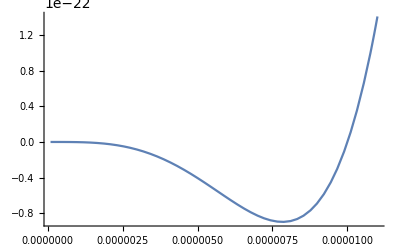

(ⅇ^(-(4 ηIR)/l) (-ϵm ϕIR^2+(ⅇ^(-ηIR/l))^(2 ϵp) ϵp ϕUV^2))/(2 l)

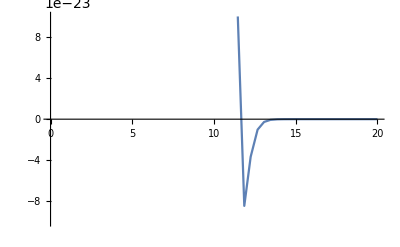

```mathematica
Print["Expand the GW potential and get in the form of CR"]
Plusregioncont+Minusregioncont
%/.ηIR ->- l Log[r ]/.r^4->rConf/.r^(2(2+ϵp))->rGW/.r^(-2(2+ϵp))->rGW^-1
Series[%,{ϵp,0,1}]
Series[%,{ϵm,0,1}]//Simplify
%//Normal
VGWexpanded=%/.rConf->r^4/.rGW->r^(2(2+ϵp))/.rGW^-1->r^(-2(2+ϵp))//Simplify
Print["This is qualitatively similar to the GW potential. There is however a small difference compared to the braced expression eqn (29)"]
D[VGWexpanded,r]
VGWexpMin=Solve[%==0,r][[1]]//Simplify
(*%//PowerExpand//Simplify
Series[r/.%,{ϵp,0,1}]//Normal//Simplify//PowerExpand*)
(*VGWexpMin/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->1/.l->1
Plot[VGWexpanded/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->1/.l->1,{r,0,1}]*)
VGWexpMin/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1
-(VGWexpanded - CoefficientList[VGWexpanded,r][[1]])//Simplify
Plot[%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1,{r,10^-7,1.1 10^-5}]
-(VGWexpanded- CoefficientList[VGWexpanded,r][[1]] )/.r->E^(-ηIR/l)//Simplify
Plot[%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1,{ηIR,0,20},PlotRange->{-10^-22,10^-22}]
```

```mathematica
Solve[D[E^(-4 ηIR/l)(ϵp ϕIR^2-ϵp E^(-2 ϵp ηIR/l)ϕUV^2),ηIR]==0,ηIR]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ηIR→(l Log[((2+ϵp) ϕUV^2)/(2 ϕIR^2)])/(2 ϵp)}}

Now expand to leading order in ϵ_i without taking the exponential to be small

(ⅇ^(-(4 ηIR)/l) ϵm ϕIR^2+ϵp ϕUV^2-ⅇ^(-(2 (2+ϵp) ηIR)/l) ϵp ϕUV^2)/(2 l)

(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-2 ⅇ^((2 ϵp ηIR)/l) ϵm ϕIR^2+ϵp (2+ϵp) ϕUV^2))/l^2

-(ⅇ^(-(2 (2+ϵp) ηIR)/l) (2 ⅇ^((2 ϵp ηIR)/l) ϵm ϕIR^2-2 ϵp ϕUV^2))/l^2

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{ηIR→(l Log[(ϵp ϕUV^2)/(ϵm ϕIR^2)])/(2 ϵp)}

{ηIR→(l Log[10])/(2 ϵp)}

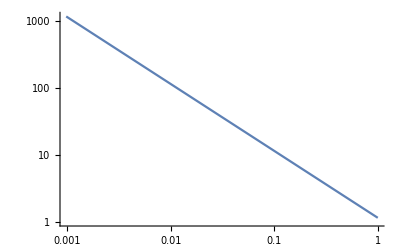

5.-5. ⅇ^(-4.2 ηIR)+0.5 ⅇ^(-4. ηIR)

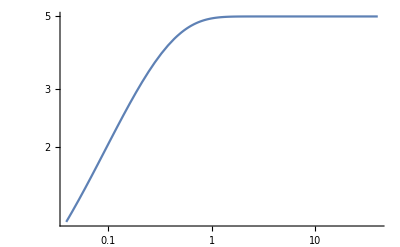

```mathematica
Print["Now expand to leading order in ϵ_i without taking the exponential to be small"]
VGW=-(-(ⅇ^(-(4 ηIR)/l) ϵm (4) ϕIR^2)/(4 l (2))-(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4) ϕUV^2)/(4 l (2)))//Simplify
D[%,ηIR]//Simplify
-(ⅇ^(-(2 (2+ϵp) ηIR)/l) (2 ⅇ^((2 ϵp ηIR)/l) ϵm ϕIR^2-ϵp (2) ϕUV^2))/l^2
Solve[%==0,ηIR][[1]]//Simplify
%/.ϕUV->10ϕIR/.ϵm->10ϵp
LogLogPlot[ηIR/l/.%,{ϵp,0,1}]
VGW/ϕIR^2/.ϕUV->10ϕIR/.ϵm->10ϵp/.ϵp->0.1/.l->1//Simplify
LogLogPlot[Abs[%],{ηIR,0,40},PlotRange->All]
```

#### Compute GW potential - w first μ correction

```mathematica
Print["The original GW potential is computed as"]
Gsqrtdet=rc E^(-4 k rc ϕ)
Gupupϕϕ=- rc^-2
Φ = A E^((2 + ν) k rc ϕ)+ B E^((2 -ν) k rc ϕ)
-Gsqrtdet (Gupupϕϕ D[Φ,ϕ]^2 - m^2 Φ^2)/.m ->k √(ν^2-4)//Simplify
Integrate[%,{ϕ,0,π}]//Simplify
%/.A->0//Simplify
%%/.B->0
Print["This agrees with eqn (8) of the original GW proposal"]
```

The original GW potential is computed as

ⅇ^(-4 k rc ϕ) rc

-1/rc^2

B ⅇ^(k rc (2-ν) ϕ)+A ⅇ^(k rc (2+ν) ϕ)

2 ⅇ^(-2 k rc ν ϕ) k^2 rc ν (B^2 (-2+ν)+A^2 ⅇ^(4 k rc ν ϕ) (2+ν))

ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k (B^2 (-2+ν)+A^2 ⅇ^(2 k π rc ν) (2+ν))

B^2 ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k (-2+ν)

A^2 (-1+ⅇ^(2 k π rc ν)) k (2+ν)

This agrees with eqn (8) of the original GW proposal

```mathematica
D[E^(-4 k rc π)(vv - vh E^(-ϵ k rc π))^2,rc]//Simplify
Solve[%==0,rc] //Simplify
%/.ϵ->m^2/(4 k^2)
```

-2 ⅇ^(-2 k π rc (2+ϵ)) k π (vh-ⅇ^(k π rc ϵ) vv) (-2 ⅇ^(k π rc ϵ) vv+vh (2+ϵ))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{rc→Log[vh/vv]/(k π ϵ)},{rc→Log[(vh (2+ϵ))/(2 vv)]/(k π ϵ)}}

{{rc→(4 k Log[vh/vv])/(m^2 π)},{rc→(4 k Log[((2+m^2/(4 k^2)) vh)/(2 vv)])/(m^2 π)}}

```mathematica
gη
Series[gη,{μ,0,2}]-Series[gη,{μ,0,0}]
```

{{ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ c[η]) (1-3/4 ⅇ^((4 η)/l) μ),0,0,0,0},{0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0,0},{0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0},{0,0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0},{0,0,0,0,-1}}

{{O[μ]^1,0,0,0,0},{0,O[μ]^1,0,0,0},{0,0,O[μ]^1,0,0},{0,0,0,O[μ]^1,0},{0,0,0,0,0}}

```mathematica
Print["ϕ stuff"]
ϕ0sol
ϕmsol = ϕIR E^(- ϵm (η-ηIR)/l)
ϕ0sol/.ϵ->ϵm/.C[0]->ϕIR E^(ϵm ηIR/l)//Simplify
ϕpsol=ϕUV E^(-ϵp η/l)
Print["metric stuff"]
detgηsmallμ0
Aofηsol/.C[2]->0/.C[1]->C[0]
(*Series[gη,{μ,0,1}]-Series[gη,{μ,0,0}]//Normal*)
Series[gη,{μ,0,0}]//Normal
Print["The effective action for the scalar away from the branes is"]
Leff = √detgηsmallμ0(%%[[5,5]] D[ϕ0[η]/.ϕ0sol,η]^2-1/2(ϵ(ϵ+4))/l^2 (ϕ0[η]/.ϕ0sol)^2)/.Aofηsol/.C[2]->0/.C[1]->C[0]//Simplify//PowerExpand
Print["In the limit of no back reaction, this gives the 4D effective potential as"]
-Integrate[Leff/.M->∞,η]
Plusregioncont=(%/.η->ηIR/.ϵ->ϵp/.C[0]->ϕUV/.ϵ->ϵp)-(%/.η->0/.C[0]->ϕUV/.ϵ->ϵp)//Simplify
Minusregioncont=-(%%/.η->ηIR/.C[0]->ϕIR E^(ϵm ηIR/l))/.ϵ->ϵm//Simplify
Print["This gives the effective potential"]
Plusregioncont+Minusregioncont
(*D[Plusregioncont+Minusregioncont,ηIR]//Simplify*)
(*Solve[%==0,ηIR]
ηIR/l/.%/.ϵp->ν ϵm/.ϵm->0.05
Plot[%,{ν,0,1}]*)
```

ϕ stuff

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

ⅇ^(-(ϵm (η-ηIR))/l) ϕIR

ϕ0[η]→ⅇ^((ϵm (-η+ηIR))/l) ϕIR

ⅇ^(-(ϵp η)/l) ϕUV

metric stuff

ⅇ^(8 A[η])

A[η]→-η/l-(ⅇ^(-(2 ϵ η)/l) C[0]^2)/(48 M^3)

{{ⅇ^(2 A[η]),0,0,0,0},{0,-ⅇ^(2 A[η]),0,0,0},{0,0,-ⅇ^(2 A[η]),0,0},{0,0,0,-ⅇ^(2 A[η]),0},{0,0,0,0,-1}}

The effective action for the scalar away from the branes is

-(ⅇ^(-(2 ϵ η)/l+1/2 (-(8 η)/l-(ⅇ^(-(2 ϵ η)/l) C[0]^2)/(6 M^3))) ϵ (4+3 ϵ) C[0]^2)/(2 l^2)

In the limit of no back reaction, this gives the 4D effective potential as

-(ⅇ^(-(2 (2+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2)/(4 l (2+ϵ))

(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))

This gives the effective potential

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))+(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

```mathematica
Print["Work at first order in the back reaction for the effective action"]
(*Integrate[Leff/E^(-2ϵ η/l)/.C[0]->M^(3/2) ξϕ,η]
Series[%,{ξϕ,0,4}]//Normal//Simplify*)
Series[Leff,{M,∞,3}]//Normal//Simplify
Integrate[%,η]//FullSimplify
```

Work at first order in the back reaction for the effective action

(ⅇ^(-(4 (1+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2 (-12 ⅇ^((2 ϵ η)/l) M^3+C[0]^2))/(24 l^2 M^3)

(ⅇ^(-(4 (1+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2 ((6 ⅇ^((2 ϵ η)/l) l M^3)/(2+ϵ)-(l C[0]^2)/(4 (1+ϵ))))/(24 l^2 M^3)

```mathematica
Print["Expand the GW potential and get in the form of CR and include the boundary term"]
Vboundary= -1/2(ϵm-ϵp)/l E^(-4 ηIR/l) ϕIR^2+ϵp/l ϕUV^2
Plusregioncont+Minusregioncont + Vboundary
%/.ηIR ->- l Log[r ]/.r^4->rConf/.r^(2(2+ϵp))->rGW/.r^(-2(2+ϵp))->rGW^-1
Series[%,{ϵp,0,1}]
Series[%,{ϵm,0,1}]//Simplify
%//Normal 
VGWexpanded=%/.rConf->r^4/.rGW->r^(2(2+ϵp))/.rGW^-1->r^(-2(2+ϵp))//Simplify
```

Expand the GW potential and get in the form of CR and include the boundary term

-(ⅇ^(-(4 ηIR)/l) (ϵm-ϵp) ϕIR^2)/(2 l)+(ϵp ϕUV^2)/l

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))-(ⅇ^(-(4 ηIR)/l) (ϵm-ϵp) ϕIR^2)/(2 l)+(ϵp ϕUV^2)/l+(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(rConf ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))-(rConf (ϵm-ϵp) ϕIR^2)/(2 l)+(ϵp ϕUV^2)/l+((-1+1/rGW) rGW ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(rConf ϵm^2 ϕIR^2)/(4 l (2+ϵm))+((rConf ϕIR^2+3 ϕUV^2-rGW ϕUV^2) ϵp)/(2 l)+O[ϵp]^2

O[ϵm]^2+((rConf ϕIR^2-(-3+rGW) ϕUV^2) ϵp)/(2 l)+O[ϵp]^2

(ϵp (rConf ϕIR^2-(-3+rGW) ϕUV^2))/(2 l)

(ϵp (r^4 ϕIR^2-(-3+r^(4+2 ϵp)) ϕUV^2))/(2 l)

This is qualitatively similar to the GW potential. There is however a small difference compared to the braced expression eqn (29)

(ϵp (4 r^3 ϕIR^2-r^(3+2 ϵp) (4+2 ϵp) ϕUV^2))/(2 l)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{r→2^(1/2/ϵp) (((2+ϵp) ϕUV^2)/ϕIR^2)^(-1/2/ϵp)}

rmin is:

7.83526×10^-11

(r^4 ϵp (ϕIR^2-r^(2 ϵp) ϕUV^2))/(2 l)

0.05 (1-100 r^0.2) r^4

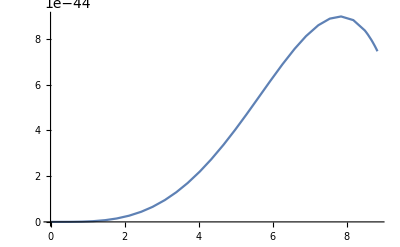

(ⅇ^(-(4 ηIR)/l) ϵp (ϕIR^2-(ⅇ^(-ηIR/l))^(2 ϵp) ϕUV^2))/(2 l)

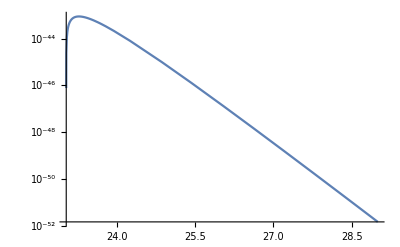

(ⅇ^(-4/(kIR l)) ϵp (ϕIR^2-(ⅇ^(-1/(kIR l)))^(2 ϵp) ϕUV^2))/(2 l)

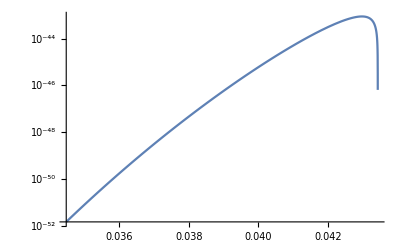

```mathematica
Print["This is qualitatively similar to the GW potential. There is however a small difference compared to the braced expression eqn (29)"]
D[VGWexpanded,r]
VGWexpMin=Solve[%==0,r][[1]]//Simplify
Print["rmin is: "]
rmin=r/.VGWexpMin/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1
(*%//PowerExpand//Simplify
Series[r/.%,{ϵp,0,1}]//Normal//Simplify//PowerExpand*)
(*VGWexpMin/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->1/.l->1
Plot[VGWexpanded/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->1/.l->1,{r,0,1}]*)


(VGWexpanded- CoefficientList[VGWexpanded,r][[1]] )//Simplify
%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1
Plot[%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1,{r,10^-11 -rmin,rmin+ 10^-11},PlotRange->All]

(VGWexpanded- CoefficientList[VGWexpanded,r][[1]] )/.r->E^(-ηIR/l)//Simplify
LogPlot[%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1,{ηIR,0,29},PlotRange->All]

(VGWexpanded- CoefficientList[VGWexpanded,r][[1]] )/.r->E^(-ηIR/l)/.ηIR->1/kIR//Simplify
LogPlot[%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1,{kIR,1/29,1/23},PlotRange->All]
```

```mathematica
(VGWexpanded-Vboundary/.ηIR->-l Log[r])
CoefficientList[%,r][[1]]//Simplify
```

(r^4 (ϵm-ϵp) ϕIR^2)/(2 l)-(ϵp ϕUV^2)/l+(ϵp (r^4 ϕIR^2-(-3+r^(4+2 ϵp)) ϕUV^2))/(2 l)

(ϵp ϕUV^2)/(2 l)

{ϵp→0.01,ϵm→0.1,ϕIR→1,ϕUV→10,l→1}

(r^4 (ϵm ϕIR^2-r^(2 ϵp) ϵp ϕUV^2))/(2 l)

1/2 (0.1-1. r^0.02) r^4

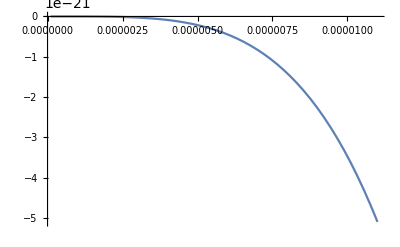

(ⅇ^(-(4 ηIR)/l) (ϵm ϕIR^2-(ⅇ^(-ηIR/l))^(2 ϵp) ϵp ϕUV^2))/(2 l)

1/2 ⅇ^(-4 ηIR) (0.1-1. (ⅇ^-ηIR)^0.02)

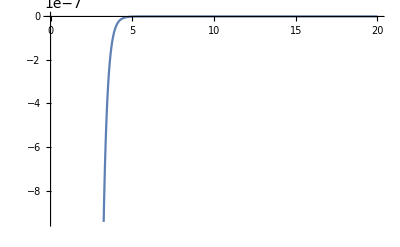

```mathematica
repl = {ϵp->0.01 ,ϵm->0.1,ϕIR->1,ϕUV->10,l->1}
(VGWexpanded -Vboundary- CoefficientList[VGWexpanded-Vboundary/.ηIR->-l Log[r],r][[1]])/.ηIR->-l Log[r]//Simplify
(*Plot[%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1,{r,10^-7,1.1 10^-5}]*)
%/.repl
Plot[%/.repl,{r,10^-7,1.1 10^-5}]
(*used before adding in boundary potential*)
(VGWexpanded-Vboundary- CoefficientList[VGWexpanded-Vboundary/.ηIR->-l Log[r],r][[1]] )/.r->E^(-ηIR/l)//Simplify
%/.repl
Plot[%/.repl,{ηIR,0,20}](*used before adding in boundary potential*)
```

```mathematica
Solve[D[(VGWexpanded-Vboundary- CoefficientList[VGWexpanded-Vboundary/.ηIR->-l Log[r],r][[1]] )/.r->E^(-ηIR/l)//Simplify,{ηIR,1}]==0,ηIR][[2]]
D[(VGWexpanded-Vboundary- CoefficientList[VGWexpanded-Vboundary/.ηIR->-l Log[r],r][[1]] )/.r->E^(-ηIR/l)//Simplify,{ηIR,2}]/.%//Simplify//PowerExpand//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{ηIR→(l Log[(√ϵp √(2+ϵp) ϕUV)/(√2 √ϵm ϕIR)])/ϵp}

-(4^(1+1/ϵp) ϵm^((2+ϵp)/ϵp) ϵp^((-2+ϵp)/ϵp) (2+ϵp)^(-2/ϵp) ϕIR^(2+4/ϵp) ϕUV^(-4/ϵp))/l^3

```mathematica
N@(1/29)
```

0.0344828

```mathematica
Print["Get the stability of the extremum found above"]
ηmin=Series[η/.Solve[D[VGWexpanded/.r->E^(-η/l),{η,1}]==0,η][[2]],{ϵp,0,-1}]//Normal
D[VGWexpanded/.r->E^(-η/l),{η,2}]/.η->ηmin//Simplify//PowerExpand//Simplify
VGWexpanded/.r->E^(-η/l)/.η->ηmin//Simplify//PowerExpand//Simplify
```

Get the stability of the extremum found above

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(l Log[ϕUV/ϕIR])/ϵp

-(2 ϵp^2 (4+ϵp) ϕIR^(2+4/ϵp) ϕUV^(-4/ϵp))/l^3

(3 ϵp ϕUV^2)/(2 l)

```mathematica
Print["Try the same with a mass scale instead of η scale"]
D[VGWexpanded/.r->E^(-η/l)/.η->1/k,{k,2}]/.k->ηmin^-1//Simplify//PowerExpand//FullSimplify
%/.ϕIR->3/.ϕUV->1/.ϵp->0.1
VGWexpanded/.r->E^(-η/l)/.η->1/k/.k->ηmin^-1//Simplify//PowerExpand//Simplify
Print["Conclusion is unchanged, just have the right dimensions."]
```

Try the same with a mass scale instead of η scale

-(2 l ϕIR^(2+4/ϵp) ϕUV^(-4/ϵp) (Log[ϕIR]-Log[ϕUV])^3 (ϵp+(4+ϵp) Log[ϕIR]-(4+ϵp) Log[ϕUV]))/ϵp^2

-1.33604×10^23 l

(3 ϵp ϕUV^2)/(2 l)

Conclusion is unchanged, just have the right dimensions.

```mathematica
Integrate[D[-l Log[r],r]Leff/.M->∞/.η->-l Log[r]//Simplify,{r,0,rIR}]
```

ConditionalExpression[(rIR^(4+2 ϵ) ϵ (4+3 ϵ) C[0]^2)/(4 l (2+ϵ)), Re[ϵ]>-2]

```mathematica
Clear[ϕ]
DSolve[ϕ''[η]-4/l ϕ'[η]==ϵ (ϵ + 4)/l^2 ϕ[η],ϕ[η],η ]
```

{{ϕ[η]→ⅇ^(-(ϵ η)/l) C[1]+ⅇ^(((4+ϵ) η)/l) C[2]}}

#### Consider both ϕ solutions consistent with EOM and JCs

```mathematica
ABsol={A,B}/.Solve[{ϕIR == A E^(-ϵ/l ηIR)+B E^((4+ϵ)/l ηIR)
,ϕUV == A + B},{A,B}][[1]]/.ηIR->l Log[r]//Simplify

ABsol (-1+r^(4+2 ϵ)) (Series[1/(1-x),{x,∞,2}]//Normal)/.x->r^(4+2 ϵ)//Simplify//Expand
Series[%,{ϵ,0,1}]//Normal
Series[%,{r,∞,4}]
```

{(r^ϵ (-ϕIR+r^(4+ϵ) ϕUV))/(-1+r^(4+2 ϵ)),(r^ϵ ϕIR-ϕUV)/(-1+r^(4+2 ϵ))}

{r^(-8-3 ϵ) ϕIR+r^(-4-ϵ) ϕIR-ϕUV-r^(-4-2 ϵ) ϕUV,-r^(ϵ-4 (2+ϵ)) ϕIR-r^(4+3 ϵ-4 (2+ϵ)) ϕIR+r^(-4 (2+ϵ)) ϕUV+r^(4+2 ϵ-4 (2+ϵ)) ϕUV}

{ϕIR/r^8+ϕIR/r^4-ϕUV-ϕUV/r^4+ϵ (-(3 ϕIR Log[r])/r^8-(ϕIR Log[r])/r^4+(2 ϕUV Log[r])/r^4),-((1+r^4) (ϕIR-ϕUV))/r^8+(ϵ (3 ϕIR Log[r]+r^4 ϕIR Log[r]-4 ϕUV Log[r]-2 r^4 ϕUV Log[r]))/r^8}

{-ϕUV+(ϕIR-ϕUV-ϵ ϕIR Log[r]+2 ϵ ϕUV Log[r])/r^4+O[1/r]^5,(-ϕIR+ϕUV+ϵ ϕIR Log[r]-2 ϵ ϕUV Log[r])/r^4+O[1/r]^5}

```mathematica
Limit[ABsol,r->∞]
Limit[D[ABsol,r],r->∞]
Limit[D[ABsol,{r,2}],r->∞]
```

{ConditionalExpression[ϕUV, (ϕIR|ϕUV)∈ℝ&&ϵ>0],ConditionalExpression[0, (ϕIR|ϕUV)∈ℝ&&ϵ>0]}

{ConditionalExpression[0, (ϕUV|ϕIR)∈ℝ&&0<ϵ<1],ConditionalExpression[0, (ϕIR|ϕUV)∈ℝ&&0<ϵ<1]}

{ConditionalExpression[0, (ϕUV|ϕIR)∈ℝ&&0<ϵ<1],ConditionalExpression[0, (ϕIR|ϕUV)∈ℝ&&0<ϵ<2]}

```mathematica
1/r^(4+2ϵ)Series[1/(1-r^(-4-2ϵ)),{r,∞,2}]
```

r^(-4-2 ϵ)/(1-r^(-4-2 ϵ))

```mathematica
Series[1/(1-x),{x,0,2}]
```

1+x+x^2+O[x]^3

```mathematica
Series[(r^ϵ (-ϕIR+r^(4+ϵ) ϕUV))/(-1+r^(4+2 ϵ)),{r,∞,1}]
```

(r^ϵ (-ϕIR+r^(4+ϵ) ϕUV))/(-1+r^(4+2 ϵ))

```mathematica
Print["The full solution in the + region is:"]
ϕpbothsols=ABsol{E^(-ϵ η/l),ⅇ^(((4+ϵ) η)/l)}/.r->E^(ηIR/l)//PowerExpand//Total//Simplify
%/.η->0//Simplify
(D[%%,η]==-ϵ/l ϕIR/.η->ηIR//Simplify)
(D[%%%,η]==-ϵ/l ϕUV/.η->0//Simplify)
Print["So both junction conditions are satisfied provided ϕIR = E^(-ϵ FractionBox[ηIR, l])ϕUV, which should be satsified on the minimum of the potential"]
```

The full solution in the + region is:

(ⅇ^(-(ϵ η)/l) (-ⅇ^((ϵ ηIR)/l) ϕIR+ⅇ^((2 (2+ϵ) η+ϵ ηIR)/l) ϕIR-ⅇ^((2 (2+ϵ) η)/l) ϕUV+ⅇ^((2 (2+ϵ) ηIR)/l) ϕUV))/(-1+ⅇ^((2 (2+ϵ) ηIR)/l))

ϕUV

(ⅇ^(((4+ϵ) ηIR)/l) (2+ϵ) (ⅇ^((ϵ ηIR)/l) ϕIR-ϕUV))/((-1+ⅇ^((2 (2+ϵ) ηIR)/l)) l)==0

((2+ϵ) (ⅇ^((ϵ ηIR)/l) ϕIR-ϕUV))/((-1+ⅇ^((2 (2+ϵ) ηIR)/l)) l)==0

So both junction conditions are satisfied provided ϕIR = E^(-ϵ FractionBox[ηIR, l])ϕUV, which should be satsified on the minimum of the potential

```mathematica
ϕmsol = ϕIR E^(-ϵm (η-ηIR)/l)
ϕtotalbothsols = (ϕpbothsols/.ϵ->ϵp)HeavisideTheta[ηIR-η] + ϕmsol HeavisideTheta[η-ηIR]
```

ⅇ^(-(ϵm (η-ηIR))/l) ϕIR

ⅇ^(-(ϵm (η-ηIR))/l) ϕIR HeavisideTheta[η-ηIR]+(ⅇ^(-(ϵp η)/l) (-ⅇ^((ϵp ηIR)/l) ϕIR+ⅇ^((2 (2+ϵp) η+ϵp ηIR)/l) ϕIR-ⅇ^((2 (2+ϵp) η)/l) ϕUV+ⅇ^((2 (2+ϵp) ηIR)/l) ϕUV) HeavisideTheta[-η+ηIR])/(-1+ⅇ^((2 (2+ϵp) ηIR)/l))

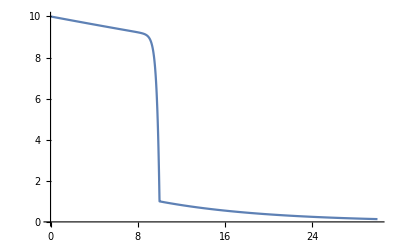

```mathematica
Plot[ϕtotalbothsols/.η->ηt/.{l->1,ϵp->0.01,ϵm->0.1,ηIR->10,ϕIR->1,ϕUV->10},{ηt,0,30},PlotRange->{0,10}]
```

#### Look for a potential which has the above domain wall solutions

```mathematica
U''[a1]==m1^2
U''[a2]==m2^2
U'[a1]==U'[a2]==0
```

U''[a1]==m1^2

U''[a2]==m2^2

U'[a1]==U'[a2]==0

```mathematica
f = a r^4+b r^3 + c r^2 + d r
sol=Solve[{D[f,{r,2}]==m1^2/.r->r1//Simplify,
D[f,{r,2}]==m2^2/.r->r2//Simplify,
D[f,{r,1}]==0/.r->r1//Simplify,
D[f,{r,1}]==0/.r->r2//Simplify},{a,b,c,d}][[1]]
f/.sol//FullSimplify
%/.{m1->√(ϵm(ϵm+4)),m2->√(ϵp(ϵp+4))}//FullSimplify
(*Solve[{D[a(r^2-c)^2+b(r^2-d^2)^2,{r,2}]==m1^2/.r->c//Simplify,
D[a(r^2-c)^2+b(r^2-d^2)^2,{r,2}]==m2^2/.r->d//Simplify,
D[a(r^2-c)^2+b(r^2-d^2)^2,{r,1}]==0/.r->c//Simplify,
D[a(r^2-c)^2+b(r^2-d^2)^2,{r,1}]==0/.r->d//Simplify},{a,b,c,d}]*)
```

d r+c r^2+b r^3+a r^4

{a→-(-m1^2-m2^2)/(4 (r1-r2)^2),b→-(m1^2 r1+2 m2^2 r1+2 m1^2 r2+m2^2 r2)/(3 (r1-r2)^2),c→-(-m2^2 r1^2-2 m1^2 r1 r2-2 m2^2 r1 r2-m1^2 r2^2)/(2 (r1-r2)^2),d→-(m2^2 r1^2 r2+m1^2 r1 r2^2)/(r1-r2)^2}

(r (m1^2 (3 r^3-12 r1 r2^2+6 r r2 (2 r1+r2)-4 r^2 (r1+2 r2))+m2^2 (3 r^3-12 r1^2 r2-4 r^2 (2 r1+r2)+6 r r1 (r1+2 r2))))/(12 (r1-r2)^2)

1/(12 (r1-r2)^2)r ((3 r^3-12 r1 r2^2+6 r r2 (2 r1+r2)-4 r^2 (r1+2 r2)) ϵm (4+ϵm)+(3 r^3-12 r1^2 r2-4 r^2 (2 r1+r2)+6 r r1 (r1+2 r2)) ϵp (4+ϵp))

```mathematica
f = a ϕ^4+b ϕ^3 + c ϕ^2 + d ϕ
sol=Solve[{D[f,{ϕ,2}]==m1^2/.ϕ->ϕ1//Simplify,
D[f,{ϕ,2}]==m2^2/.ϕ->ϕ2//Simplify,
D[f,{ϕ,1}]==0/.ϕ->ϕ1//Simplify,
D[f,{ϕ,1}]==0/.ϕ->ϕ2//Simplify},{a,b,c,d}][[1]]
f/.sol//Expand
%/.{m1->√(ϵm(ϵm+4)),m2->√(ϵp(ϵp+4))}//Simplify
Series[%,{ϕ,0,4}]
```

d ϕ+c ϕ^2+b ϕ^3+a ϕ^4

{a→-(-m1^2-m2^2)/(4 (ϕ1-ϕ2)^2),b→-(m1^2 ϕ1+2 m2^2 ϕ1+2 m1^2 ϕ2+m2^2 ϕ2)/(3 (ϕ1-ϕ2)^2),c→-(-m2^2 ϕ1^2-2 m1^2 ϕ1 ϕ2-2 m2^2 ϕ1 ϕ2-m1^2 ϕ2^2)/(2 (ϕ1-ϕ2)^2),d→-(m2^2 ϕ1^2 ϕ2+m1^2 ϕ1 ϕ2^2)/(ϕ1-ϕ2)^2}

(m1^2 ϕ^4)/(4 (ϕ1-ϕ2)^2)+(m2^2 ϕ^4)/(4 (ϕ1-ϕ2)^2)-(m1^2 ϕ^3 ϕ1)/(3 (ϕ1-ϕ2)^2)-(2 m2^2 ϕ^3 ϕ1)/(3 (ϕ1-ϕ2)^2)+(m2^2 ϕ^2 ϕ1^2)/(2 (ϕ1-ϕ2)^2)-(2 m1^2 ϕ^3 ϕ2)/(3 (ϕ1-ϕ2)^2)-(m2^2 ϕ^3 ϕ2)/(3 (ϕ1-ϕ2)^2)+(m1^2 ϕ^2 ϕ1 ϕ2)/(ϕ1-ϕ2)^2+(m2^2 ϕ^2 ϕ1 ϕ2)/(ϕ1-ϕ2)^2-(m2^2 ϕ ϕ1^2 ϕ2)/(ϕ1-ϕ2)^2+(m1^2 ϕ^2 ϕ2^2)/(2 (ϕ1-ϕ2)^2)-(m1^2 ϕ ϕ1 ϕ2^2)/(ϕ1-ϕ2)^2

1/(12 (ϕ1-ϕ2)^2)ϕ (4 ϵm (3 ϕ^3-12 ϕ1 ϕ2^2+6 ϕ ϕ2 (2 ϕ1+ϕ2)-4 ϕ^2 (ϕ1+2 ϕ2))+ϵm^2 (3 ϕ^3-12 ϕ1 ϕ2^2+6 ϕ ϕ2 (2 ϕ1+ϕ2)-4 ϕ^2 (ϕ1+2 ϕ2))+ϵp (4+ϵp) (3 ϕ^3-12 ϕ1^2 ϕ2-4 ϕ^2 (2 ϕ1+ϕ2)+6 ϕ ϕ1 (ϕ1+2 ϕ2)))

((-12 ϵp (4+ϵp) ϕ1^2 ϕ2-48 ϵm ϕ1 ϕ2^2-12 ϵm^2 ϕ1 ϕ2^2) ϕ)/(12 (ϕ1-ϕ2)^2)+((24 ϵm ϕ2 (2 ϕ1+ϕ2)+6 ϵm^2 ϕ2 (2 ϕ1+ϕ2)+6 ϵp (4+ϵp) ϕ1 (ϕ1+2 ϕ2)) ϕ^2)/(12 (ϕ1-ϕ2)^2)+((-4 ϵp (4+ϵp) (2 ϕ1+ϕ2)-16 ϵm (ϕ1+2 ϕ2)-4 ϵm^2 (ϕ1+2 ϕ2)) ϕ^3)/(12 (ϕ1-ϕ2)^2)+((4 ϵm+ϵm^2+4 ϵp+ϵp^2) ϕ^4)/(4 (ϕ1-ϕ2)^2)+O[ϕ]^5

```mathematica
f = a r^4+b r^3 + c r^2 + d r/.r->E^(-η/l)
sol=Solve[{D[f,{η,2}]==m1^2/.η->r1//Simplify,
D[f,{η,2}]==m2^2/.η->r2//Simplify,
D[f,{η,1}]==0/.η->r1//Simplify,
D[f,{η,1}]==0/.η->r2//Simplify},{a,b,c,d}][[1]]
f/.sol/.r2->0/.r1-> ηIR//FullSimplify
%/.{m1->√(ϵm(ϵm+4)),m2->√(ϵp(ϵp+4))}//FullSimplify
```

a ⅇ^(-(4 η)/l)+b ⅇ^(-(3 η)/l)+c ⅇ^(-(2 η)/l)+d ⅇ^(-η/l)

{a→(ⅇ^((2 r1)/l+(2 r2)/l) l^2 (ⅇ^((2 r1)/l) m1^2+ⅇ^((2 r2)/l) m2^2))/(4 (-ⅇ^(r1/l)+ⅇ^(r2/l))^2),b→-(ⅇ^(r1/l+r2/l) l^2 (2 ⅇ^((3 r1)/l) m1^2+ⅇ^((2 r1)/l+r2/l) m1^2+2 ⅇ^((3 r2)/l) m2^2+ⅇ^(r1/l+(2 r2)/l) m2^2))/(3 (-ⅇ^(r1/l)+ⅇ^(r2/l))^2),c→(l^2 (ⅇ^((4 r1)/l) m1^2+2 ⅇ^((3 r1)/l+r2/l) m1^2+ⅇ^((4 r2)/l) m2^2+2 ⅇ^(r1/l+(3 r2)/l) m2^2))/(2 (ⅇ^(r1/l)-ⅇ^(r2/l))^2),d→-(l^2 (ⅇ^((3 r1)/l) m1^2+ⅇ^((3 r2)/l) m2^2))/((ⅇ^(r1/l)-ⅇ^(r2/l))^2)}

1/(12 (-1+ⅇ^(ηIR/l))^2)ⅇ^(-(4 η)/l) l^2 (3 ⅇ^((2 ηIR)/l) (ⅇ^((2 ηIR)/l) m1^2+m2^2)-12 ⅇ^((3 η)/l) (ⅇ^((3 ηIR)/l) m1^2+m2^2)+6 ⅇ^((2 η)/l) (2 ⅇ^((3 ηIR)/l) m1^2+ⅇ^((4 ηIR)/l) m1^2+m2^2+2 ⅇ^(ηIR/l) m2^2)-4 ⅇ^((η+ηIR)/l) (2 m2^2+ⅇ^(ηIR/l) (ⅇ^(ηIR/l) (1+2 ⅇ^(ηIR/l)) m1^2+m2^2)))

1/(12 (-1+ⅇ^(ηIR/l))^2)ⅇ^(-(4 η)/l) l^2 (3 ⅇ^((2 ηIR)/l) (ⅇ^((2 ηIR)/l) ϵm (4+ϵm)+ϵp (4+ϵp))-12 ⅇ^((3 η)/l) (ⅇ^((3 ηIR)/l) ϵm (4+ϵm)+ϵp (4+ϵp))-4 ⅇ^((η+ηIR)/l) (ⅇ^((2 ηIR)/l) (1+2 ⅇ^(ηIR/l)) ϵm (4+ϵm)+2 ϵp (4+ϵp)+ⅇ^(ηIR/l) ϵp (4+ϵp))+6 ⅇ^((2 η)/l) (2 ⅇ^((3 ηIR)/l) ϵm (4+ϵm)+ⅇ^((4 ηIR)/l) ϵm (4+ϵm)+ϵp (4+ϵp)+2 ⅇ^(ηIR/l) ϵp (4+ϵp)))

```mathematica
sol/.{m1->0.1,m2->1}
Plot[f/.sol/.{m1->0.1,m2->1},{r,-0.1,1}]
```

{a→(ⅇ^((2 r1)/l+(2 r2)/l) (0.01 ⅇ^((2 r1)/l)+ⅇ^((2 r2)/l)) l^2)/(4 (-ⅇ^(r1/l)+ⅇ^(r2/l))^2),b→-(ⅇ^(r1/l+r2/l) (0.02 ⅇ^((3 r1)/l)+2 ⅇ^((3 r2)/l)+0.01 ⅇ^((2 r1)/l+r2/l)+ⅇ^(r1/l+(2 r2)/l)) l^2)/(3 (-ⅇ^(r1/l)+ⅇ^(r2/l))^2),c→((0.01 ⅇ^((4 r1)/l)+ⅇ^((4 r2)/l)+0.02 ⅇ^((3 r1)/l+r2/l)+2 ⅇ^(r1/l+(3 r2)/l)) l^2)/(2 (ⅇ^(r1/l)-ⅇ^(r2/l))^2),d→-((0.01 ⅇ^((3 r1)/l)+ⅇ^((3 r2)/l)) l^2)/((ⅇ^(r1/l)-ⅇ^(r2/l))^2)}

-Graphics-

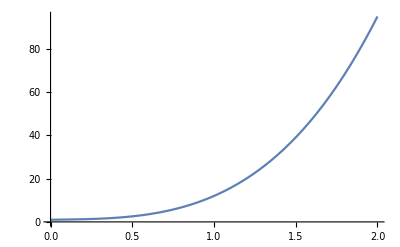

```mathematica
Plot[a^4 +10a^3-a^2+a+1,{a,0,2}]
```

#### Try to reproduce Zamir’s BR calculation

```mathematica
χ=k E^(- k yc - r[x] E^(2k yc))
D[D[χ,x]^2,r[x]]
(*D[D[χ,x]^2,r'[x]]
%% - D[%,x]//Simplify*)
```

ⅇ^(-k yc-ⅇ^(2 k yc) r[x]) k

-2 ⅇ^(4 k yc-2 ⅇ^(2 k yc) r[x]) k^2 r'[x]^2

```mathematica
Solve[χt[x]==χ,r[x]][[1]]/.C[1]->0
D[r[x]/.%,{x,1}]
```

{r[x]→-ⅇ^(-2 k yc) (k yc-Log[k/χt[x]])}

-(ⅇ^(-2 k yc) χt'[x])/χt[x]

## Scrap

### Expand in small μ/p^2 - NTLO Perturb Scalar correct ansatz - expand in ξ instead of ξA - Incorrect κ expansion of EFEs

#### Expand in μ and get GN coordinate

Rescale so that p and μ are dimensionless

```mathematica
p[η]->l p[η]
μ/l^2->μ
dp[η]/(√(p[η]^2/l^2-μ/p[η]^2))-> (l dp[η])/(√(p[η]^2-μ/p[η]^2))
```

p[η]→l p[η]

μ/l^2→μ

dp[η]/(√(-μ/p[η]^2+p[η]^2/l^2))→(l dp[η])/(√(-μ/p[η]^2+p[η]^2))

Then solve for gaussian normal coordinate

```mathematica
pofη=Simplify[p[η]/.DSolve[l D[p[η],η]==√(p[η]^2-μ/p[η]^2),p[η],η]][[2]]
ηofp=η/.Solve[pofη==p,η][[2]]//Simplify
Simplify[E^(ηofp/l)]
```

(ⅇ^(-(η+l C[1])/l) √(ⅇ^(4 (η/l+C[1]))+μ))/(√2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1/2 l (-2 C[1]+Log[p^2-√(p^4-μ)])

ⅇ^(-C[1]) √(p^2-√(p^4-μ))

Then find the tt and ij metric components (substituting A for η/l and choosing the integration constant so that it reduces to AdS in μ->0 limit)

```mathematica
FullSimplify[p[η]^2/.p[η]->pofη]
gii=%/.η-> - l( -A[η])/.C[1]->1/2 Log[2]//Simplify
Simplify[p[η]^2-μ/p[η]^2/.p[η]->pofη]
gtt=Simplify[%/.η->- l( -A[η])/.C[1]->1/2 Log[2]]
```

1/2 ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 (η/l+C[1]))+μ)

ⅇ^(2 A[η])+1/4 ⅇ^(-2 A[η]) μ

(ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 (η/l+C[1]))-μ)^2)/(2 (ⅇ^(4 (η/l+C[1]))+μ))

(ⅇ^(-2 A[η]) (-4 ⅇ^(4 A[η])+μ)^2)/(4 (4 ⅇ^(4 A[η])+μ))

Expand to next to leading order in μ

```mathematica
Series[gii,{μ,0,1}]
Series[gtt,{μ,0,1}]
```

ⅇ^(2 A[η])+1/4 ⅇ^(-2 A[η]) μ+O[μ]^2

ⅇ^(2 A[η])-3/4 ⅇ^(-2 A[η]) μ+O[μ]^2

#### Metric and Einstein Tensor

```mathematica
Clear[gη]
(*gη ={{E^(2 c[η] μ/l^2 E^(-4A[η]))(E^(2A[η])-3  μ/(4 l^2) E^(-2A[η])),0,0,0,0},{0,-E^(2 B[η] μ/l^2  E^(-4A[η]))(E^(2A[η]) + μ/(4 l^2) E^(-2A[η])),0,0,0},{0,0,-E^(2 B[η] μ/l^2 E^(-4A[η]))(E^(2A[η])+  μ/(4 l^2) E^(-2A[η])),0,0},{0,0,0,-E^(2 B[η] μ/l^2 E^(-4A[η]))  (E^(2A[η])+  μ/(4 l^2) E^(-2A[η])),0},{0,0,0,0,-1}} *)(*respects remaining isometries, limit as μ/l^2 -> 0 goes to AdS, limit ϕUV/M^(3/2)->0 goes to AdS-S provided B,C go to 0*)
(*gη ={{E^(2 c[η] μ E^(-4A[η]))(E^(2A[η])-3  μ/4 E^(-2A[η])),0,0,0,0},{0,-E^(2 B[η] μ  E^(-4A[η]))(E^(2A[η]) + μ/4 E^(-2A[η])),0,0,0},{0,0,-E^(2 B[η] μ E^(-4A[η]))(E^(2A[η])+  μ/4 E^(-2A[η])),0,0},{0,0,0,-E^(2 B[η] μ E^(-4A[η]))  (E^(2A[η])+  μ/4 E^(-2A[η])),0},{0,0,0,0,-1}} *)
gη ={{E^(2 c[η] μ E^(4 η/l))E^(2A[η])(1-3  μ/4 E^(4 η/l)),0,0,0,0},{0,-E^(2 B[η] μ  E^(4 η/l))E^(2A[η])(1 + μ/4 E^(4 η/l)),0,0,0},{0,0,-E^(2 B[η] μ  E^(4 η/l))E^(2A[η])(1 + μ/4 E^(4 η/l)),0,0},{0,0,0,-E^(2 B[η] μ  E^(4 η/l))E^(2A[η])(1 + μ/4 E^(4 η/l)),0},{0,0,0,0,-1}} 
Xη= {t,x,y,z,η};
gη//MatrixForm 
Print["The determinant of the metric is"]
detgη=Simplify[Det[gη]]
detgηsmallμ0=Series[detgη,{μ,0,0}]//Normal
detgηsmallμ1=Series[detgη,{μ,0,1}]-Normal[%]//Normal
Γη=Christoffel[gη, Xη];
```

{{ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ c[η]) (1-3/4 ⅇ^((4 η)/l) μ),0,0,0,0},{0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0,0},{0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0},{0,0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0},{0,0,0,0,-1}}

(ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ c[η]) (1-3/4 ⅇ^((4 η)/l) μ) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ) | 0
0 | 0 | 0 | 0 | -1)

The determinant of the metric is

-1/256 ⅇ^(8 A[η]+2 ⅇ^((4 η)/l) μ (3 B[η]+c[η])) (4+ⅇ^((4 η)/l) μ)^3 (-4+3 ⅇ^((4 η)/l) μ)

ⅇ^(8 A[η])

2 ⅇ^((4 η)/l+8 A[η]) μ (3 B[η]+c[η])

Compute Ricci Tensor and Scalar, then expand in small ξ (written as ϵ)

```mathematica
RTη=Ricci[gη,Xη]; (*Ricci tensor*)
Rη =Simplify[Tr[RTη.Inverse[gη]]];
Print["Ricci Scalar is:"]
Rηsmallμ0 = Normal[Series[Rη/.μ->ϵ,{ϵ,0,0}]]/.ϵ-> μ 
Rηsmallμ1 =Simplify[ Normal[Series[Rη/.μ->ϵ,{ϵ,0,1}]] - Rηsmallμ0]/.ϵ-> μ 

Print["Ricci Tensor is:"]
RTηsmallμ0=Normal[Series[RTη/.μ->ϵ,{ϵ,0,0}]]/.ϵ-> μ ;
RTηsmallμ1=Normal[Series[RTη/.μ->ϵ,{ϵ,0,1}]-RTηsmallμ0]/.ϵ-> μ ;
RTηsmallμ0//MatrixForm
RTηsmallμ1//MatrixForm
```

Ricci Scalar is:

4 (5 A'[η]^2+2 A''[η])

(2 ⅇ^((4 η)/l) μ (12 B[η] (4+5 l A'[η])+4 c[η] (4+5 l A'[η])+l (3 (8+5 l A'[η]) B'[η]+(8+5 l A'[η]) c'[η]+l (3 B''[η]+c''[η]))))/l^2

Ricci Tensor is:

(ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | -4 (A'[η]^2+A''[η]))

((ⅇ^((4 η)/l+2 A[η]) μ (-24+64 c[η]-24 l A'[η]+48 l B[η] A'[η]+80 l c[η] A'[η]-12 l^2 A'[η]^2+32 l^2 c[η] A'[η]^2+12 l^2 A'[η] B'[η]+32 l c'[η]+20 l^2 A'[η] c'[η]-3 l^2 A''[η]+8 l^2 c[η] A''[η]+4 l^2 c''[η]))/(4 l^2) | 0 | 0 | 0 | 0
0 | -(ⅇ^((4 η)/l+2 A[η]) μ (8+64 B[η]+8 l A'[η]+112 l B[η] A'[η]+16 l c[η] A'[η]+4 l^2 A'[η]^2+32 l^2 B[η] A'[η]^2+32 l B'[η]+28 l^2 A'[η] B'[η]+4 l^2 A'[η] c'[η]+l^2 A''[η]+8 l^2 B[η] A''[η]+4 l^2 B''[η]))/(4 l^2) | 0 | 0 | 0
0 | 0 | -(ⅇ^((4 η)/l+2 A[η]) μ (8+64 B[η]+8 l A'[η]+112 l B[η] A'[η]+16 l c[η] A'[η]+4 l^2 A'[η]^2+32 l^2 B[η] A'[η]^2+32 l B'[η]+28 l^2 A'[η] B'[η]+4 l^2 A'[η] c'[η]+l^2 A''[η]+8 l^2 B[η] A''[η]+4 l^2 B''[η]))/(4 l^2) | 0 | 0
0 | 0 | 0 | -(ⅇ^((4 η)/l+2 A[η]) μ (8+64 B[η]+8 l A'[η]+112 l B[η] A'[η]+16 l c[η] A'[η]+4 l^2 A'[η]^2+32 l^2 B[η] A'[η]^2+32 l B'[η]+28 l^2 A'[η] B'[η]+4 l^2 A'[η] c'[η]+l^2 A''[η]+8 l^2 B[η] A''[η]+4 l^2 B''[η]))/(4 l^2) | 0
0 | 0 | 0 | 0 | -(ⅇ^((4 η)/l) μ (48 B[η]+16 c[η]+24 l B[η] A'[η]+8 l c[η] A'[η]+24 l B'[η]+6 l^2 A'[η] B'[η]+8 l c'[η]+2 l^2 A'[η] c'[η]+3 l^2 B''[η]+l^2 c''[η]))/l^2)

Compute Einstein Tensor, then expand in small ξ_A (written as ϵ)

```mathematica
GTη=Simplify[RTη-1/2 gη Rη];
(*FullSimplify[GTη]//MatrixForm*)
GTηsmallμ0=Simplify[Normal[Series[GTη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]]/.ϵ-> μ E^(-2 A[η]);
GTηsmallμ1=Simplify[Normal[Series[GTη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]]-GTηsmallμ0]/.ϵ-> μ E^(-2 A[η]);
GTηsmallμ0//MatrixForm
GTηsmallμ1//MatrixForm
```

(-3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | 6 A'[η]^2)

(-(3 ⅇ^(-2 A[η]+4 (η/l+A[η])) μ (8+2 l^2 (-3+8 c[η]) A'[η]^2+64 B[η] (1+l A'[η])+32 l B'[η]+8 l A'[η] (1+2 l B'[η])-3 l^2 A''[η]+8 l^2 c[η] A''[η]+4 l^2 B''[η]))/(4 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^(-2 A[η]+4 (η/l+A[η])) μ (-8-8 l A'[η]+6 l^2 A'[η]^2+64 c[η] (1+l A'[η])+64 l B'[η]+32 l^2 A'[η] B'[η]+32 l c'[η]+16 l^2 A'[η] c'[η]+3 l^2 A''[η]+8 B[η] (16+16 l A'[η]+6 l^2 A'[η]^2+3 l^2 A''[η])+8 l^2 B''[η]+4 l^2 c''[η]))/(4 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^(-2 A[η]+4 (η/l+A[η])) μ (-8-8 l A'[η]+6 l^2 A'[η]^2+64 c[η] (1+l A'[η])+64 l B'[η]+32 l^2 A'[η] B'[η]+32 l c'[η]+16 l^2 A'[η] c'[η]+3 l^2 A''[η]+8 B[η] (16+16 l A'[η]+6 l^2 A'[η]^2+3 l^2 A''[η])+8 l^2 B''[η]+4 l^2 c''[η]))/(4 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^(-2 A[η]+4 (η/l+A[η])) μ (-8-8 l A'[η]+6 l^2 A'[η]^2+64 c[η] (1+l A'[η])+64 l B'[η]+32 l^2 A'[η] B'[η]+32 l c'[η]+16 l^2 A'[η] c'[η]+3 l^2 A''[η]+8 B[η] (16+16 l A'[η]+6 l^2 A'[η]^2+3 l^2 A''[η])+8 l^2 B''[η]+4 l^2 c''[η]))/(4 l^2) | 0
0 | 0 | 0 | 0 | (3 ⅇ^((4 η)/l) μ A'[η] (12 B[η]+4 c[η]+l (3 B'[η]+c'[η])))/l)

As expected, the 0th order results reproduce those of DeWolfe for AdS

#### Scalar and EMT

```mathematica
(*ϕ[η]=ϕUV(ϕ0[η]+μ/l^2 ϕ1[η])*)
ϕ[η]=(ϕ0[η]+E^(4 η/l)μ ϕ1[η])
(*ϕ[η]=E^(-2 A[η])μ ϕ1[η]*)
```

ϕ0[η]+ⅇ^((4 η)/l) μ ϕ1[η]

```mathematica
ϕ[η]
```

ϕ0[η]+ⅇ^((4 η)/l) μ ϕ1[η]

```mathematica
ϕeqnη=Simplify[1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ[η],η],η]]+(D[V[ψ]+λ[ψ] ,ψ]/.ψ->ϕ[η]);
ϕeqnηsmallμ0=Normal[Series[ϕeqnη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η])
ϕeqnηsmallμ1=FullSimplify[Normal[Series[ϕeqnη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]-ϕeqnηsmallμ0]/.ϵ-> μ E^(-2 A[η])]
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

1/l^2 ⅇ^((4 η)/l) μ (ϕ1[η] (-16-16 l A'[η]+l^2 (V''[ϕ0[η]]+λ''[ϕ0[η]]))-l (12 B[η] ϕ0'[η]+4 c[η] ϕ0'[η]+8 ϕ1'[η]+l ((3 B'[η]+c'[η]) ϕ0'[η]+4 A'[η] ϕ1'[η]+ϕ1''[η])))

```mathematica
TTη =( DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(gη[[5,5]] 1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]] ) +(gη-DiagonalMatrix[{0,0,0,0,-1}]) λ[ϕ[η]]);
TTηsmallμ0=Normal[Series[TTη/.μ->ϵ,{ϵ,0,0}]]/.ϵ-> μ ;
TTηsmallμ1=Simplify[Normal[Series[TTη/.μ->ϵ,{ϵ,0,1}]]-TTηsmallμ0]/.ϵ-> μ ;
TTηsmallμ1//MatrixForm
```

((ⅇ^((4 η)/l+2 A[η]) μ (2 l (-3+8 c[η]) V[ϕ0[η]]+2 l (-3+8 c[η]) λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]-3 l ϕ0'[η]^2+8 l c[η] ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η]))/(8 l) | 0 | 0 | 0 | 0
0 | -(ⅇ^((4 η)/l+2 A[η]) μ (2 (l+8 l B[η]) V[ϕ0[η]]+2 (l+8 l B[η]) λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l B[η] ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η]))/(8 l) | 0 | 0 | 0
0 | 0 | -(ⅇ^((4 η)/l+2 A[η]) μ (2 (l+8 l B[η]) V[ϕ0[η]]+2 (l+8 l B[η]) λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l B[η] ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η]))/(8 l) | 0 | 0
0 | 0 | 0 | -(ⅇ^((4 η)/l+2 A[η]) μ (2 (l+8 l B[η]) V[ϕ0[η]]+2 (l+8 l B[η]) λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l B[η] ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η]))/(8 l) | 0
0 | 0 | 0 | 0 | -(ⅇ^((4 η)/l) μ (ϕ1[η] (l V'[ϕ0[η]]-4 ϕ0'[η])-l ϕ0'[η] ϕ1'[η]))/l)

#### Einstein Field Equations

```mathematica
EFEηsmallμ0=Simplify[GTηsmallμ0-κ TTηsmallμ0];
EFEηsmallμ1=FullSimplify[Simplify[GTηsmallμ1-κ TTηsmallμ1]];
EFEηsmallμ0//MatrixForm
EFEηsmallμ1//MatrixForm
```

(-1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0 | 0 | 0
0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0 | 0
0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0
0 | 0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0
0 | 0 | 0 | 0 | κ V[ϕ0[η]]+6 A'[η]^2-1/2 κ ϕ0'[η]^2)

(-(ⅇ^((4 η)/l+2 A[η]) μ (48+2 l (l κ (-3+8 c[η]) (V[ϕ0[η]]+λ[ϕ0[η]])+24 A'[η])+384 B[η] (1+l A'[η])+l (12 l (-3+8 c[η]) A'[η]^2+192 B'[η]+96 l A'[η] B'[η]+8 κ ϕ1[η] (l (V'[ϕ0[η]]+λ'[ϕ0[η]])+4 ϕ0'[η])+l (κ (-3+8 c[η]) ϕ0'[η]^2+8 κ ϕ0'[η] ϕ1'[η]+6 (-3+8 c[η]) A''[η]+24 B''[η]))))/(8 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^((4 η)/l+2 A[η]) μ (2 (-8+l (l κ (V[ϕ0[η]]+λ[ϕ0[η]])-8 A'[η]))+128 c[η] (1+l A'[η])+8 B[η] (32+l (32 A'[η]+l κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+6 l (2 A'[η]^2+A''[η])))+l (12 l A'[η]^2+64 (2 B'[η]+c'[η])+32 l A'[η] (2 B'[η]+c'[η])+8 κ ϕ1[η] (l (V'[ϕ0[η]]+λ'[ϕ0[η]])+4 ϕ0'[η])+l (κ ϕ0'[η] (ϕ0'[η]+8 ϕ1'[η])+6 A''[η]+16 B''[η]+8 c''[η]))))/(8 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^((4 η)/l+2 A[η]) μ (2 (-8+l (l κ (V[ϕ0[η]]+λ[ϕ0[η]])-8 A'[η]))+128 c[η] (1+l A'[η])+8 B[η] (32+l (32 A'[η]+l κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+6 l (2 A'[η]^2+A''[η])))+l (12 l A'[η]^2+64 (2 B'[η]+c'[η])+32 l A'[η] (2 B'[η]+c'[η])+8 κ ϕ1[η] (l (V'[ϕ0[η]]+λ'[ϕ0[η]])+4 ϕ0'[η])+l (κ ϕ0'[η] (ϕ0'[η]+8 ϕ1'[η])+6 A''[η]+16 B''[η]+8 c''[η]))))/(8 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^((4 η)/l+2 A[η]) μ (2 (-8+l (l κ (V[ϕ0[η]]+λ[ϕ0[η]])-8 A'[η]))+128 c[η] (1+l A'[η])+8 B[η] (32+l (32 A'[η]+l κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+6 l (2 A'[η]^2+A''[η])))+l (12 l A'[η]^2+64 (2 B'[η]+c'[η])+32 l A'[η] (2 B'[η]+c'[η])+8 κ ϕ1[η] (l (V'[ϕ0[η]]+λ'[ϕ0[η]])+4 ϕ0'[η])+l (κ ϕ0'[η] (ϕ0'[η]+8 ϕ1'[η])+6 A''[η]+16 B''[η]+8 c''[η]))))/(8 l^2) | 0
0 | 0 | 0 | 0 | (ⅇ^((4 η)/l) μ (36 B[η] A'[η]+12 c[η] A'[η]+9 l A'[η] B'[η]+3 l A'[η] c'[η]+l κ ϕ1[η] V'[ϕ0[η]]-4 κ ϕ1[η] ϕ0'[η]-l κ ϕ0'[η] ϕ1'[η]))/l)

#### Solve 0th order Equations - Reproduce DeWolfe

```mathematica
AprimeSolsmallμ0=Simplify[Solve[EFEηsmallμ0[[1,1]]==0,A'[η]][[2]]];
AprimeprimeSolsmallμ0=Simplify[Solve[(Simplify[EFEηsmallμ0[[5,5]]/.AprimeSolsmallμ0])==0,A''[η]][[1]]];
Aprimeprimeeqnsmallμ0 =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSolsmallμ0)]
Simplify[EFEηsmallμ0/.AprimeprimeSolsmallμ0];
Aprimeeqnsmallμ0 =PowerExpand[Simplify[A'[η]^2-(A'[η]^2/.AprimeSolsmallμ0/.AprimeprimeSolsmallμ0)]]
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

1/3 κ (λ[ϕ0[η]]+ϕ0'[η]^2)+A''[η]

1/6 κ V[ϕ0[η]]+A'[η]^2-1/12 κ ϕ0'[η]^2

```mathematica
ϕeqnηsmallμ0
Simplify[Aprimeprimeeqnsmallμ0 /.κ->(4 M^3)^-1]
Simplify[Aprimeeqnsmallμ0/.κ->(4 M^3)^-1]
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

(λ[ϕ0[η]]+ϕ0'[η]^2)/(12 M^3)+A''[η]

V[ϕ0[η]]/(24 M^3)+A'[η]^2-ϕ0'[η]^2/(48 M^3)

```mathematica
W[ψ[η]]=(24 M^3)/l-ϵ/l ψ[η]^2
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ψ[η]] = Simplify[1/8(D[W[ψ[η]],ψ[η]])^2-1/(24 M^3)W[ψ[η]]^2]
Expand[VW[ψ[η]]]
ϕW'[η]=1/2 D[W[ψ[η]],ψ[η]]
AW'[η]=Simplify[-1/(24 M^3)W[ψ[η]]]
ϕsol =DSolve[ϕW'[η]==ψ'[η],ψ[η],η][[1,1]]
Aofηsol= Simplify[DSolve[(AW'[η]/.ϕsol)==A'[η],A[η],η]][[1,1]]
Aofη=A[η]/.Aofηsol
```

(24 M^3)/l-(ϵ ψ[η]^2)/l

-(576 M^6-12 M^3 ϵ (4+ϵ) ψ[η]^2+ϵ^2 ψ[η]^4)/(24 l^2 M^3)

-(24 M^3)/l^2+(2 ϵ ψ[η]^2)/l^2+(ϵ^2 ψ[η]^2)/(2 l^2)-(ϵ^2 ψ[η]^4)/(24 l^2 M^3)

-(ϵ ψ[η])/l

(-24+(ϵ ψ[η]^2)/M^3)/(24 l)

ψ[η]→ⅇ^(-(ϵ η)/l) C[1]

A[η]→-η/l-(ⅇ^(-(2 ϵ η)/l) C[1]^2)/(48 M^3)+C[2]

-η/l-(ⅇ^(-(2 ϵ η)/l) C[1]^2)/(48 M^3)+C[2]

```mathematica
Print["Use this solution to get the 0th order EH action. As we will show later, there are solutions in which the first order terms contribute nothing."]
√detgηsmallμ0 Rηsmallμ0/.{Aofηsol,D[Aofηsol,η],D[Aofηsol,{η,2}]}/.{C[1]->ϕ0UV,C[2]->0}/.M->1/(8(κ)^(1/3))//PowerExpand//Simplify
Series[%,{κ,0,2}]//Simplify
Print["Now integrate over the extra dimension up to some large η cutoff"]
Integrate[Normal[%%],{η,0,Λ}]
Print["Unlike the RS scenario, the effective EH action has no minimum since we are not identifying the IR branes. If we send Λ out to ∞ (tantamount to assumign the horizon is far away) then we get"]
Limit[%%,Λ->∞]//Normal//FullSimplify
Print["Reproduce the original GW minimum (in limit ϵ->0)"]
D[(%%%%),Λ]
Solve[%==0,Λ][[2]]/.C[1]->0//PowerExpand//Simplify

Print["AH OG GW PAPER INTEGRATED OVER THE SCALAR ACTION RATHER THAN THE EH ACTION TO GET THE EFFECTIVE POTENTIAL. WE SHOULD DO THAT!"]
(*Print["Now minimize the effective action"]
Solve[D[Normal[%%],Λ]==0,Λ][[2]]*)
```

Use this solution to get the 0th order EH action. As we will show later, there are solutions in which the first order terms contribute nothing.

(4 ⅇ^(-(4 (1+ϵ) η)/l-128/3 ⅇ^(-(2 ϵ η)/l) κ ϕ0UV^2) (45 ⅇ^((4 ϵ η)/l)-384 ⅇ^((2 ϵ η)/l) ϵ (5+2 ϵ) κ ϕ0UV^2+20480 ϵ^2 κ^2 ϕ0UV^4))/(9 l^2)

(20 ⅇ^(-(4 η)/l))/l^2-(512 (ⅇ^(-(2 (2+ϵ) η)/l) (5+5 ϵ+2 ϵ^2) ϕ0UV^2) κ)/(3 l^2)+(16384 ⅇ^(-(4 (1+ϵ) η)/l) (10+20 ϵ+13 ϵ^2) ϕ0UV^4 κ^2)/(9 l^2)+O[κ]^3

Now integrate over the extra dimension up to some large η cutoff

(4 (45/4 (1-ⅇ^(-(4 Λ)/l)) l-(192 (1-ⅇ^(-(2 (2+ϵ) Λ)/l)) l (5+5 ϵ+2 ϵ^2) κ ϕ0UV^2)/(2+ϵ)+(1024 (1-ⅇ^(-(4 (1+ϵ) Λ)/l)) l (10+20 ϵ+13 ϵ^2) κ^2 ϕ0UV^4)/(1+ϵ)))/(9 l^2)

Unlike the RS scenario, the effective EH action has no minimum since we are not identifying the IR branes. If we send Λ out to ∞ (tantamount to assumign the horizon is far away) then we get

(45+256 κ ϕ0UV^2 (-3-6 ϵ-9/(2+ϵ)+(16 (10+ϵ (20+13 ϵ)) κ ϕ0UV^2)/(1+ϵ)))/(9 l)

Reproduce the original GW minimum (in limit ϵ->0)

(4 (45 ⅇ^(-(4 Λ)/l)-384 ⅇ^(-(2 (2+ϵ) Λ)/l) (5+5 ϵ+2 ϵ^2) κ ϕ0UV^2+4096 ⅇ^(-(4 (1+ϵ) Λ)/l) (10+20 ϵ+13 ϵ^2) κ^2 ϕ0UV^4))/(9 l^2)

{Λ→(l (Log[64/15]+Log[(5+5 ϵ+2 ϵ^2+√(-25-50 ϵ-20 ϵ^2+20 ϵ^3+4 ϵ^4)) κ ϕ0UV^2]))/(2 ϵ)}

AH OG GW PAPER INTEGRATED OVER THE SCALAR ACTION RATHER THAN THE EH ACTION TO GET THE EFFECTIVE POTENTIAL. WE SHOULD DO THAT!

#### Solve Leading order (in ξ) correction

```mathematica
(*ϕeqnηsmallμ1
FullSimplify[EFEηsmallμ1[[5,5]]]
FullSimplify[ EFEηsmallμ1[[2,2]]]
FullSimplify[EFEηsmallμ1[[1,1]]]*)
```

```mathematica
Appsol=Solve[EFEηsmallμ0[[1,1]]==0,A''[η]][[1]]
V0sol=Solve[Aprimeeqnsmallμ0==0,V[ϕ0[η]]][[1]]
```

{A''[η]→1/6 (-2 κ V[ϕ0[η]]-2 κ λ[ϕ0[η]]-12 A'[η]^2-κ ϕ0'[η]^2)}

{V[ϕ0[η]]→(-12 A'[η]^2+κ ϕ0'[η]^2)/(2 κ)}

```mathematica
Clear[Bppsol,cppsol]
Solve[FullSimplify[ EFEηsmallμ1[[2,2]]]==0,B''[η]][[1]];
cppsol=Simplify[Solve[FullSimplify[EFEηsmallμ1[[1,1]]/.%]==0,c''[η]][[1]]]; (*solve for B and C using the tt and ij einstein equations (spatial are guaranteed to be the same by isometry)*)
Bppsol=Simplify[%%/.cppsol];
Print["Subtract ij einstein equation from tt"]
Simplify[-l FullSimplify[c''[η]-(c''[η]/.cppsol)-B''[η]+(B''[η]/.Bppsol)]/.Appsol/.V0sol]
Print["Sub in leading order expression for A in the back reaction"]
perteqn1=%%/.A'[η]->-1/l
Print["add ij einstein equation to tt"]
Simplify[(l 3)/2 FullSimplify[c''[η]-(c''[η]/.cppsol)+B''[η]-(B''[η]/.Bppsol)]/.Appsol/.V0sol]/.Solve[perteqn1==0,c'[η]][[1]]//Simplify
Print["Sub in leading order expression for A in the back reaction"]
perteqn2=%%/.A'[η]->-1/l//Simplify
```

Subtract ij einstein equation from tt

8/l+8 A'[η]+(16 B[η] (1+l A'[η]))/l-(16 c[η] (1+l A'[η]))/l+8 B'[η]+4 l A'[η] B'[η]-8 c'[η]-4 l A'[η] c'[η]+l B''[η]-l c''[η]

Sub in leading order expression for A in the back reaction

4 B'[η]-4 c'[η]+l B''[η]-l c''[η]

add ij einstein equation to tt

-6/l-6 A'[η]+(24 B[η] (1+l A'[η]))/l+(24 c[η] (1+l A'[η]))/l+24 B'[η]+12 l A'[η] B'[η]+l κ ϕ1[η] V'[ϕ0[η]]+l κ ϕ1[η] λ'[ϕ0[η]]+4 κ ϕ1[η] ϕ0'[η]+l κ ϕ0'[η] ϕ1'[η]+9/2 l B''[η]+3/2 l^2 A'[η] B''[η]-3/2 l c''[η]-3/2 l^2 A'[η] c''[η]

Sub in leading order expression for A in the back reaction

12 B'[η]+κ ϕ1[η] (l V'[ϕ0[η]]+l λ'[ϕ0[η]]+4 ϕ0'[η])+l (κ ϕ0'[η] ϕ1'[η]+3 B''[η])

Solve the equations

```mathematica
Brepl1=B[η]->f1[η]+c[η];
perteqn1f1=perteqn1/.{D[Brepl1,η],D[Brepl1,{η,2}]}//Simplify
DSolve[%==0,f1[η],η][[1]]/.C[1]->-4/l C[1]
```

4 f1'[η]+l f1''[η]

{f1[η]→ⅇ^(-(4 η)/l) C[1]+C[2]}

```mathematica
Brepl3=B[η]->1/3(f3[η]-c[η])
constrainteqn=l^2/μ FullSimplify[E^(-4 η/l)EFEηsmallμ1[[5,5]]]/.A'[η]->-1/l
constrainteqn/.{Brepl3,D[Brepl3,η]}//Simplify
f3psol=Solve[%==0,f3'[η]][[1]]
Print["Use the constraint to simplify the EOM, for ϕ1 at leading order in the back reaction"]
E^(-4 η/l)l^2/μ ϕeqnηsmallμ1/.{Brepl3,D[Brepl3,η]}//Simplify
%/l/.A'[η]->-1/l/.f3psol//Simplify
Series[%,{κ,0,1}]
ϕ1eqn=Series[Normal[%],{κ,0,0}]//Normal
```

B[η]→1/3 (-c[η]+f3[η])

l (-(36 B[η])/l-(12 c[η])/l-9 B'[η]-3 c'[η]+l κ ϕ1[η] V'[ϕ0[η]]-4 κ ϕ1[η] ϕ0'[η]-l κ ϕ0'[η] ϕ1'[η])

-12 f3[η]-3 l f3'[η]+l κ (ϕ1[η] (l V'[ϕ0[η]]-4 ϕ0'[η])-l ϕ0'[η] ϕ1'[η])

{f3'[η]→(-12 f3[η]+l^2 κ ϕ1[η] V'[ϕ0[η]]-4 l κ ϕ1[η] ϕ0'[η]-l^2 κ ϕ0'[η] ϕ1'[η])/(3 l)}

Use the constraint to simplify the EOM, for ϕ1 at leading order in the back reaction

ϕ1[η] (-16-16 l A'[η]+l^2 (V''[ϕ0[η]]+λ''[ϕ0[η]]))-l (4 f3[η] ϕ0'[η]+l f3'[η] ϕ0'[η]+8 ϕ1'[η]+4 l A'[η] ϕ1'[η]+l ϕ1''[η])

1/3 ((-12+l^2 κ ϕ0'[η]^2) ϕ1'[η]+l ϕ1[η] (-l κ V'[ϕ0[η]] ϕ0'[η]+4 κ ϕ0'[η]^2+3 (V''[ϕ0[η]]+λ''[ϕ0[η]]))-3 l ϕ1''[η])

(-4 ϕ1'[η]+l ϕ1[η] V''[ϕ0[η]]+l ϕ1[η] λ''[ϕ0[η]]-l ϕ1''[η])+1/3 (l ϕ1[η] (-l V'[ϕ0[η]] ϕ0'[η]+4 ϕ0'[η]^2)+l^2 ϕ0'[η]^2 ϕ1'[η]) κ+O[κ]^2

-4 ϕ1'[η]+l ϕ1[η] V''[ϕ0[η]]+l ϕ1[η] λ''[ϕ0[η]]-l ϕ1''[η]

```mathematica
ϕeqnηsmallμ0/.A'[η]->-1/l/.V'[ϕ0[η]]->ϕ0[η] mϕ^2/.mϕ->1/l √(ϵ(ϵ+4))/.λ'[ϕ0[η]]->0
DSolve[%==0,ϕ0[η],η][[1]]
Print["only keep the decaying solution"]
ϕ0sol=%%[[1]]/.C[2]->0/.C[1]->C[0]
(*ϕ0sol=%[[1]]/.C[2]->0/.C[1]->C[0]*)
Print["Solve ϕ1 eqn (at leading order in the back reaction and away from the branes)"]
ϕ1eqn/.V''[ϕ0[η]]->mϕ^2/.mϕ->1/l √(ϵ(ϵ+4))/.λ''[ϕ0[η]]->0
DSolve[%==0,ϕ1[η],η][[1]]
Print["Rename the constants for later convenience"]
ϕ1sol=%%[[1]]/.C[2]->C[-1]
Print["Notice that when multiplied by ξ, this will also solve the ϕ0 equation of motion"]
(*Print["So we find that that ϕ solution imposes ϕ0 + ξ ϕ1 -> (c_0+μc_1) E^(-FractionBox[ϵη, l])+ (c_2+μc_3) E^(((4 + ϵ)η)/l)"]*)
```

(ϵ (4+ϵ) ϕ0[η])/l^2+(4 ϕ0'[η])/l-ϕ0''[η]

{ϕ0[η]→ⅇ^(-(ϵ η)/l) C[1]+ⅇ^(((4+ϵ) η)/l) C[2]}

only keep the decaying solution

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

Solve ϕ1 eqn (at leading order in the back reaction and away from the branes)

(ϵ (4+ϵ) ϕ1[η])/l-4 ϕ1'[η]-l ϕ1''[η]

{ϕ1[η]→ⅇ^(((-4-ϵ) η)/l) C[1]+ⅇ^((ϵ η)/l) C[2]}

Rename the constants for later convenience

ϕ1[η]→ⅇ^((ϵ η)/l) C[-1]+ⅇ^(((-4-ϵ) η)/l) C[1]

Notice that when multiplied by ξ, this will also solve the ϕ0 equation of motion

```mathematica
Print["Solve the B eqn at leading order in the back reaction and away from the branes"]
perteqn2/.V'[ϕ0[η]]->ϕ0[η] mϕ^2/.mϕ->1/l √(ϵ(ϵ+4))/.λ'[ϕ0[η]]->0
%/.{ϕ1sol,D[ϕ1sol,η],ϕ0sol,D[ϕ0sol,η]}//Simplify
Print["Solve the equation"]
Bsol=DSolve[%%==0,B[η],η][[1,1]]//Simplify
```

Solve the B eqn at leading order in the back reaction and away from the branes

12 B'[η]+κ ϕ1[η] ((ϵ (4+ϵ) ϕ0[η])/l+4 ϕ0'[η])+l (κ ϕ0'[η] ϕ1'[η]+3 B''[η])

(2 ⅇ^(-(2 (2+ϵ) η)/l) ϵ (2+ϵ) κ C[0] C[1])/l+12 B'[η]+3 l B''[η]

Solve the equation

B[η]→-1/6 ⅇ^(-(2 (2+ϵ) η)/l) κ C[0] C[1]-1/4 ⅇ^(-(4 η)/l) l C[2]+C[3]

```mathematica
Print["Now solve the UV junction condition"]
VUV= 3/(l κ)-ϵ/l(ϕ0[η]/.ϕ0sol)^2
VUVp= -(2ϵ)/l(ϕ0[η]/.ϕ0sol)
perteqn2
(*Solve[(2(3l)D[B[η]/.Bsol,η]== κ (ϕ1[η]/.ϕ1sol)(B[η]/.Bsol)(VUVp) )/.M->(1/(4 κ))^(1/3)/.η->0,C[2]][[1]]//FullSimplify*)(*made a mistake, this shouldn't have a factor of B on the RHS*)
Solve[(2(3l)D[B[η]/.Bsol,η]== κ (ϕ1[η]/.ϕ1sol)l(VUVp) )/.M->(1/(4 κ))^(1/3)/.η->0,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
c3sol=C[2]->Normal[%]
Bplus=B[η]/.Bsol/.%/.C[3]->0//Simplify
Print["Now this goes to zero in both ϵ->0 and ξ->0 again!"]
```

Now solve the UV junction condition

3/(l κ)-(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2)/l

-(2 ⅇ^(-(ϵ η)/l) ϵ C[0])/l

12 B'[η]+κ ϕ1[η] (l V'[ϕ0[η]]+l λ'[ϕ0[η]]+4 ϕ0'[η])+l (κ ϕ0'[η] ϕ1'[η]+3 B''[η])

{C[2]→-(κ C[0] (ϵ C[-1]+2 (1+ϵ) C[1]))/(3 l)}

-((C[0] (ϵ C[-1]+2 (1+ϵ) C[1])) κ)/(3 l)+O[κ]^2

C[2]→-(κ C[0] (ϵ C[-1]+2 (1+ϵ) C[1]))/(3 l)

1/12 κ C[0] (-2 ⅇ^(-(2 (2+ϵ) η)/l) C[1]+ⅇ^(-(4 η)/l) (ϵ C[-1]+2 (1+ϵ) C[1]))

Now this goes to zero in both ϵ->0 and ξ->0 again!

```mathematica
Print["Now solve the IR junction condition"]
VIR= -VUV
VIRp=-VUVp
perteqn2
(*Solve[((3l)D[(B[η]/.Bsol)-Bplus,η]== κ (ϕ1[η]/.ϕ1sol)(Bplus)(VUVp) )/.M->(1/(4 κ))^(1/3)/.η->ηIR,C[2]][[1]]//FullSimplify*)(*as above, this shouldn't have a factor of B in there*)
Solve[((3l)D[(B[η]/.Bsol)-Bplus,η]== κ l(ϕ1[η]/.ϕ1sol)(VUVp) )/.M->(1/(4 κ))^(1/3)/.η->ηIR,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
c3sol=C[2]->Normal[%]
Bminus=B[η]/.Bsol/.%/.C[3]->0//FullSimplify
Print["Now this goes to zero in both ϵ->0 and ξϕ->0 again!"]
```

Now solve the IR junction condition

-3/(l κ)+(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2)/l

(2 ⅇ^(-(ϵ η)/l) ϵ C[0])/l

12 B'[η]+κ ϕ1[η] (l V'[ϕ0[η]]+l λ'[ϕ0[η]]+4 ϕ0'[η])+l (κ ϕ0'[η] ϕ1'[η]+3 B''[η])

{C[2]→-(κ C[0] ((1+2 ⅇ^((4 ηIR)/l)) ϵ C[-1]+2 C[1]+2 (1+ⅇ^(-(2 ϵ ηIR)/l)) ϵ C[1]))/(3 l)}

-((C[0] ((1+2 ⅇ^((4 ηIR)/l)) ϵ C[-1]+2 C[1]+2 (1+ⅇ^(-(2 ϵ ηIR)/l)) ϵ C[1])) κ)/(3 l)+O[κ]^2

C[2]→-(κ C[0] ((1+2 ⅇ^((4 ηIR)/l)) ϵ C[-1]+2 C[1]+2 (1+ⅇ^(-(2 ϵ ηIR)/l)) ϵ C[1]))/(3 l)

1/12 κ C[0] (-2 ⅇ^(-(2 (2+ϵ) η)/l) C[1]+ⅇ^(-(4 η)/l) ((1+2 ⅇ^((4 ηIR)/l)) ϵ C[-1]+2 C[1]+2 (1+ⅇ^(-(2 ϵ ηIR)/l)) ϵ C[1]))

Now this goes to zero in both ϵ->0 and ξϕ->0 again!

```mathematica
Print["Solve for C[0] and C[1] and substitute into solutions for B"]
C0sol=Solve[ϕ0[η]==(ϕ0[η]/.ϕ0sol),C[0]][[1,1]]
C1sol=Solve[ϕ1[η]==(ϕ1[η]/.ϕ1sol),C[1]][[1,1]]
Bplus/.C0sol/.C1sol//FullSimplify
Bminus/.C0sol/.C1sol//FullSimplify
Print["This tells us thankfully, that the back reactions vanish in both the limits ϵ-> and ξϕ->0. \nAnd we find that the solutions are nearly the same on both sides of the branes. \n\nThe equations for B-C dictate that they satsify the same junction conditions, and can be made to be equal. So we will assume this to be true and set B=C"]
```

Solve for C[0] and C[1] and substitute into solutions for B

C[0]→ⅇ^((ϵ η)/l) ϕ0[η]

C[1]→-ⅇ^(-((-4-ϵ) η)/l) (ⅇ^((ϵ η)/l) C[-1]-ϕ1[η])

1/12 κ ϕ0[η] (ⅇ^(-(4 η)/l) (2 ⅇ^(((4+ϵ) η)/l)+ⅇ^((ϵ η)/l) ϵ-2 ⅇ^(((4+3 ϵ) η)/l) (1+ϵ)) C[-1]+2 (-1+ⅇ^((2 ϵ η)/l) (1+ϵ)) ϕ1[η])

1/12 ⅇ^((ϵ η)/l) κ ϕ0[η] (2 C[-1]+ⅇ^(-(4 η)/l) ((1+2 ⅇ^((4 ηIR)/l)) ϵ C[-1]-2 ⅇ^(((4+ϵ) η-2 ϵ ηIR)/l) (ϵ+ⅇ^((2 ϵ ηIR)/l) (1+ϵ)) (ⅇ^((ϵ η)/l) C[-1]-ϕ1[η]))-2 ⅇ^(-(ϵ η)/l) ϕ1[η])

This tells us thankfully, that the back reactions vanish in both the limits ϵ-> and ξϕ->0. 
And we find that the solutions are nearly the same on both sides of the branes. 

The equations for B-C dictate that they satsify the same junction conditions, and can be made to be equal. So we will assume this to be true and set B=C

```mathematica
Print["Now we solve the ϕ1 junction conditions. The equation of motion is"]
ϕ1eqn/l//Simplify
Print["And so the junction condition at the UV brane is"]
VUVpp=-(2ϵ)/l;
2D[ϕ1[η]/.ϕ1sol,η]==(ϕ1[η]/.ϕ1sol)VUVpp
%/.η->0
(*Solve[2 D[ϕ1[η]/.ϕ1sol]==(ϕ1[η]/.ϕ1sol)VUVpp/.η->0,C[1]]*)
Solve[%,C[1]]
(*Print["So we see that in fact we must take ϕ1 ->0, as neither ϕ1 solution can satisfy these junction conditions. Unless we allow for both solutions."]*)
Print["So we have the simple condition relating the two ϕ1 integration constants. \n\nNote however, that if we take the solution such that the scalar grows towards the horizon, then it will become singular there as argued in CR paper and others. So it is tempting to set ϕ1 to 0, which will make our solutions a bit trivial (eg we would have B=C=0), but will still solve the EFEs"]
```

Now we solve the ϕ1 junction conditions. The equation of motion is

-(4 ϕ1'[η])/l+ϕ1[η] (V''[ϕ0[η]]+λ''[ϕ0[η]])-ϕ1''[η]

And so the junction condition at the UV brane is

2 ((ⅇ^((ϵ η)/l) ϵ C[-1])/l+(ⅇ^(((-4-ϵ) η)/l) (-4-ϵ) C[1])/l)==-(2 ϵ (ⅇ^((ϵ η)/l) C[-1]+ⅇ^(((-4-ϵ) η)/l) C[1]))/l

2 ((ϵ C[-1])/l+((-4-ϵ) C[1])/l)==-(2 ϵ (C[-1]+C[1]))/l

{{C[1]→(ϵ C[-1])/2}}

So we have the simple condition relating the two ϕ1 integration constants. 

Note however, that if we take the solution such that the scalar grows towards the horizon, then it will become singular there as argued in CR paper and others. So it is tempting to set ϕ1 to 0, which will make our solutions a bit trivial (eg we would have B=C=0), but will still solve the EFEs

#### See if we can show the equations are degenerate as we know they must be

```mathematica
Print["The 0 energy / constraint equation is"]
D[constrainteqn,η]//Simplify
Print["We must also make sure the 0 energy condition is satisfied. We look to find the minimal conditions on our solutions such that their satisfied. We do this by taking linear combinations of our EFE and Scalar equations above. Start with 3 perteqn1 - 4 perteqn2"]
(3 perteqn1-4perteqn2)//Simplify
(*Print["Now substitute in the ϕ0 equation and take A'->-1/l at leading order in the back reaction"]*)
%%%/.Solve[ϕeqnηsmallμ0==0,ϕ0''[η]][[1]]/.A'[η]->-1/l//Simplify
1/(κ l)(%%-%)//Simplify
ZeroEnergyConstraint=1/l(%+ϕ1eqn ϕ0'[η])//Simplify
(*Print["Substituting in the solutions for ϕ1 and ϕ0"]*)
 %/.λ'[ϕ0[η]]->ϕ0[η] λ''[ϕ0[η]]//Simplify
l%/.{ϕ1sol,D[ϕ1sol,η],ϕ0sol,D[ϕ0sol,η]}//Simplify
(*Print["So we also see that we satisfy the 0 energy equation!"]*)
(*Print["From this we can see that we would want ϕ1 and ϕ0 to have opposite signed derivatives (given that λ is quadratic in ϕ), another way of saying this is ϕ1 ϕ0 must be constant. This would ensure that the 0 energy condition is satisfied. This means we would want to take the other ϕ1 solution."]
Print["On the other hand, this shows that it is only on the branes that we have to satisfy these."]
*)
Print["Notice that the constraint equation has no boundary (λ) terms in it. As such, we only need to satisfy the constraint away from the branes. So I think since we have reduced the statement to one on the branes we have shown that the 0 energy condition is satisfied. To do this explicitly, we should drop these λs from the analysis. So we do that now"]
```

The 0 energy / constraint equation is

-36 B'[η]-12 c'[η]+l (l κ V'[ϕ0[η]] ϕ1'[η]-9 B''[η]-3 c''[η]-4 κ ϕ1[η] ϕ0''[η]-l κ ϕ1'[η] ϕ0''[η]+κ ϕ0'[η] (-4 ϕ1'[η]+l ϕ1[η] V''[ϕ0[η]]-l ϕ1''[η]))

We must also make sure the 0 energy condition is satisfied. We look to find the minimal conditions on our solutions such that their satisfied. We do this by taking linear combinations of our EFE and Scalar equations above. Start with 3 perteqn1 - 4 perteqn2

-36 B'[η]-12 c'[η]-4 l κ ϕ1[η] V'[ϕ0[η]]-4 l κ ϕ1[η] λ'[ϕ0[η]]-16 κ ϕ1[η] ϕ0'[η]-4 l κ ϕ0'[η] ϕ1'[η]-9 l B''[η]-3 l c''[η]

-36 B'[η]-12 c'[η]-4 l κ ϕ1[η] V'[ϕ0[η]]-4 l κ ϕ1[η] λ'[ϕ0[η]]-16 κ ϕ1[η] ϕ0'[η]-l^2 κ λ'[ϕ0[η]] ϕ1'[η]-8 l κ ϕ0'[η] ϕ1'[η]-9 l B''[η]-3 l c''[η]+l^2 κ ϕ1[η] ϕ0'[η] V''[ϕ0[η]]-l^2 κ ϕ0'[η] ϕ1''[η]

l λ'[ϕ0[η]] ϕ1'[η]+ϕ0'[η] (4 ϕ1'[η]+l (-ϕ1[η] V''[ϕ0[η]]+ϕ1''[η]))

λ'[ϕ0[η]] ϕ1'[η]+ϕ1[η] ϕ0'[η] λ''[ϕ0[η]]

(ϕ1[η] ϕ0'[η]+ϕ0[η] ϕ1'[η]) λ''[ϕ0[η]]

-2 ⅇ^(-(2 (2+ϵ) η)/l) (2+ϵ) C[0] C[1] λ''[ⅇ^(-(ϵ η)/l) C[0]]

Notice that the constraint equation has no boundary (λ) terms in it. As such, we only need to satisfy the constraint away from the branes. So I think since we have reduced the statement to one on the branes we have shown that the 0 energy condition is satisfied. To do this explicitly, we should drop these λs from the analysis. So we do that now

```mathematica
D[constrainteqn,η]//Simplify
Print["Repeating the steps above, and setting the boundary terms to 0 (ie. evaluating at η not on the branes)"]
(3 perteqn1-4perteqn2)/.λ'[ϕ0[η]]->0//Simplify
(*Print["Now substitute in the ϕ0 equation and take A'->-1/l at leading order in the back reaction"]*)
%%%/.Solve[ϕeqnηsmallμ0==0,ϕ0''[η]][[1]]/.A'[η]->-1/l/.λ'[ϕ0[η]]->0//Simplify
1/(κ l)(%%-%)//Simplify
ZeroEnergyConstraint=1/l(%+ϕ1eqn ϕ0'[η])/.λ''[ϕ0[η]]->0//Simplify
Print["This shows that away from the branes, the 0 energy constraint is satisfied. Since it is non-singular, this shows that our solution satisfies all 3 of the einstein field equations, the scalar equation, and the junction conditions for each equation.\n\nAs argued in Randall's paper on back reaction in AdS-S: one of the einstein equaitons is degenerate with the others by the Bianchi Identies on the Einstein tensor, so this result is to be expected."]
```

-36 B'[η]-12 c'[η]+l (l κ V'[ϕ0[η]] ϕ1'[η]-9 B''[η]-3 c''[η]-4 κ ϕ1[η] ϕ0''[η]-l κ ϕ1'[η] ϕ0''[η]+κ ϕ0'[η] (-4 ϕ1'[η]+l ϕ1[η] V''[ϕ0[η]]-l ϕ1''[η]))

Repeating the steps above, and setting the boundary terms to 0 (ie. evaluating at η not on the branes)

-36 B'[η]-12 c'[η]-4 l κ ϕ1[η] V'[ϕ0[η]]-16 κ ϕ1[η] ϕ0'[η]-4 l κ ϕ0'[η] ϕ1'[η]-9 l B''[η]-3 l c''[η]

-36 B'[η]-12 c'[η]-4 l κ ϕ1[η] V'[ϕ0[η]]-16 κ ϕ1[η] ϕ0'[η]-8 l κ ϕ0'[η] ϕ1'[η]-9 l B''[η]-3 l c''[η]+l^2 κ ϕ1[η] ϕ0'[η] V''[ϕ0[η]]-l^2 κ ϕ0'[η] ϕ1''[η]

ϕ0'[η] (4 ϕ1'[η]+l (-ϕ1[η] V''[ϕ0[η]]+ϕ1''[η]))

0

This shows that away from the branes, the 0 energy constraint is satisfied. Since it is non-singular, this shows that our solution satisfies all 3 of the einstein field equations, the scalar equation, and the junction conditions for each equation.

As argued in Randall's paper on back reaction in AdS-S: one of the einstein equaitons is degenerate with the others by the Bianchi Identies on the Einstein tensor, so this result is to be expected.

#### try a different potential for the 0th order equations

Instantons?

```mathematica
W[ψ[η]]=(24 M^3)/l+ E^(Σ ψ[η])
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ψ[η]] = Simplify[1/8(D[W[ψ[η]],ψ[η]])^2-1/(24 M^3)W[ψ[η]]^2]
Expand[VW[ψ[η]]]
ϕW'[η]=1/2 D[W[ψ[η]],ψ[η]]
AW'[η]=Simplify[-1/(24 M^3)W[ψ[η]]]
ϕsol =DSolve[ϕW'[η]==ψ'[η],ψ[η],η][[1,1]]
Aofηsol= Simplify[DSolve[(AW'[η]/.ϕsol)==A'[η],A[η],η]][[1,1]]
Aofη=A[η]/.Aofηsol
```

ⅇ^(Σ ψ[η])+(24 M^3)/l

-((ⅇ^(Σ ψ[η])+(24 M^3)/l)^2)/(24 M^3)+1/8 ⅇ^(2 Σ ψ[η]) Σ^2

-(2 ⅇ^(Σ ψ[η]))/l-ⅇ^(2 Σ ψ[η])/(24 M^3)-(24 M^3)/l^2+1/8 ⅇ^(2 Σ ψ[η]) Σ^2

1/2 ⅇ^(Σ ψ[η]) Σ

-1/l-ⅇ^(Σ ψ[η])/(24 M^3)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

ψ[η]→-Log[Σ (-(η Σ)/2-C[1])]/Σ

A[η]→-η/l+C[2]+Log[12 M^3 Σ (η Σ+2 C[1])]/(12 M^3 Σ^2)

-η/l+C[2]+Log[12 M^3 Σ (η Σ+2 C[1])]/(12 M^3 Σ^2)

nope we can’t get a hierarchy

### Expand in small μ/p^2 - NTLO Perturb Scalar correct ansatz - correct constants in the ansatz

#### Expand in μ and get GN coordinate

Rescale so that p and μ are dimensionless

```mathematica
p[η]->l p[η]
μ/l^2->μ
dp[η]/(√(p[η]^2/l^2-μ/p[η]^2))-> (l dp[η])/(√(p[η]^2-μ/p[η]^2))
```

p[η]→l p[η]

μ/l^2→μ

dp[η]/(√(-μ/p[η]^2+p[η]^2/l^2))→(l dp[η])/(√(-μ/p[η]^2+p[η]^2))

Then solve for gaussian normal coordinate

```mathematica
pofη=Simplify[p[η]/.DSolve[l D[p[η],η]==√(p[η]^2-μ/p[η]^2),p[η],η]][[2]]
ηofp=η/.Solve[pofη==p,η][[2]]//Simplify
Simplify[E^(ηofp/l)]
```

(ⅇ^(-(η+l C[1])/l) √(ⅇ^(4 (η/l+C[1]))+μ))/(√2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1/2 l (-2 C[1]+Log[p^2-√(p^4-μ)])

ⅇ^(-C[1]) √(p^2-√(p^4-μ))

Then find the tt and ij metric components (substituting A for η/l and choosing the integration constant so that it reduces to AdS in μ->0 limit)

```mathematica
FullSimplify[p[η]^2/.p[η]->pofη]
gii=%/.η-> - l( -A[η])/.C[1]->1/2 Log[2]//Simplify
Simplify[p[η]^2-μ/p[η]^2/.p[η]->pofη]
gtt=Simplify[%/.η->- l( -A[η])/.C[1]->1/2 Log[2]]
```

1/2 ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 (η/l+C[1]))+μ)

ⅇ^(2 A[η])+1/4 ⅇ^(-2 A[η]) μ

(ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 (η/l+C[1]))-μ)^2)/(2 (ⅇ^(4 (η/l+C[1]))+μ))

(ⅇ^(-2 A[η]) (-4 ⅇ^(4 A[η])+μ)^2)/(4 (4 ⅇ^(4 A[η])+μ))

Expand to next to leading order in μ

```mathematica
Series[gii,{μ,0,1}]
Series[gtt,{μ,0,1}]
```

ⅇ^(2 A[η])+1/4 ⅇ^(-2 A[η]) μ+O[μ]^2

ⅇ^(2 A[η])-3/4 ⅇ^(-2 A[η]) μ+O[μ]^2

#### Metric and Einstein Tensor

```mathematica
Clear[gη]
(*gη ={{E^(2 c[η] μ/l^2 E^(-4A[η]))(E^(2A[η])-3  μ/(4 l^2) E^(-2A[η])),0,0,0,0},{0,-E^(2 B[η] μ/l^2  E^(-4A[η]))(E^(2A[η]) + μ/(4 l^2) E^(-2A[η])),0,0,0},{0,0,-E^(2 B[η] μ/l^2 E^(-4A[η]))(E^(2A[η])+  μ/(4 l^2) E^(-2A[η])),0,0},{0,0,0,-E^(2 B[η] μ/l^2 E^(-4A[η]))  (E^(2A[η])+  μ/(4 l^2) E^(-2A[η])),0},{0,0,0,0,-1}} *)(*respects remaining isometries, limit as μ/l^2 -> 0 goes to AdS, limit ϕUV/M^(3/2)->0 goes to AdS-S provided B,C go to 0*)
gη ={{E^(2 c[η] μ E^(-4A[η]))(E^(2A[η])-3  μ/4 E^(-2A[η])),0,0,0,0},{0,-E^(2 B[η] μ  E^(-4A[η]))(E^(2A[η]) + μ/4 E^(-2A[η])),0,0,0},{0,0,-E^(2 B[η] μ E^(-4A[η]))(E^(2A[η])+  μ/4 E^(-2A[η])),0,0},{0,0,0,-E^(2 B[η] μ E^(-4A[η]))  (E^(2A[η])+  μ/4 E^(-2A[η])),0},{0,0,0,0,-1}} 
Xη= {t,x,y,z,η};
gη//MatrixForm 
detgη=Simplify[Det[gη]]
Γη=Christoffel[gη, Xη];
```

{{ⅇ^(2 ⅇ^(-4 A[η]) μ c[η]) (ⅇ^(2 A[η])-3/4 ⅇ^(-2 A[η]) μ),0,0,0,0},{0,-ⅇ^(2 ⅇ^(-4 A[η]) μ B[η]) (ⅇ^(2 A[η])+1/4 ⅇ^(-2 A[η]) μ),0,0,0},{0,0,-ⅇ^(2 ⅇ^(-4 A[η]) μ B[η]) (ⅇ^(2 A[η])+1/4 ⅇ^(-2 A[η]) μ),0,0},{0,0,0,-ⅇ^(2 ⅇ^(-4 A[η]) μ B[η]) (ⅇ^(2 A[η])+1/4 ⅇ^(-2 A[η]) μ),0},{0,0,0,0,-1}}

(ⅇ^(2 ⅇ^(-4 A[η]) μ c[η]) (ⅇ^(2 A[η])-3/4 ⅇ^(-2 A[η]) μ) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 ⅇ^(-4 A[η]) μ B[η]) (ⅇ^(2 A[η])+1/4 ⅇ^(-2 A[η]) μ) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 ⅇ^(-4 A[η]) μ B[η]) (ⅇ^(2 A[η])+1/4 ⅇ^(-2 A[η]) μ) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 ⅇ^(-4 A[η]) μ B[η]) (ⅇ^(2 A[η])+1/4 ⅇ^(-2 A[η]) μ) | 0
0 | 0 | 0 | 0 | -1)

1/256 ⅇ^(-8 A[η]+2 ⅇ^(-4 A[η]) μ (3 B[η]+c[η])) (4 ⅇ^(4 A[η])-3 μ) (4 ⅇ^(4 A[η])+μ)^3

Compute Ricci Tensor and Scalar, then expand in small ξ_A (written as ϵ)

```mathematica
RTη=Ricci[gη,Xη]; (*Ricci tensor*)
Rη =Simplify[Tr[RTη.Inverse[gη]]];
Print["Ricci Scalar is:"]
Rηsmallμ0 = Normal[Series[Rη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η])
Rηsmallμ1 =Simplify[ Normal[Series[Rη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]] - Rηsmallμ0]/.ϵ-> μ E^(-2 A[η])

Print["Ricci Tensor is:"]
RTηsmallμ0=Normal[Series[RTη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η]);
RTηsmallμ1=Normal[Series[RTη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]-RTηsmallμ0]/.ϵ-> μ E^(-2 A[η]);
RTηsmallμ0//MatrixForm
RTηsmallμ1//MatrixForm
```

Ricci Scalar is:

4 (5 A'[η]^2+2 A''[η])

-2 ⅇ^(-4 A[η]) μ (9 A'[η] B'[η]+3 A'[η] c'[η]+12 B[η] (A'[η]^2+A''[η])+4 c[η] (A'[η]^2+A''[η])-3 B''[η]-c''[η])

Ricci Tensor is:

(ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | -4 (A'[η]^2+A''[η]))

(1/4 ⅇ^(-2 A[η]) μ (-12 A'[η]^2-48 B[η] A'[η]^2+16 c[η] A'[η]^2+12 A'[η] B'[η]-12 A'[η] c'[η]+3 A''[η]-8 c[η] A''[η]+4 c''[η]) | 0 | 0 | 0 | 0
0 | 1/4 ⅇ^(-2 A[η]) μ (-4 A'[η]^2+16 B[η] A'[η]^2+16 c[η] A'[η]^2+4 A'[η] B'[η]-4 A'[η] c'[η]+A''[η]+8 B[η] A''[η]-4 B''[η]) | 0 | 0 | 0
0 | 0 | 1/4 ⅇ^(-2 A[η]) μ (-4 A'[η]^2+16 B[η] A'[η]^2+16 c[η] A'[η]^2+4 A'[η] B'[η]-4 A'[η] c'[η]+A''[η]+8 B[η] A''[η]-4 B''[η]) | 0 | 0
0 | 0 | 0 | 1/4 ⅇ^(-2 A[η]) μ (-4 A'[η]^2+16 B[η] A'[η]^2+16 c[η] A'[η]^2+4 A'[η] B'[η]-4 A'[η] c'[η]+A''[η]+8 B[η] A''[η]-4 B''[η]) | 0
0 | 0 | 0 | 0 | -ⅇ^(-4 A[η]) μ (24 B[η] A'[η]^2+8 c[η] A'[η]^2-18 A'[η] B'[η]-6 A'[η] c'[η]-12 B[η] A''[η]-4 c[η] A''[η]+3 B''[η]+c''[η]))

Compute Einstein Tensor, then expand in small ξ_A (written as ϵ)

```mathematica
GTη=Simplify[RTη-1/2 gη Rη];
(*FullSimplify[GTη]//MatrixForm*)
GTηsmallμ0=Simplify[Normal[Series[GTη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]]/.ϵ-> μ E^(-2 A[η]);
GTηsmallμ1=Simplify[Normal[Series[GTη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]]-GTηsmallμ0]/.ϵ-> μ E^(-2 A[η]);
GTηsmallμ0//MatrixForm
GTηsmallμ1//MatrixForm
```

(-3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | 6 A'[η]^2)

(-3/4 ⅇ^(-2 A[η]) μ (2 (-3+8 c[η]) A'[η]^2-16 A'[η] B'[η]+(-5-16 B[η]+8 c[η]) A''[η]+4 B''[η]) | 0 | 0 | 0 | 0
0 | 1/4 ⅇ^(-2 A[η]) μ (6 (1+8 B[η]) A'[η]^2-16 A'[η] (2 B'[η]+c'[η])+(5-8 B[η]-16 c[η]) A''[η]+4 (2 B''[η]+c''[η])) | 0 | 0 | 0
0 | 0 | 1/4 ⅇ^(-2 A[η]) μ (6 (1+8 B[η]) A'[η]^2-16 A'[η] (2 B'[η]+c'[η])+(5-8 B[η]-16 c[η]) A''[η]+4 (2 B''[η]+c''[η])) | 0 | 0
0 | 0 | 0 | 1/4 ⅇ^(-2 A[η]) μ (6 (1+8 B[η]) A'[η]^2-16 A'[η] (2 B'[η]+c'[η])+(5-8 B[η]-16 c[η]) A''[η]+4 (2 B''[η]+c''[η])) | 0
0 | 0 | 0 | 0 | -3 ⅇ^(-4 A[η]) μ A'[η] (12 B[η] A'[η]+4 c[η] A'[η]-3 B'[η]-c'[η]))

As expected, the 0th order results reproduce those of DeWolfe for AdS

#### Scalar and EMT

```mathematica
(*ϕ[η]=ϕUV(ϕ0[η]+μ/l^2 ϕ1[η])*)
ϕ[η]=(ϕ0[η]+E^(-4 A[η])μ ϕ1[η])
(*ϕ[η]=E^(-2 A[η])μ ϕ1[η]*)
```

ϕ0[η]+ⅇ^(-4 A[η]) μ ϕ1[η]

```mathematica
ϕ[η]
```

ϕ0[η]+ⅇ^(-4 A[η]) μ ϕ1[η]

```mathematica
ϕeqnη=Simplify[1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ[η],η],η]]+(D[V[ψ]+λ[ψ] ,ψ]/.ψ->ϕ[η]);
ϕeqnηsmallμ0=Normal[Series[ϕeqnη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η])
ϕeqnηsmallμ1=FullSimplify[Normal[Series[ϕeqnη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]-ϕeqnηsmallμ0]/.ϵ-> μ E^(-2 A[η])]
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

ⅇ^(-4 A[η]) μ ((4 (3 B[η]+c[η]) A'[η]-3 B'[η]-c'[η]) ϕ0'[η]+4 A'[η] ϕ1'[η]+ϕ1[η] (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])-ϕ1''[η])

```mathematica
TTη =( DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(gη[[5,5]] 1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]] ) +(gη-DiagonalMatrix[{0,0,0,0,-1}]) λ[ϕ[η]]);
TTηsmallμ0=Normal[Series[TTη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η]);
TTηsmallμ1=Simplify[Normal[Series[TTη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]]-TTηsmallμ0]/.ϵ-> μ E^(-2 A[η]);
TTηsmallμ1//MatrixForm
```

(ⅇ^(-2 A[η]) μ ((-3/4+2 c[η]) λ[ϕ0[η]]+ϕ1[η] V'[ϕ0[η]]+ϕ1[η] λ'[ϕ0[η]]-4 ϕ1[η] A'[η] ϕ0'[η]+1/8 (-3+8 c[η]) (2 V[ϕ0[η]]+ϕ0'[η]^2)+ϕ0'[η] ϕ1'[η]) | 0 | 0 | 0 | 0
0 | ⅇ^(-2 A[η]) μ (-1/4 (1+8 B[η]) λ[ϕ0[η]]-ϕ1[η] V'[ϕ0[η]]-ϕ1[η] λ'[ϕ0[η]]+4 ϕ1[η] A'[η] ϕ0'[η]-1/8 (1+8 B[η]) (2 V[ϕ0[η]]+ϕ0'[η]^2)-ϕ0'[η] ϕ1'[η]) | 0 | 0 | 0
0 | 0 | ⅇ^(-2 A[η]) μ (-1/4 (1+8 B[η]) λ[ϕ0[η]]-ϕ1[η] V'[ϕ0[η]]-ϕ1[η] λ'[ϕ0[η]]+4 ϕ1[η] A'[η] ϕ0'[η]-1/8 (1+8 B[η]) (2 V[ϕ0[η]]+ϕ0'[η]^2)-ϕ0'[η] ϕ1'[η]) | 0 | 0
0 | 0 | 0 | ⅇ^(-2 A[η]) μ (-1/4 (1+8 B[η]) λ[ϕ0[η]]-ϕ1[η] V'[ϕ0[η]]-ϕ1[η] λ'[ϕ0[η]]+4 ϕ1[η] A'[η] ϕ0'[η]-1/8 (1+8 B[η]) (2 V[ϕ0[η]]+ϕ0'[η]^2)-ϕ0'[η] ϕ1'[η]) | 0
0 | 0 | 0 | 0 | ⅇ^(-2 A[η]) (-ⅇ^(-2 A[η]) μ ϕ1[η] (V'[ϕ0[η]]+4 A'[η] ϕ0'[η])+ⅇ^(-2 A[η]) μ ϕ0'[η] ϕ1'[η]))

#### Einstein Field Equations

```mathematica
EFEηsmallμ0=Simplify[GTηsmallμ0-κ TTηsmallμ0];
EFEηsmallμ1=FullSimplify[Simplify[GTηsmallμ1-κ TTηsmallμ1]];
EFEηsmallμ0//MatrixForm
EFEηsmallμ1//MatrixForm
```

(-1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0 | 0 | 0
0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0 | 0
0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0
0 | 0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0
0 | 0 | 0 | 0 | κ V[ϕ0[η]]+6 A'[η]^2-1/2 κ ϕ0'[η]^2)

(1/4 ⅇ^(-2 A[η]) μ (-4 κ ((-3/4+2 c[η]) λ[ϕ0[η]]+ϕ1[η] V'[ϕ0[η]]+ϕ1[η] λ'[ϕ0[η]]-4 ϕ1[η] A'[η] ϕ0'[η]+1/8 (-3+8 c[η]) (2 V[ϕ0[η]]+ϕ0'[η]^2)+ϕ0'[η] ϕ1'[η])-3 (2 (-3+8 c[η]) A'[η]^2-16 A'[η] B'[η]+(-5-16 B[η]+8 c[η]) A''[η]+4 B''[η])) | 0 | 0 | 0 | 0
0 | 1/4 ⅇ^(-2 A[η]) μ (κ (1+8 B[η]) λ[ϕ0[η]]+6 (1+8 B[η]) A'[η]^2-16 A'[η] (2 B'[η]+c'[η])+4 κ ϕ1[η] V'[ϕ0[η]]+4 κ ϕ1[η] λ'[ϕ0[η]]-16 κ ϕ1[η] A'[η] ϕ0'[η]+1/2 κ (1+8 B[η]) (2 V[ϕ0[η]]+ϕ0'[η]^2)+4 κ ϕ0'[η] ϕ1'[η]+(5-8 B[η]-16 c[η]) A''[η]+4 (2 B''[η]+c''[η])) | 0 | 0 | 0
0 | 0 | 1/4 ⅇ^(-2 A[η]) μ (κ (1+8 B[η]) λ[ϕ0[η]]+6 (1+8 B[η]) A'[η]^2-16 A'[η] (2 B'[η]+c'[η])+4 κ ϕ1[η] V'[ϕ0[η]]+4 κ ϕ1[η] λ'[ϕ0[η]]-16 κ ϕ1[η] A'[η] ϕ0'[η]+1/2 κ (1+8 B[η]) (2 V[ϕ0[η]]+ϕ0'[η]^2)+4 κ ϕ0'[η] ϕ1'[η]+(5-8 B[η]-16 c[η]) A''[η]+4 (2 B''[η]+c''[η])) | 0 | 0
0 | 0 | 0 | 1/4 ⅇ^(-2 A[η]) μ (κ (1+8 B[η]) λ[ϕ0[η]]+6 (1+8 B[η]) A'[η]^2-16 A'[η] (2 B'[η]+c'[η])+4 κ ϕ1[η] V'[ϕ0[η]]+4 κ ϕ1[η] λ'[ϕ0[η]]-16 κ ϕ1[η] A'[η] ϕ0'[η]+1/2 κ (1+8 B[η]) (2 V[ϕ0[η]]+ϕ0'[η]^2)+4 κ ϕ0'[η] ϕ1'[η]+(5-8 B[η]-16 c[η]) A''[η]+4 (2 B''[η]+c''[η])) | 0
0 | 0 | 0 | 0 | ⅇ^(-4 A[η]) μ (κ ϕ1[η] V'[ϕ0[η]]+A'[η] (-12 (3 B[η]+c[η]) A'[η]+9 B'[η]+3 c'[η]+4 κ ϕ1[η] ϕ0'[η])-κ ϕ0'[η] ϕ1'[η]))

#### Solve 0th order Equations - Reproduce DeWolfe

```mathematica
AprimeSolsmallμ0=Simplify[Solve[EFEηsmallμ0[[1,1]]==0,A'[η]][[2]]];
AprimeprimeSolsmallμ0=Simplify[Solve[(Simplify[EFEηsmallμ0[[5,5]]/.AprimeSolsmallμ0])==0,A''[η]][[1]]];
Aprimeprimeeqnsmallμ0 =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSolsmallμ0)]
Simplify[EFEηsmallμ0/.AprimeprimeSolsmallμ0];
Aprimeeqnsmallμ0 =PowerExpand[Simplify[A'[η]^2-(A'[η]^2/.AprimeSolsmallμ0/.AprimeprimeSolsmallμ0)]]
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

1/3 κ (λ[ϕ0[η]]+ϕ0'[η]^2)+A''[η]

1/6 κ V[ϕ0[η]]+A'[η]^2-1/12 κ ϕ0'[η]^2

```mathematica
ϕeqnηsmallμ0
Simplify[Aprimeprimeeqnsmallμ0 /.κ->(4 M^3)^-1]
Simplify[Aprimeeqnsmallμ0/.κ->(4 M^3)^-1]
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

(λ[ϕ0[η]]+ϕ0'[η]^2)/(12 M^3)+A''[η]

V[ϕ0[η]]/(24 M^3)+A'[η]^2-ϕ0'[η]^2/(48 M^3)

```mathematica
W[ψ[η]]=(24 M^3)/l-ϵ/l ψ[η]^2
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ψ[η]] = Simplify[1/8(D[W[ψ[η]],ψ[η]])^2-1/(24 M^3)W[ψ[η]]^2]
Expand[VW[ψ[η]]]
ϕW'[η]=1/2 D[W[ψ[η]],ψ[η]]
AW'[η]=Simplify[-1/(24 M^3)W[ψ[η]]]
ϕsol =DSolve[ϕW'[η]==ψ'[η],ψ[η],η][[1,1]]
Aofηsol= Simplify[DSolve[(AW'[η]/.ϕsol)==A'[η],A[η],η]][[1,1]]
Aofη=A[η]/.Aofηsol
```

(24 M^3)/l-(ϵ ψ[η]^2)/l

-(576 M^6-12 M^3 ϵ (4+ϵ) ψ[η]^2+ϵ^2 ψ[η]^4)/(24 l^2 M^3)

-(24 M^3)/l^2+(2 ϵ ψ[η]^2)/l^2+(ϵ^2 ψ[η]^2)/(2 l^2)-(ϵ^2 ψ[η]^4)/(24 l^2 M^3)

-(ϵ ψ[η])/l

(-24+(ϵ ψ[η]^2)/M^3)/(24 l)

ψ[η]→ⅇ^(-(ϵ η)/l) C[1]

A[η]→-η/l-(ⅇ^(-(2 ϵ η)/l) C[1]^2)/(48 M^3)+C[2]

-η/l-(ⅇ^(-(2 ϵ η)/l) C[1]^2)/(48 M^3)+C[2]

Instantons?

```mathematica
W[ψ[η]]=(24 M^3)/l+ E^(Σ ψ[η])
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ψ[η]] = Simplify[1/8(D[W[ψ[η]],ψ[η]])^2-1/(24 M^3)W[ψ[η]]^2]
Expand[VW[ψ[η]]]
ϕW'[η]=1/2 D[W[ψ[η]],ψ[η]]
AW'[η]=Simplify[-1/(24 M^3)W[ψ[η]]]
ϕsol =DSolve[ϕW'[η]==ψ'[η],ψ[η],η][[1,1]]
Aofηsol= Simplify[DSolve[(AW'[η]/.ϕsol)==A'[η],A[η],η]][[1,1]]
Aofη=A[η]/.Aofηsol
```

ⅇ^(Σ ψ[η])+(24 M^3)/l

-((ⅇ^(Σ ψ[η])+(24 M^3)/l)^2)/(24 M^3)+1/8 ⅇ^(2 Σ ψ[η]) Σ^2

-(2 ⅇ^(Σ ψ[η]))/l-ⅇ^(2 Σ ψ[η])/(24 M^3)-(24 M^3)/l^2+1/8 ⅇ^(2 Σ ψ[η]) Σ^2

1/2 ⅇ^(Σ ψ[η]) Σ

-1/l-ⅇ^(Σ ψ[η])/(24 M^3)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

ψ[η]→-Log[Σ (-(η Σ)/2-C[1])]/Σ

A[η]→-η/l+C[2]+Log[12 M^3 Σ (η Σ+2 C[1])]/(12 M^3 Σ^2)

-η/l+C[2]+Log[12 M^3 Σ (η Σ+2 C[1])]/(12 M^3 Σ^2)

#### Solve Leading order (in ξ_A) correction

```mathematica
(*ϕeqnηsmallμ1
FullSimplify[EFEηsmallμ1[[5,5]]]
FullSimplify[ EFEηsmallμ1[[2,2]]]
FullSimplify[EFEηsmallμ1[[1,1]]]*)
```

```mathematica
Appsol=Solve[EFEηsmallμ0[[1,1]]==0,A''[η]][[1]]
V0sol=Solve[Aprimeeqnsmallμ0==0,V[ϕ0[η]]][[1]]
```

{A''[η]→1/6 (-2 κ V[ϕ0[η]]-2 κ λ[ϕ0[η]]-12 A'[η]^2-κ ϕ0'[η]^2)}

{V[ϕ0[η]]→(-12 A'[η]^2+κ ϕ0'[η]^2)/(2 κ)}

```mathematica
Clear[Bppsol,cppsol]
Solve[FullSimplify[ EFEηsmallμ1[[2,2]]]==0,B''[η]][[1]];
cppsol=Simplify[Solve[FullSimplify[EFEηsmallμ1[[1,1]]/.%]==0,c''[η]][[1]]]; (*solve for B and C using the tt and ij einstein equations (spatial are guaranteed to be the same by isometry)*)
Bppsol=Simplify[%%/.cppsol];
Print["Subtract ij einstein equation from tt"]
perteqn1=Simplify[3FullSimplify[c''[η]-(c''[η]/.cppsol)-B''[η]+(B''[η]/.Bppsol)]/.Appsol/.V0sol]
Print["add ij einstein equation to tt"]
perteqn2=Simplify[3FullSimplify[c''[η]-(c''[η]/.cppsol)+B''[η]-(B''[η]/.Bppsol)]/.Appsol/.V0sol]/.Solve[perteqn1==0,c'[η]][[1]]//Simplify
```

Subtract ij einstein equation from tt

-2 κ (1+2 B[η]-2 c[η]) λ[ϕ0[η]]+12 A'[η] (B'[η]-c'[η])-2 κ ϕ0'[η]^2-4 κ B[η] ϕ0'[η]^2+4 κ c[η] ϕ0'[η]^2-3 B''[η]+3 c''[η]

add ij einstein equation to tt

(κ+8 κ B[η]) λ[ϕ0[η]]+2 κ ϕ1[η] V'[ϕ0[η]]+2 κ ϕ1[η] λ'[ϕ0[η]]+κ ϕ0'[η]^2+8 κ B[η] ϕ0'[η]^2-8 A'[η] (3 B'[η]+κ ϕ1[η] ϕ0'[η])+2 κ ϕ0'[η] ϕ1'[η]+6 B''[η]

```mathematica
constrainteqn=1/μ FullSimplify[E^(4 A[η])EFEηsmallμ1[[5,5]]]/.Solve[perteqn1==0,c'[η]][[1]]//FullSimplify
(*constrainteqn=1/μ FullSimplify[E^(4 A[η])EFEηsmallμ1[[5,5]]]//FullSimplify*)
(*ϕeqntemp=1/μ E^(4A[η])ϕeqnηsmallμ1 3 A'[η]/.Solve[perteqn1==0,c'[η]][[1]]//FullSimplify*)
```

1/4 (-2 κ (1+2 B[η]-2 c[η]) λ[ϕ0[η]]-48 c[η] A'[η]^2+48 A'[η] B'[η]+4 κ ϕ1[η] V'[ϕ0[η]]+16 κ ϕ1[η] A'[η] ϕ0'[η]-2 κ ϕ0'[η]^2+4 κ c[η] ϕ0'[η]^2-4 B[η] (36 A'[η]^2+κ ϕ0'[η]^2)-4 κ ϕ0'[η] ϕ1'[η]-3 B''[η]+3 c''[η])

We can use the constraint to simplify, and get a simple equation for ϕ1’’, and relate the differences in B and c

This is simple because at leading order in the back reaction we have A'=-1/l+O(ϕ^2/M^3) and  V' = ϕ/M^3+O(ϕ^3/M^6) and V'' = 1/M^3+O(ϕ^2/M^6), so the below reduces to an ODE with constant coefficients at leading order in this expansion (away from the branes)

```mathematica
Print["Expand Pert Equation 1 (difference above) in small back reaction to get an equation for the difference for B and C"]
perteqn1
-12/l (B'[η]-c'[η])-2 κ ϕ0'[η]^2-4 κ B[η] ϕ0'[η]^2+4 κ c[η] ϕ0'[η]^2-3 B''[η]+3 c''[η]==0//Simplify
Print["This gives at leading order in small back reaction for the difference"]
ϕ0sol=(ϕ0[η]->C[0] E^(-ϵ η/l));
ϕ0psol=D[ϕ0sol,η];
-3/l (B'[η]-c'[η])-κ ϕ0'[η]^2-κ B[η] ϕ0'[η]^2+κ c[η] ϕ0'[η]^2-(3 B''[η])/4+(3 c''[η])/4;
(%/.{B[η]->f[η]+c[η],B'[η]->f'[η]+c'[η],B''[η]->f''[η]+c''[η]}/.ϕ0psol)//Simplify
DSolve[%==0,f[η],η][[1]]
fsolsmallκ=Normal[Series[f[η]/.%/.κ->ξ/C[0]^2,{ξ,0,1}]]/.ξ ->C[0]^2 κ//Simplify//PowerExpand
B[η]->c[η] + fsolsmallκ;


Print["\n Use the 0th order 0 energy condition and the 1st order constraint equation (55 component of EFE) to get an equation for ϕ1"]
λsol=Solve[constrainteqn==0,λ[ϕ0[η]]][[1]]//Simplify;
(*Solve[Aprimeeqnsmallμ0==0,A'[η]][[2]];*)
Aprime2sol={A'[η]^2->(-2 κ V[ϕ0[η]]+κ ϕ0'[η]^2)/6};
FullSimplify[-E^(4 A[η])ϕeqntemp/.λsol]
Simplify[%/.Aprime2sol];



Print["This gives at leading order in small back reaction for the scalar perturbation (using the above solution to note that B''[η]-c''[η] is second order in the back reaction)"]
12/l^2  ϕ1'[η]+ϕ1[η]/l mϕ0^2-3/l ϕ1''[η];
-12/l^2 ϕ1'[η]-ϕ1[η] (-1/l 3 mϕ0^2)-3/l ϕ1''[η]
DSolve[%==0,ϕ1[η],η][[1]]
(*ϕ1sol={ϕ1[η]->ⅇ^((4 + ϵ1) η/l) C[1]+ⅇ^((4 -ϵ1)η/l) C[2]}/.ϵ1->ϵ;*)
ϕ1sol={ϕ1[η]->ⅇ^(-ϵ η/l) C[1]};
ϕ1psol=D[ϕ1sol,η];

Print["\nThis gives at leading order in small back reaction for B once subbed into the added EFE above"]
(*4/l  (3 B'[η])+κ ϕ0'[η]^2 4 B[η]+κ ϕ1[η] V'[ϕ0[η]]+κ  (-2 ϕ0'[η]^2+ϕ0'[η] ϕ1'[η])*)
(*-κ mϕ0^2 ϕ1[η] ϕ0[η]+2 κ ϕ0'[η]^2-4 κ B[η] ϕ0'[η]^2-4/l  (3 B'[η]+κ ϕ1[η] ϕ0'[η])-κ ϕ0'[η] ϕ1'[η]-3 B''[η];*)
-2 κ ϕ1[η] mϕ0^2 ϕ0[η]-κ ϕ0'[η]^2-8 κ B[η] ϕ0'[η]^2-8/l  (3 B'[η]+κ ϕ1[η] ϕ0'[η])-2 κ ϕ0'[η] ϕ1'[η]-6 B''[η]
l Simplify[l%/.V'[ϕ0[η]]->mϕ0^2 ϕ0[η]/.ϕ0sol/.ϕ0psol/.ϕ1sol/.ϕ1psol]//PowerExpand;
Simplify[Evaluate[DSolve[Expand[%]==0,B[η],η]]]
Normal[Series[B[η]/.%/.κ->ξ/C[0]^2,{ξ,0,1}]]/.ξ ->C[0]^2 κ//Simplify//PowerExpand
(*%/.C[2]->0/.ϵ1->- ϵ1 - 4 *)
(*Normal[Series[%,{ϵ,0,1}]]//Simplify*)
(*Simplify[{B[η]->C[3]+Integrate[1/(12 l)ⅇ^(-(2 ϵ η)/l) κ C[0] (2 ϵ^2 C[0]-ⅇ^(((4+ϵ+ϵ1) η)/l) l^2 mϕ0^2 C[1]+ⅇ^(((4+ϵ+ϵ1) η)/l) ϵ (4+ϵ1) C[1]),η]}]*)
```

Expand Pert Equation 1 (difference above) in small back reaction to get an equation for the difference for B and C

-2 κ (1+2 B[η]-2 c[η]) λ[ϕ0[η]]+12 A'[η] (B'[η]-c'[η])-2 κ ϕ0'[η]^2-4 κ B[η] ϕ0'[η]^2+4 κ c[η] ϕ0'[η]^2-3 B''[η]+3 c''[η]

(12 B'[η]-12 c'[η]+2 l κ (1+2 B[η]-2 c[η]) ϕ0'[η]^2+3 l (B''[η]-c''[η]))/l==0

This gives at leading order in small back reaction for the difference

-1/(4 l^2)(4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2+4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2 (ⅇ^(-(4 η)/l) (a+ⅇ^(η/l) (b+c ⅇ^(η/l)+d ⅇ^((2 η)/l))))[η]+12 l (ⅇ^(-(4 η)/l) (a+b ⅇ^(η/l)+c ⅇ^((2 η)/l)+d ⅇ^((3 η)/l)))'[η]+3 l^2 (ⅇ^(-(4 η)/l) (a+b ⅇ^(η/l)+c ⅇ^((2 η)/l)+d ⅇ^((3 η)/l)))''[η])

DSolve::ivar: a ⅇ^(-(4 η)/l)+b ⅇ^(-(3 η)/l)+c ⅇ^(-(2 η)/l)+d ⅇ^(-η/l) is not a valid variable.

-1/(4 l^2)(4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2+4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2 (ⅇ^(-(4 η)/l) (a+ⅇ^(η/l) (b+c ⅇ^(η/l)+d ⅇ^((2 η)/l))))[η]+12 l (ⅇ^(-(4 η)/l) (a+b ⅇ^(η/l)+c ⅇ^((2 η)/l)+d ⅇ^((3 η)/l)))'[η]+3 l^2 (ⅇ^(-(4 η)/l) (a+b ⅇ^(η/l)+c ⅇ^((2 η)/l)+d ⅇ^((3 η)/l)))''[η])==0

ReplaceAll::reps: {-(4 ⅇ^(-2 Power[«2»] ϵ η) ϵ^2 κ 0^2+4 ⅇ^(-2 Power[«2»] ϵ η) ϵ^2 κ 0^2 (ⅇ^Times[«3»] (a+Times[«2»]))[η]+12 l (Power[«2»] Plus[«4»])'[η]+3 l^2 (Power[«2»] Plus[«4»])''[η])/(4 l^2)==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-(4 ⅇ^(-2 Power[«2»] ϵ η) ϵ^2 ξ+4 ⅇ^(-2 Power[«2»] ϵ η) ϵ^2 ξ (ⅇ^Times[«3»] (a+Times[«2»]))[η]+12 l (Power[«2»] Plus[«4»])'[η]+3 l^2 (Power[«2»] Plus[«4»])''[η])/(4 l^2)==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-(3 (4 («1»)^(«1»)[«1»]+l («1»)^(«1»)[«1»]))/(4 l)-(ⅇ^(-2 Power[«2»] ϵ η) ϵ^2 (1+(Power[«2»] Plus[«2»])[η]) ξ)/l^2+O[ξ]^2==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

(ⅇ^(-(4 η)/l) (a+ⅇ^(η/l) (b+ⅇ^(η/l) (c+d ⅇ^(η/l)))))[η]/.1/(4 l^2)(4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2 (1+(ⅇ^(-(4 η)/l) (a+ⅇ^(η/l) (b+c ⅇ^(η/l)+d ⅇ^((2 η)/l))))[η])+3 l (4 (ⅇ^(-(4 η)/l) (a+ⅇ^(η/l) (b+c ⅇ^(η/l)+d ⅇ^((2 η)/l))))'[η]+l (ⅇ^(-(4 η)/l) (a+ⅇ^(η/l) (b+c ⅇ^(η/l)+d ⅇ^((2 η)/l))))''[η]))==0

Use the 0th order 0 energy condition and the 1st order constraint equation (55 component of EFE) to get an equation for ϕ1

-ⅇ^(4 A[η]) ϕeqntemp

This gives at leading order in small back reaction for the scalar perturbation (using the above solution to note that B''[η]-c''[η] is second order in the back reaction)

(3 mϕ0^2 ϕ1[η])/l-(12 ϕ1'[η])/l^2-(3 ϕ1''[η])/l

{ϕ1[η]→ⅇ^((-2/l-(√(4+l^2 mϕ0^2))/l) η) C[1]+ⅇ^((-2/l+(√(4+l^2 mϕ0^2))/l) η) C[2]}

This gives at leading order in small back reaction for B once subbed into the added EFE above

-2 mϕ0^2 κ ϕ0[η] ϕ1[η]-κ ϕ0'[η]^2-8 κ B[η] ϕ0'[η]^2-(8 (3 B'[η]+κ ϕ1[η] ϕ0'[η]))/l-2 κ ϕ0'[η] ϕ1'[η]-6 B''[η]

{{B[η]→-1/8-C[1]/(4 C[0])-(l^2 mϕ0^2 C[1])/(4 ϵ^2 C[0])+C[1]/(ϵ C[0])+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[-2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[2] Gamma[(-2+ϵ)/ϵ]+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[3] Gamma[(2+ϵ)/ϵ]}}

{1/24 (-3-(6 C[1])/C[0]-(6 l^2 mϕ0^2 C[1])/(ϵ^2 C[0])+(24 C[1])/(ϵ C[0])+(8 ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)-ϵ κ C[0]^2) C[2])/(-2+ϵ)+(8 9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ) (3 ⅇ^((2 ϵ η)/l) (2+ϵ)-ϵ κ C[0]^2) C[3])/(2+ϵ))}

We can also write the B solution before expansion as follows by rescaling the integration constants and substituting the expression for mϕ0

```mathematica
Bsimped=(-1/8-C[1]/(4 C[0])-(l^2 mϕ0^2 C[1])/(4 ϵ^2 C[0])+C[1]/(ϵ C[0])+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[-2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[2] Gamma[(-2+ϵ)/ϵ]+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[3] Gamma[(2+ϵ)/ϵ]/.mϕ0->(√(ϵ(ϵ+4)))/l/.{C[2]->(3^(1/ϵ)κ^(-1/ϵ)C[0]^(-2/ϵ))/Gamma[(-2+ϵ)/ϵ] C[2],C[3]->(3^(1/ϵ)κ^(-1/ϵ)C[0]^(-2/ϵ))/Gamma[(2+ϵ)/ϵ] C[3]}//Simplify//PowerExpand)
```

-1/8-C[1]/(2 C[0])+ⅇ^(-(2 η)/l) BesselJ[-2/ϵ,(2 ⅇ^(-(ϵ η)/l) √κ C[0])/(√3)] C[2]+ⅇ^(-(2 η)/l) BesselJ[2/ϵ,(2 ⅇ^(-(ϵ η)/l) √κ C[0])/(√3)] C[3]

similarily for f (B-C)

```mathematica
fsimped=(-1+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[-2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[1] Gamma[1-2/ϵ]+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[2] Gamma[1+2/ϵ]/.{C[2]->(3^(1/ϵ)κ^(-1/ϵ)C[0]^(-2/ϵ))/Gamma[(2+ϵ)/ϵ] C[2],C[1]->(3^(1/ϵ)κ^(-1/ϵ)C[0]^(-2/ϵ))/Gamma[(-2+ϵ)/ϵ] C[1]}//Simplify//PowerExpand)
```

-1+ⅇ^(-(2 η)/l) BesselJ[-2/ϵ,(2 ⅇ^(-(ϵ η)/l) √κ C[0])/(√3)] C[1]+ⅇ^(-(2 η)/l) BesselJ[2/ϵ,(2 ⅇ^(-(ϵ η)/l) √κ C[0])/(√3)] C[2]

```mathematica
Csimped=Bsimped-(fsimped/.{C[1]->C[4]+C[2],C[2]->-C[5]+C[3]})//Simplify
```

7/8-C[1]/(2 C[0])-ⅇ^(-(2 η)/l) BesselJ[-2/ϵ,(2 ⅇ^(-(ϵ η)/l) √κ C[0])/(√3)] C[4]+ⅇ^(-(2 η)/l) BesselJ[2/ϵ,(2 ⅇ^(-(ϵ η)/l) √κ C[0])/(√3)] C[5]

#### Expand Simped solutions

```mathematica
Normal[Series[Bsimped/.κ->ξϕ/C[0]^2,{ξϕ,0,1}]]/.ξϕ->κ C[0]^2/.{C[2]->Gamma[1-2/ϵ] 3^(-1/ϵ)κ^(1/ϵ)C[0]^(2/ϵ)C[2],C[3]->Gamma[1+2/ϵ] 3^(1/ϵ)κ^(-1/ϵ)C[0]^(-2/ϵ)C[3]}//PowerExpand
CoefficientList[%,C[2]][[2]]
CoefficientList[%%,C[3]][[2]]
CoefficientList[%%%,κ][[1]]/.C[2]->0/.C[3]->0
Bterms={%,%% C[3],%%% C[2]}
```

-1/8-C[1]/(2 C[0])+ⅇ^((2 η)/l) κ^(-1/ϵ) C[0]^(-2/ϵ) (-(ⅇ^(-(2 η)/l-(2 ϵ η)/l) ϵ κ^(1+1/ϵ) C[0]^(2+2/ϵ) C[2])/(3 (-2+ϵ))+ⅇ^(-(2 η)/l) κ^(1/ϵ) C[0]^(2/ϵ) C[2])+ⅇ^(-(2 η)/l) κ^(1/ϵ) C[0]^(2/ϵ) (-(ⅇ^(-(2 η)/l-(2 ϵ η)/l) ϵ κ^(1-1/ϵ) C[0]^(2-2/ϵ) C[3])/(3 (2+ϵ))+ⅇ^(-(2 η)/l) κ^(-1/ϵ) C[0]^(-2/ϵ) C[3])

1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))

ⅇ^(-(4 η)/l)-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))

-1/8-C[1]/(2 C[0])

{-1/8-C[1]/(2 C[0]),(ⅇ^(-(4 η)/l)-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[3],(1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) C[2]}

```mathematica
FirstorderξϕBterms={0,(-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[3],(-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) C[2]}
```

{0,-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2 C[3])/(3 (2+ϵ)),-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2 C[2])/(3 (-2+ϵ))}

```mathematica
Normal[Series[Csimped/.κ->ξϕ/C[0]^2,{ξϕ,0,1}]]/.ξϕ->κ C[0]^2/.{C[4]->Gamma[1-2/ϵ] 3^(-1/ϵ)κ^(1/ϵ)C[0]^(2/ϵ)C[4],C[5]->Gamma[1+2/ϵ] 3^(1/ϵ)κ^(-1/ϵ)C[0]^(-2/ϵ)C[5]}//PowerExpand
CoefficientList[%,C[4]][[2]]
CoefficientList[%%,C[5]][[2]]
CoefficientList[%%%,κ][[1]]/.C[4]->0/.C[5]->0
Cterms={%,%%C[5],%%%C[4]}/.C[4]->-C[4]
```

7/8-C[1]/(2 C[0])+ⅇ^((2 η)/l) κ^(-1/ϵ) C[0]^(-2/ϵ) ((ⅇ^(-(2 η)/l-(2 ϵ η)/l) ϵ κ^(1+1/ϵ) C[0]^(2+2/ϵ) C[4])/(3 (-2+ϵ))-ⅇ^(-(2 η)/l) κ^(1/ϵ) C[0]^(2/ϵ) C[4])+ⅇ^(-(2 η)/l) κ^(1/ϵ) C[0]^(2/ϵ) (-(ⅇ^(-(2 η)/l-(2 ϵ η)/l) ϵ κ^(1-1/ϵ) C[0]^(2-2/ϵ) C[5])/(3 (2+ϵ))+ⅇ^(-(2 η)/l) κ^(-1/ϵ) C[0]^(-2/ϵ) C[5])

-1+(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))

ⅇ^(-(4 η)/l)-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))

7/8-C[1]/(2 C[0])

{7/8-C[1]/(2 C[0]),(ⅇ^(-(4 η)/l)-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[5],-((-1+(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) C[4])}

#### Find junction conditions - Solve for β1 and set β0 to cancel 0th order contribution (ϵ ->0 recovers AdS-S)

UV junction condition

```mathematica
Solve[(2D[Total[Bterms],η]== (- κ)/6(1 +8(Total[Bterms]))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0,C[3]][[1]]//FullSimplify
Series[C[3]/.%,{κ,0,1}]
c3sol=C[3]->Normal[%]

(*CoefficientList[Total[%],κ][[;;2]]*)
```

{C[3]→-((2+ϵ) (-9 (-2+ϵ) C[1]+C[0] (-36+ϵ (18+ϵ κ^2 C[0]^4)) C[2]))/((-2+ϵ) ϵ κ C[0]^3 (-6+ϵ κ C[0]^2))}

(3 (2+ϵ) (-C[1]+2 C[0] C[2]))/(2 ϵ C[0]^3 κ)+((2+ϵ) (-C[1]+2 C[0] C[2]))/(4 C[0])+(ϵ (2+ϵ) C[0] (2 C[1]-ϵ C[1]+2 ϵ C[0] C[2]) κ)/(24 (-2+ϵ))+O[κ]^2

C[3]→(3 (2+ϵ) (-C[1]+2 C[0] C[2]))/(2 ϵ κ C[0]^3)+((2+ϵ) (-C[1]+2 C[0] C[2]))/(4 C[0])+(ϵ (2+ϵ) κ C[0] (2 C[1]-ϵ C[1]+2 ϵ C[0] C[2]))/(24 (-2+ϵ))

cancel 0th order contributions in B with C[2] and put on the junction condition solution (drop the remaining constant)

```mathematica
c2sol=Solve[-1/8-C[1]/(2 C[0])+C[2]==0,C[2]][[1]]
Bterms/.c3sol
Series[Total[%],{κ,0,1}]//Normal
Bpsol = %-(ⅇ^(-(4 η)/l)3 (2+ϵ) (-C[1]+2 C[0] C[2]))/(2 ϵ κ C[0]^3)/.c2sol//Simplify
```

{C[2]→(C[0]+4 C[1])/(8 C[0])}

{-1/8-C[1]/(2 C[0]),(ⅇ^(-(4 η)/l)-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) ((3 (2+ϵ) (-C[1]+2 C[0] C[2]))/(2 ϵ κ C[0]^3)+((2+ϵ) (-C[1]+2 C[0] C[2]))/(4 C[0])+(ϵ (2+ϵ) κ C[0] (2 C[1]-ϵ C[1]+2 ϵ C[0] C[2]))/(24 (-2+ϵ))),(1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) C[2]}

-1/8-C[1]/(2 C[0])+C[2]+(3 ⅇ^(-(4 η)/l) (2+ϵ) (-C[1]+2 C[0] C[2]))/(2 ϵ κ C[0]^3)+(ⅇ^(-(4 η)/l-(2 ϵ η)/l) (-2+2 ⅇ^((2 ϵ η)/l)+ⅇ^((2 ϵ η)/l) ϵ) (-C[1]+2 C[0] C[2]))/(4 C[0])+κ (-(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2 C[2])/(3 (-2+ϵ))-1/12 ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ C[0] (-C[1]+2 C[0] C[2])+(ⅇ^(-(4 η)/l) ϵ (2+ϵ) C[0] (2 C[1]-ϵ C[1]+2 ϵ C[0] C[2]))/(24 (-2+ϵ)))

(ⅇ^(-(2 (2+ϵ) η)/l) (-2 (-2+ϵ) (6+ϵ κ C[0]^2)-4 ⅇ^((4 η)/l) ϵ κ C[0] (C[0]+4 C[1])+ⅇ^((2 ϵ η)/l) (2+ϵ) (-12+ϵ^2 κ C[0]^2+ϵ (6+8 κ C[0] C[1]))))/(96 (-2+ϵ))

Simplify the C[3] solution

```mathematica
(3 (2+ϵ) (-C[1]+2 C[0] C[2]))/(2 ϵ κ C[0]^3)/.c2sol//Simplify
((2+ϵ) (-C[1]+2 C[0] C[2]))/(4 C[0])/.c2sol//Simplify
(ϵ (2+ϵ) κ C[0] (2 C[1]-ϵ C[1]+2 ϵ C[0] C[2]))/(24 (-2+ϵ))/.c2sol//Simplify
```

(3 (2+ϵ))/(8 ϵ κ C[0]^2)

(2+ϵ)/16

(ϵ (2+ϵ) κ C[0] (ϵ C[0]+8 C[1]))/(96 (-2+ϵ))

Simplify B solution

```mathematica
-1/8-C[1]/(2 C[0])+C[2]/.c2sol//Simplify
(3 ⅇ^(-(4 η)/l) (2+ϵ) (-C[1]+2 C[0] C[2]))/(2 ϵ κ C[0]^3)/.c2sol//Simplify
(ⅇ^(-(4 η)/l-(2 ϵ η)/l) (-2+2 ⅇ^((2 ϵ η)/l)+ⅇ^((2 ϵ η)/l) ϵ) (-C[1]+2 C[0] C[2]))/(4 C[0])/.c2sol//Simplify
κ (-(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2 C[2])/(3 (-2+ϵ)))/.c2sol//Simplify
κ (-1/12 ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ C[0] (-C[1]+2 C[0] C[2]))/.c2sol//Simplify
κ ((ⅇ^(-(4 η)/l) ϵ (2+ϵ) C[0] (2 C[1]-ϵ C[1]+2 ϵ C[0] C[2]))/(24 (-2+ϵ)))/.c2sol//Simplify
```

0

(3 ⅇ^(-(4 η)/l) (2+ϵ))/(8 ϵ κ C[0]^2)

1/16 ⅇ^(-(2 (2+ϵ) η)/l) (-2+ⅇ^((2 ϵ η)/l) (2+ϵ))

-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]))/(24 (-2+ϵ))

-1/48 ⅇ^(-(2 (2+ϵ) η)/l) ϵ κ C[0]^2

(ⅇ^(-(4 η)/l) ϵ (2+ϵ) κ C[0] (ϵ C[0]+8 C[1]))/(96 (-2+ϵ))

```mathematica
(3 ⅇ^(-(4 η)/l) (2+ϵ) (-C[1]+2 C[0] C[2]))/(2 ϵ κ C[0]^3)/.c2sol//Simplify
1/(4 C[0])ⅇ^(-(4 η)/l-(2 ϵ η)/l) (-2+2 ⅇ^((2 ϵ η)/l)+ⅇ^((2 ϵ η)/l) ϵ) (-C[1]+2 C[0] C[2])/.c2sol//Simplify
Series[E^(4 η/l+κ/6 C[0]^2 ⅇ^(-(2 ϵ η)/l))(%+%%),{ϵ,0,1}]//Simplify
Series[E^(4 η/l+κ/6 C[0]^2 ⅇ^(-(2 ϵ η)/l))(%%+%%%),{κ,0,1}]//Simplify
```

(3 ⅇ^(-(4 η)/l) (2+ϵ))/(8 ϵ κ C[0]^2)

1/16 ⅇ^(-(2 (2+ϵ) η)/l) (-2+ⅇ^((2 ϵ η)/l) (2+ϵ))

(3 ⅇ^((κ C[0]^2)/6))/(4 κ C[0]^2 ϵ)+(ⅇ^((κ C[0]^2)/6) (3 l-2 η κ C[0]^2))/(8 l κ C[0]^2)+(ⅇ^((κ C[0]^2)/6) (3 l^2+6 l η+2 η^2 (6+κ C[0]^2)) ϵ)/(48 l^2)+O[ϵ]^2

(3 (2+ϵ))/(8 ϵ C[0]^2 κ)+1/16 (2+ⅇ^(-(2 ϵ η)/l) (-1+2/ϵ)+ϵ)+(ⅇ^(-(4 ϵ η)/l) (2+(-3+4 ⅇ^((2 ϵ η)/l)) ϵ+2 ⅇ^((2 ϵ η)/l) ϵ^2) C[0]^2 κ)/(192 ϵ)+O[κ]^2

```mathematica
Series[E^(4 η/l+κ/6 C[0]^2 ⅇ^(-(2 ϵ η)/l))((3 ⅇ^(-(4 η)/l) (2+ϵ))/(8 ϵ κ C[0]^2)),{κ,0,1}]
Series[E^(4 η/l+κ/6 C[0]^2 ⅇ^(-(2 ϵ η)/l))((3 ⅇ^(-(4 η)/l) (2+ϵ))/(8 ϵ κ C[0]^2)),{ϵ,0,1}]
```

(3 (2+ϵ))/(8 ϵ C[0]^2 κ)+(ⅇ^(-(2 ϵ η)/l) (2+ϵ))/(16 ϵ)+(ⅇ^(-(4 ϵ η)/l) (2+ϵ) C[0]^2 κ)/(192 ϵ)+O[κ]^2

(3 ⅇ^((κ C[0]^2)/6))/(4 κ C[0]^2 ϵ)-(ⅇ^((κ C[0]^2)/6) (-3 l+2 η κ C[0]^2))/(8 (l κ C[0]^2))-((ⅇ^((κ C[0]^2)/6) η (3 l-6 η-η κ C[0]^2)) ϵ)/(24 l^2)+O[ϵ]^2

This can work, if we cancel 0th order coefficient, the next which goes as 1/ the back reaction can be gauged away by rescaling the coordinates on the brane.

```mathematica
(ⅇ^(-(4 η)/l-(2 ϵ η)/l) (-2+2 ⅇ^((2 ϵ η)/l)+ⅇ^((2 ϵ η)/l) ϵ) (-C[1]+2 C[0] C[2]))/(4 C[0])/.Solve[-1/8-C[1]/(2 C[0])+C[2]==0,C[2]][[1]]//Simplify
%/.ϵ->0
Series[%%,{ϵ,0,1}]
Series[κ (-(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2 C[2])/(3 (-2+ϵ))-1/12 ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ C[0] (-C[1]+2 C[0] C[2])+(ⅇ^(-(4 η)/l) ϵ (2+ϵ) C[0] (2 C[1]-ϵ C[1]+2 ϵ C[0] C[2]))/(24 (-2+ϵ))),{ϵ,0,1}]
(3 ⅇ^(-(4 η)/l) (2+ϵ) (-C[1]+2 C[0] C[2]))/(2 ϵ κ C[0]^3)/.Solve[-1/8-C[1]/(2 C[0])+C[2]==0,C[2]][[1]]//Simplify
```

1/16 ⅇ^(-(2 (2+ϵ) η)/l) (-2+ⅇ^((2 ϵ η)/l) (2+ϵ))

0

1/16 ⅇ^(-(4 η)/l) (1+(4 η)/l) ϵ+O[ϵ]^2

1/6 ⅇ^(-(4 η)/l) (-1+ⅇ^((4 η)/l)) κ C[0]^2 C[2] ϵ+O[ϵ]^2

(3 ⅇ^(-(4 η)/l) (2+ϵ))/(8 ϵ κ C[0]^2)

IR brane Junction conditions

```mathematica
Solve[(D[Total[Bterms]-Bpsol,η]== (- κ)/6(1 +8(Bpsol))(-24 M^3/l+ϵ/l C[0]^2)-κ/3 C[1] ((2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->ηIR,C[3]][[1]]//FullSimplify
Series[C[3]/.%,{κ,0,1}]
c3solIR=C[3]->Normal[%]
Bterms/.c3solIR
Series[Total[%],{κ,0,1}]//Normal
%/.ϵ->0
```

{C[3]→((-2+ϵ) (6+ϵ κ C[0]^2) (-6+ϵ (3+2 κ C[0]^2))-12 ⅇ^((2 (2+ϵ) ηIR)/l) (-2+ϵ) (-6+ϵ κ C[0] (C[0]+4 C[1]))-ⅇ^((2 ϵ ηIR)/l) (2+ϵ) (-3+ϵ κ C[0]^2) (-12+ϵ (6+κ C[0] (ϵ C[0]+8 C[1])))+2 ⅇ^((4 ηIR)/l) ϵ κ C[0] ((-12+ϵ (3+2 κ C[0]^2)) (C[0]+4 C[1])-24 ϵ C[0] C[2]))/(48 (-2+ϵ) (-6 ⅇ^((2 ϵ ηIR)/l)+ϵ κ C[0]^2))}

-1/16 ⅇ^(-(2 ϵ ηIR)/l) (-2+2 ⅇ^((2 ϵ ηIR)/l)+4 ⅇ^((2 (2+ϵ) ηIR)/l)+ϵ+ⅇ^((2 ϵ ηIR)/l) ϵ)+1/(48 (-2+ϵ))(-1/36 ⅇ^(-(4 ϵ ηIR)/l) ϵ (72 ⅇ^((2 (2+ϵ) ηIR)/l) (-2+ϵ)+18 (-2+ϵ)^2+18 ⅇ^((2 ϵ ηIR)/l) (-2+ϵ) (2+ϵ)) C[0]^2-1/6 ⅇ^(-(2 ϵ ηIR)/l) (3 (-2+ϵ) (2 ϵ C[0]^2+ϵ^2 C[0]^2)-3 ⅇ^((2 ϵ ηIR)/l) ϵ (2+ϵ) C[0] (-4 C[0]+ϵ C[0]-8 C[1])-12 ⅇ^((2 (2+ϵ) ηIR)/l) (-2+ϵ) ϵ C[0] (C[0]+4 C[1])+2 ⅇ^((4 ηIR)/l) ϵ C[0] (3 (-4+ϵ) (C[0]+4 C[1])-24 ϵ C[0] C[2]))) κ+O[κ]^2

C[3]→-1/16 ⅇ^(-(2 ϵ ηIR)/l) (-2+2 ⅇ^((2 ϵ ηIR)/l)+4 ⅇ^((2 (2+ϵ) ηIR)/l)+ϵ+ⅇ^((2 ϵ ηIR)/l) ϵ)+1/(48 (-2+ϵ))κ (-1/36 ⅇ^(-(4 ϵ ηIR)/l) ϵ (72 ⅇ^((2 (2+ϵ) ηIR)/l) (-2+ϵ)+18 (-2+ϵ)^2+18 ⅇ^((2 ϵ ηIR)/l) (-2+ϵ) (2+ϵ)) C[0]^2-1/6 ⅇ^(-(2 ϵ ηIR)/l) (3 (-2+ϵ) (2 ϵ C[0]^2+ϵ^2 C[0]^2)-3 ⅇ^((2 ϵ ηIR)/l) ϵ (2+ϵ) C[0] (-4 C[0]+ϵ C[0]-8 C[1])-12 ⅇ^((2 (2+ϵ) ηIR)/l) (-2+ϵ) ϵ C[0] (C[0]+4 C[1])+2 ⅇ^((4 ηIR)/l) ϵ C[0] (3 (-4+ϵ) (C[0]+4 C[1])-24 ϵ C[0] C[2])))

{-1/8-C[1]/(2 C[0]),(ⅇ^(-(4 η)/l)-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) (-1/16 ⅇ^(-(2 ϵ ηIR)/l) (-2+2 ⅇ^((2 ϵ ηIR)/l)+4 ⅇ^((2 (2+ϵ) ηIR)/l)+ϵ+ⅇ^((2 ϵ ηIR)/l) ϵ)+1/(48 (-2+ϵ))κ (-1/36 ⅇ^(-(4 ϵ ηIR)/l) ϵ (72 ⅇ^((2 (2+ϵ) ηIR)/l) (-2+ϵ)+18 (-2+ϵ)^2+18 ⅇ^((2 ϵ ηIR)/l) (-2+ϵ) (2+ϵ)) C[0]^2-1/6 ⅇ^(-(2 ϵ ηIR)/l) (3 (-2+ϵ) (2 ϵ C[0]^2+ϵ^2 C[0]^2)-3 ⅇ^((2 ϵ ηIR)/l) ϵ (2+ϵ) C[0] (-4 C[0]+ϵ C[0]-8 C[1])-12 ⅇ^((2 (2+ϵ) ηIR)/l) (-2+ϵ) ϵ C[0] (C[0]+4 C[1])+2 ⅇ^((4 ηIR)/l) ϵ C[0] (3 (-4+ϵ) (C[0]+4 C[1])-24 ϵ C[0] C[2])))),(1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) C[2]}

-1/8-1/16 ⅇ^(-(4 η)/l-(2 ϵ ηIR)/l) (-2+2 ⅇ^((2 ϵ ηIR)/l)+4 ⅇ^((2 (2+ϵ) ηIR)/l)+ϵ+ⅇ^((2 ϵ ηIR)/l) ϵ)-C[1]/(2 C[0])+C[2]+κ ((ⅇ^(-(4 η)/l-(2 ϵ η)/l-(2 ϵ ηIR)/l) ϵ (-2+2 ⅇ^((2 ϵ ηIR)/l)+4 ⅇ^((2 (2+ϵ) ηIR)/l)+ϵ+ⅇ^((2 ϵ ηIR)/l) ϵ) C[0]^2)/(48 (2+ϵ))-(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2 C[2])/(3 (-2+ϵ))+1/(48 (-2+ϵ))ⅇ^(-(4 η)/l) (-1/36 ⅇ^(-(4 ϵ ηIR)/l) ϵ (72 ⅇ^((2 (2+ϵ) ηIR)/l) (-2+ϵ)+18 (-2+ϵ)^2+18 ⅇ^((2 ϵ ηIR)/l) (-2+ϵ) (2+ϵ)) C[0]^2-1/6 ⅇ^(-(2 ϵ ηIR)/l) (3 (-2+ϵ) (2 ϵ C[0]^2+ϵ^2 C[0]^2)-3 ⅇ^((2 ϵ ηIR)/l) ϵ (2+ϵ) C[0] (-4 C[0]+ϵ C[0]-8 C[1])-12 ⅇ^((2 (2+ϵ) ηIR)/l) (-2+ϵ) ϵ C[0] (C[0]+4 C[1])+2 ⅇ^((4 ηIR)/l) ϵ C[0] (3 (-4+ϵ) (C[0]+4 C[1])-24 ϵ C[0] C[2]))))

-1/8-1/4 ⅇ^(-(4 η)/l+(4 ηIR)/l)-C[1]/(2 C[0])+C[2]

These equations are gross, so we won’t analyse them further, the \epsilon goes to 0 limit reproduces

Now determine the C junction conditions at the UV

```mathematica
Solve[(2D[Total[Cterms]-Bpsol,η]== (- 2κ)/3(1 +2(Total[Cterms]-Bpsol))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0,C[5]][[1]]//FullSimplify
Series[C[5]/.%,{κ,0,1}]
c5sol=C[5]->Normal[%]
```

{C[5]→((2+ϵ) (144 (-2+ϵ) ϵ κ C[0]^3+288 (-2+ϵ) C[1]+48 (-2+ϵ) ϵ κ C[0]^2 C[1]-8 ϵ^3 κ^2 C[0]^4 C[1]+36 (-2+ϵ) C[0] (-22+ϵ-16 C[4])-ϵ^2 κ^2 C[0]^5 (ϵ^2+32 C[4])))/(32 (-2+ϵ) ϵ κ C[0]^3 (-6+ϵ κ C[0]^2))}

-(3 ((2+ϵ) (-22 C[0]+ϵ C[0]+8 C[1]-16 C[0] C[4])))/(16 (ϵ C[0]^3) κ)-((2+ϵ) (2 C[0]+ϵ C[0]+16 C[1]-16 C[0] C[4]))/(32 C[0])+(ϵ (2+ϵ) C[0] (C[0]+8 C[1]-2 ϵ C[1]+4 ϵ C[0] C[4]) κ)/(48 (-2+ϵ))+O[κ]^2

C[5]→-(3 (2+ϵ) (-22 C[0]+ϵ C[0]+8 C[1]-16 C[0] C[4]))/(16 ϵ κ C[0]^3)-((2+ϵ) (2 C[0]+ϵ C[0]+16 C[1]-16 C[0] C[4]))/(32 C[0])+(ϵ (2+ϵ) κ C[0] (C[0]+8 C[1]-2 ϵ C[1]+4 ϵ C[0] C[4]))/(48 (-2+ϵ))

```mathematica
c4sol=Solve[7/8-C[1]/(2 C[0])+C[4]==0,C[4]][[1]]
Cterms
%/.c5sol/.c4sol//Simplify
Series[Total[%],{κ,0,1}]//Normal
Cpsol = %/.c4sol//Simplify
```

{C[4]→(-7 C[0]+4 C[1])/(8 C[0])}

{7/8-C[1]/(2 C[0]),(ⅇ^(-(4 η)/l)-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[5],-((-1+(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) C[4])}

{7/8-C[1]/(2 C[0]),1/(288 (-2+ϵ) ϵ κ C[0]^2)ⅇ^(-(2 (2+ϵ) η)/l) (-3 ⅇ^((2 ϵ η)/l) (2+ϵ)+ϵ κ C[0]^2) (288+ϵ^3 κ C[0]^2 (3+7 κ C[0]^2)-12 ϵ (15+4 κ C[0] (2 C[0]+C[1]))-2 ϵ^2 (-9-3 κ C[0] (7 C[0]+4 C[1])+κ^2 C[0]^3 (C[0]+8 C[1]))),-((-1+(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) (-7 C[0]+4 C[1]))/(8 C[0])}

-(3 ⅇ^((2 ϵ η)/l-(2 (2+ϵ) η)/l) (-8+ϵ) (2+ϵ))/(16 ϵ κ C[0]^2)-(ⅇ^(-(2 (2+ϵ) η)/l) (16 C[0]+32 ⅇ^((2 ϵ η)/l) C[0]-2 ϵ C[0]+18 ⅇ^((2 ϵ η)/l) ϵ C[0]+ⅇ^((2 ϵ η)/l) ϵ^2 C[0]+16 ⅇ^((2 ϵ η)/l) C[1]+8 ⅇ^((2 ϵ η)/l) ϵ C[1]))/(32 C[0])+κ (-(ⅇ^(-(2 ϵ η)/l) ϵ C[0] (-7 C[0]+4 C[1]))/(24 (-2+ϵ))+(ⅇ^(-(2 (2+ϵ) η)/l) (ϵ C[0]^2 (3 ϵ^3 C[0]^2-48 ϵ C[0] (2 C[0]+C[1])+6 ϵ^2 C[0] (7 C[0]+4 C[1]))-3 ⅇ^((2 ϵ η)/l) (2+ϵ) (7 ϵ^3 C[0]^4-2 ϵ^2 C[0]^3 (C[0]+8 C[1]))))/(288 (-2+ϵ) ϵ C[0]^2))

1/(96 (-2+ϵ) ϵ κ C[0]^2)ⅇ^(-(4 (1+ϵ) η)/l) (4 ⅇ^((2 (2+ϵ) η)/l) ϵ^2 κ^2 C[0]^3 (7 C[0]-4 C[1])+ⅇ^((2 ϵ η)/l) (-2+ϵ) ϵ κ C[0]^2 (-48+6 ϵ+ϵ^2 κ C[0]^2+8 ϵ κ C[0] (2 C[0]+C[1]))-ⅇ^((4 ϵ η)/l) (2+ϵ) (288+ϵ^3 κ C[0]^2 (3+7 κ C[0]^2)-12 ϵ (15+4 κ C[0] (2 C[0]+C[1]))-2 ϵ^2 (-9-3 κ C[0] (7 C[0]+4 C[1])+κ^2 C[0]^3 (C[0]+8 C[1]))))

```mathematica
1/(96 (-2+ϵ) ϵ κ C[0]^2)ⅇ^(-(4 (1+ϵ) η)/l) (4 ⅇ^((2 (2+ϵ) η)/l) ϵ^2 κ^2 C[0]^3 (7 C[0]-4 C[1])+ⅇ^((2 ϵ η)/l) (-2+ϵ) ϵ κ C[0]^2 (-48+6 ϵ+ϵ^2 κ C[0]^2+8 ϵ κ C[0] (2 C[0]+C[1]))-ⅇ^((4 ϵ η)/l) (2+ϵ) (288+ϵ^3 κ C[0]^2 (3+7 κ C[0]^2)-12 ϵ (15+4 κ C[0] (2 C[0]+C[1]))-2 ϵ^2 (-9-3 κ C[0] (7 C[0]+4 C[1])+κ^2 C[0]^3 (C[0]+8 C[1]))))
Series[%,{ϵ,0,0}]//Normal//Simplify
Series[%%,{κ,0,0}]-%//Normal//Simplify
%/.ϵ->0
Print["So same argument holds, the next to leading term in C vanishes in the ξ_ϕ and ϵ to 0 limit so we reduce to AdS-S"]
```

1/(96 (-2+ϵ) ϵ κ C[0]^2)ⅇ^(-(4 (1+ϵ) η)/l) (4 ⅇ^((2 (2+ϵ) η)/l) ϵ^2 κ^2 C[0]^3 (7 C[0]-4 C[1])+ⅇ^((2 ϵ η)/l) (-2+ϵ) ϵ κ C[0]^2 (-48+6 ϵ+ϵ^2 κ C[0]^2+8 ϵ κ C[0] (2 C[0]+C[1]))-ⅇ^((4 ϵ η)/l) (2+ϵ) (288+ϵ^3 κ C[0]^2 (3+7 κ C[0]^2)-12 ϵ (15+4 κ C[0] (2 C[0]+C[1]))-2 ϵ^2 (-9-3 κ C[0] (7 C[0]+4 C[1])+κ^2 C[0]^3 (C[0]+8 C[1]))))

(ⅇ^(-(4 η)/l) (24+ϵ (9-4 κ C[0] (3 C[0]+C[1]))))/(8 ϵ κ C[0]^2)

-(ⅇ^(-(2 (2+ϵ) η)/l) (-2 (-8+ϵ) κ C[0]^2+ⅇ^((2 ϵ η)/l) (-16 κ C[0]^2+ϵ^2 κ C[0]^2+2 ϵ (3+κ C[0] (9 C[0]+4 C[1])))))/(32 κ C[0]^2)

0

So same argument holds, the next to leading term in C vanishes in the ξ_ϕ and ϵ to 0 limit so we reduce to AdS-S

#### Solve Leading order (in ξ) correction - taking the other ϕ solution

```mathematica
(*ϕeqnηsmallμ1
FullSimplify[EFEηsmallμ1[[5,5]]]
FullSimplify[ EFEηsmallμ1[[2,2]]]
FullSimplify[EFEηsmallμ1[[1,1]]]*)
```

```mathematica
Appsol=Solve[EFEηsmallμ0[[1,1]]==0,A''[η]][[1]]
V0sol=Solve[Aprimeeqnsmallμ0==0,V[ϕ0[η]]][[1]]
```

{A''[η]→1/6 (-2 κ V[ϕ0[η]]-2 κ λ[ϕ0[η]]-12 A'[η]^2-κ ϕ0'[η]^2)}

{V[ϕ0[η]]→(-12 A'[η]^2+κ ϕ0'[η]^2)/(2 κ)}

```mathematica
Clear[Bppsol,cppsol]
Solve[FullSimplify[ EFEηsmallμ1[[2,2]]]==0,B''[η]][[1]];
cppsol=Simplify[Solve[FullSimplify[EFEηsmallμ1[[1,1]]/.%]==0,c''[η]][[1]]]; (*solve for B and C using the tt and ij einstein equations (spatial are guaranteed to be the same by isometry)*)
Bppsol=Simplify[%%/.cppsol];
Print["Subtract ij einstein equation from tt"]
Simplify[-l FullSimplify[c''[η]-(c''[η]/.cppsol)-B''[η]+(B''[η]/.Bppsol)]/.Appsol/.V0sol]
Print["Sub in leading order expression for A in the back reaction"]
perteqn1=%%/.A'[η]->-1/l
Print["add ij einstein equation to tt"]
Simplify[(l 3)/2 FullSimplify[c''[η]-(c''[η]/.cppsol)+B''[η]-(B''[η]/.Bppsol)]/.Appsol/.V0sol]/.Solve[perteqn1==0,c'[η]][[1]]//Simplify
Print["Sub in leading order expression for A in the back reaction"]
perteqn2=%%/.A'[η]->-1/l//Simplify
```

Subtract ij einstein equation from tt

1/3 l (2 κ (1+2 B[η]-2 c[η]) λ[ϕ0[η]]-12 A'[η] (B'[η]-c'[η])+2 κ ϕ0'[η]^2+4 κ B[η] ϕ0'[η]^2-4 κ c[η] ϕ0'[η]^2+3 B''[η]-3 c''[η])

Sub in leading order expression for A in the back reaction

1/3 l (2 κ (1+2 B[η]-2 c[η]) λ[ϕ0[η]]+(12 (B'[η]-c'[η]))/l+2 κ ϕ0'[η]^2+4 κ B[η] ϕ0'[η]^2-4 κ c[η] ϕ0'[η]^2+3 B''[η]-3 c''[η])

add ij einstein equation to tt

-1/2 l (κ λ[ϕ0[η]] (1+2 l A'[η]+4 B[η] (-1+l A'[η])-4 c[η] (1+l A'[η]))-2 κ ϕ1[η] V'[ϕ0[η]]-2 κ ϕ1[η] λ'[ϕ0[η]]+κ ϕ0'[η]^2-4 κ B[η] ϕ0'[η]^2-4 κ c[η] ϕ0'[η]^2-2 κ ϕ0'[η] ϕ1'[η]-3 B''[η]+A'[η] (24 B'[η]+8 κ ϕ1[η] ϕ0'[η]+2 l κ (1+2 B[η]-2 c[η]) ϕ0'[η]^2+3 l (B''[η]-c''[η]))-3 c''[η])

Sub in leading order expression for A in the back reaction

1/2 l κ (1+8 B[η]) λ[ϕ0[η]]+12 B'[η]+l κ ϕ1[η] V'[ϕ0[η]]+l κ ϕ1[η] λ'[ϕ0[η]]+4 κ ϕ1[η] ϕ0'[η]+1/2 l κ ϕ0'[η]^2+4 l κ B[η] ϕ0'[η]^2+l κ ϕ0'[η] ϕ1'[η]+3 l B''[η]

Solve the equations

```mathematica
Brepl1=B[η]->f1[η]+c[η];
perteqn1f1=perteqn1/.{D[Brepl1,η],D[Brepl1,{η,2}]}//Simplify
DSolve[%==0,f1[η],η][[1]]/.C[1]->-4/l C[1]
```

2/3 l κ (1+2 B[η]-2 c[η]) λ[ϕ0[η]]+4 f1'[η]+2/3 l κ (1+2 B[η]-2 c[η]) ϕ0'[η]^2+l f1''[η]

{f1[η]→C[2]+(-(4 ⅇ^(-(4 K[2])/l) C[1])/l+ⅇ^(-(4 K[2])/l) -1/(3 l)2 ⅇ^((4 K[1])/l) (l κ λ[ϕ0[K[1]]]+2 l κ B[K[1]] λ[ϕ0[K[1]]]-2 l κ c[K[1]] λ[ϕ0[K[1]]]+l κ ϕ0'[K[1]]^2+2 l κ B[K[1]] ϕ0'[K[1]]^2-2 l κ c[K[1]] ϕ0'[K[1]]^2)K[1]1K[2])K[2]1η}

```mathematica
Brepl3=B[η]->1/3(f3[η]-c[η])
constrainteqn=l^2/μ FullSimplify[E^(-4 η/l)EFEηsmallμ1[[5,5]]]/.A'[η]->-1/l
constrainteqn/.{Brepl3,D[Brepl3,η]}//Simplify
f3psol=Solve[%==0,f3'[η]][[1]]
Print["Use the constraint to simplify the EOM, for ϕ1 at leading order in the back reaction"]
E^(-4 η/l)l^2/μ ϕeqnηsmallμ1/.{Brepl3,D[Brepl3,η]}//Simplify
%/l/.A'[η]->-1/l/.f3psol//Simplify
Series[%,{κ,0,1}]
ϕ1eqn=Series[Normal[%],{κ,0,0}]//Normal
```

B[η]→1/3 (-c[η]+f3[η])

ⅇ^(-4 (η/l+A[η])) l^2 (κ ϕ1[η] V'[ϕ0[η]]-((12 (3 B[η]+c[η]))/l+9 B'[η]+3 c'[η]+4 κ ϕ1[η] ϕ0'[η])/l-κ ϕ0'[η] ϕ1'[η])

ⅇ^(-4 (η/l+A[η])) (-12 f3[η]-3 l f3'[η]+l κ (ϕ1[η] (l V'[ϕ0[η]]-4 ϕ0'[η])-l ϕ0'[η] ϕ1'[η]))

{f3'[η]→(-12 f3[η]+l^2 κ ϕ1[η] V'[ϕ0[η]]-4 l κ ϕ1[η] ϕ0'[η]-l^2 κ ϕ0'[η] ϕ1'[η])/(3 l)}

Use the constraint to simplify the EOM, for ϕ1 at leading order in the back reaction

ⅇ^(-4 (η/l+A[η])) l^2 ((4 f3[η] A'[η]-f3'[η]) ϕ0'[η]+4 A'[η] ϕ1'[η]+ϕ1[η] (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])-ϕ1''[η])

1/3 ⅇ^(-4 (η/l+A[η])) ((-12+l^2 κ ϕ0'[η]^2) ϕ1'[η]+l ϕ1[η] (-l κ V'[ϕ0[η]] ϕ0'[η]+4 κ ϕ0'[η]^2+3 (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]]))-3 l ϕ1''[η])

1/3 ⅇ^(-4 (η/l+A[η])) (-12 ϕ1'[η]+3 l ϕ1[η] (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])-3 l ϕ1''[η])-1/3 (ⅇ^(-(4 η)/l-4 A[η]) l ϕ0'[η] (l ϕ1[η] V'[ϕ0[η]]-4 ϕ1[η] ϕ0'[η]-l ϕ0'[η] ϕ1'[η])) κ+O[κ]^2

1/3 ⅇ^(-4 (η/l+A[η])) (-12 ϕ1'[η]+3 l ϕ1[η] (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])-3 l ϕ1''[η])

```mathematica
ϕeqnηsmallμ0/.A'[η]->-1/l/.V'[ϕ0[η]]->ϕ0[η] mϕ^2/.mϕ->1/l √(ϵ(ϵ+4))/.λ'[ϕ0[η]]->0
DSolve[%==0,ϕ0[η],η][[1]]
Print["only keep the decaying solution"]
ϕ0sol=%%[[1]]/.C[2]->0/.C[1]->C[0]
(*ϕ0sol=%[[1]]/.C[2]->0/.C[1]->C[0]*)
Print["Solve ϕ1 eqn (at leading order in the back reaction and away from the branes)"]
ϕ1eqn/.V''[ϕ0[η]]->mϕ^2/.mϕ->1/l √(ϵ(ϵ+4))/.λ''[ϕ0[η]]->0
DSolve[%==0,ϕ1[η],η][[1]]
Print["only keep the solution which will satisfy the junction conditions."]
ϕ1sol=%%[[1]]/.C[1]->0/.C[2]->C[1]
```

(ϵ (4+ϵ) ϕ0[η])/l^2+(4 ϕ0'[η])/l-ϕ0''[η]

{ϕ0[η]→ⅇ^(-(ϵ η)/l) C[1]+ⅇ^(((4+ϵ) η)/l) C[2]}

only keep the decaying solution

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

Solve ϕ1 eqn (at leading order in the back reaction and away from the branes)

1/3 ⅇ^(-4 (η/l+A[η])) (-12 ϕ1'[η]+3 l ϕ1[η] ((ϵ (4+ϵ))/l^2+4 A''[η])-3 l ϕ1''[η])

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

1/3 ⅇ^(-4 (η/l+A[η])) (-12 ϕ1'[η]+3 l ϕ1[η] ((ϵ (4+ϵ))/l^2+4 A''[η])-3 l ϕ1''[η])==0

only keep the solution which will satisfy the junction conditions.

1/3 ⅇ^(-4 (η/l+A[η])) (-12 ϕ1'[η]+3 l ϕ1[η] ((ϵ (4+ϵ))/l^2+4 A''[η])-3 l ϕ1''[η])

```mathematica
Print["Solve the B eqn at leading order in the back reaction and away from the branes"]
perteqn2/.V'[ϕ0[η]]->ϕ0[η] mϕ^2/.mϕ->1/l √(ϵ(ϵ+4))/.λ'[ϕ0[η]]->0
%/.{ϕ1sol,D[ϕ1sol,η],ϕ0sol,D[ϕ0sol,η]}//Simplify
Print["Solve the equation"]
Bsol=DSolve[%%==0,B[η],η][[1,1]]/.C[1]->-4/l C[3]//Simplify
Print["So having taken the other solution, we find that B is extremely simple"]
```

Solve the B eqn at leading order in the back reaction and away from the branes

1/2 l κ (1+8 B[η]) λ[ϕ0[η]]+(ϵ (4+ϵ) κ ϕ0[η] ϕ1[η])/l+12 B'[η]+4 κ ϕ1[η] ϕ0'[η]+1/2 l κ ϕ0'[η]^2+4 l κ B[η] ϕ0'[η]^2+l κ ϕ0'[η] ϕ1'[η]+3 l B''[η]

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1/2 (l κ (1+8 B[η]) λ[ϕ0[η]]+(2 ϵ (4+ϵ) κ ϕ0[η] ϕ1[η])/l+24 B'[η]+8 κ ϕ1[η] ϕ0'[η]+l ((κ+8 κ B[η]) ϕ0'[η]^2+2 κ ϕ0'[η] ϕ1'[η]+6 B''[η]))/.{(ⅇ^(-4 (η/l+A[η])) (ϕ1[η] (ϵ (4+ϵ)+4 l^2 A''[η])-l (4 ϕ1'[η]+l ϕ1''[η])))/l,1/l^2 ⅇ^(-4 (η/l+A[η])) (l ϕ1'[η] (16+4 ϵ+ϵ^2+16 l A'[η]+4 l^2 A''[η])-4 ϕ1[η] (4 ϵ+ϵ^2+4 l^2 A''[η]+l A'[η] (ϵ (4+ϵ)+4 l^2 A''[η])-l^3 A^(3)[η])+l^3 (4 A'[η] ϕ1''[η]-ϕ1^(3)[η])),ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0],ϕ0'[η]→-(ⅇ^(-(ϵ η)/l) ϵ C[0])/l}

Solve the equation

ReplaceAll::reps: {(ⅇ^(-4 ((DSolve`DSolveParserDump`tempindep$89484)/l+A[DSolve`DSolveParserDump`tempindep$89484])) (ϕ1[DSolve`DSolveParserDump`tempindep$89484] (ϵ (4+ϵ)+4 l^2 A''[DSolve`DSolveParserDump`tempindep$89484])-l («1»)))/l,(ⅇ^(-4 ((«39»)/l+A[«39»])) («1»))/l^2,ϕ0[DSolve`DSolveParserDump`tempindep$89484]→ⅇ^(-(«39» ϵ)/l) 0,ϕ0'[DSolve`DSolveParserDump`tempindep$89484]→-(ⅇ^(-(«39» ϵ)/l) ϵ 0)/l} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {(ⅇ^(-4 (η/l+A[η])) (ϕ1[η] (ϵ (4+ϵ)+4 l^2 A''[η])-l (4 ϕ1'[η]+l ϕ1''[η])))/l,(ⅇ^(-4 (η/l+A[η])) (l ϕ1'[η] (16+4 ϵ+ϵ^2+16 l A'[η]+4 l^2 A''[η])-4 ϕ1[η] (4 ϵ+ϵ^2+4 l^2 A''[η]+l A'[η] (Times[«2»]+Times[«3»])-l^3 A^(3)[η])+l^3 (4 A'[η] ϕ1''[η]-ϕ1^(3)[η])))/l^2,ϕ0[η]→ⅇ^(-(ϵ η)/l) 0,ϕ0'[η]→-(ⅇ^(-(ϵ η)/l) ϵ 0)/l} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1/2 (l κ (1+8 B[η]) λ[ϕ0[η]]+(2 ϵ (4+ϵ) κ ϕ0[η] ϕ1[η])/l+24 B'[η]+8 κ ϕ1[η] ϕ0'[η]+l ((κ+8 κ B[η]) ϕ0'[η]^2+2 κ ϕ0'[η] ϕ1'[η]+6 B''[η]))/.{(ⅇ^(-4 (η/l+A[η])) (ϕ1[η] (ϵ (4+ϵ)+4 l^2 A''[η])-l (4 ϕ1'[η]+l ϕ1''[η])))/l,1/l^2 ⅇ^(-4 (η/l+A[η])) (l ϕ1'[η] (16+4 ϵ+ϵ^2+16 l A'[η]+4 l^2 A''[η])-4 ϕ1[η] (4 ϵ+ϵ^2+4 l^2 A''[η]+l A'[η] (ϵ (4+ϵ)+4 l^2 A''[η])-l^3 A^(3)[η])+l^3 (4 A'[η] ϕ1''[η]-ϕ1^(3)[η])),ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0],ϕ0'[η]→-(ⅇ^(-(ϵ η)/l) ϵ C[0])/l}

So having taken the other solution, we find that B is extremely simple

```mathematica
Print["Now solve the UV junction condition"]
VUV= 3/(l κ)-ϵ/l(ϕ0[η]/.ϕ0sol)^2
VUVp= -(2ϵ)/l(ϕ0[η]/.ϕ0sol)
perteqn2
Solve[(2(3l)D[B[η]/.Bsol,η]== κ (ϕ1[η]/.ϕ1sol)(B[η]/.Bsol)(VUVp) )/.M->(1/(4 κ))^(1/3)/.η->0,C[3]][[1]]//FullSimplify
Series[C[3]/.%,{κ,0,1}]
c3sol=C[3]->Normal[%]
Bplus=B[η]/.Bsol/.%//Simplify
Print["This implies that to reduce to AdS-S we must take C[2] either to 0 or first order in the back reaction"]
```

Now solve the UV junction condition

3/(l κ)-(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2)/l

-(2 ⅇ^(-(ϵ η)/l) ϵ C[0])/l

1/2 l κ (1+8 B[η]) λ[ϕ0[η]]+12 B'[η]+l κ ϕ1[η] V'[ϕ0[η]]+l κ ϕ1[η] λ'[ϕ0[η]]+4 κ ϕ1[η] ϕ0'[η]+1/2 l κ ϕ0'[η]^2+4 l κ B[η] ϕ0'[η]^2+l κ ϕ0'[η] ϕ1'[η]+3 l B''[η]

ReplaceAll::reps: {1/2 (l κ (1+8 B[«1»]) λ[ϕ0[η]]+(2 ϵ (4+ϵ) κ ϕ0[η] ϕ1[η])/l+24 B'[η]+8 κ ϕ1[η] ϕ0'[η]+l (Plus[«2»] Power[«2»]+2 κ («1»)^(«1»)[«1»] («1»)^(«1»)[«1»]+6 («1»)^(«1»)[«1»]))/.{(ⅇ^(-4 (Times[«2»]+A[«1»])) (ϕ1[η] (Times[«2»]+Times[«3»])-l (Times[«2»]+Times[«2»])))/l,(ⅇ^(-4 (Times[«2»]+A[«1»])) («1»-«1»+l^3 (Times[«3»]+Times[«2»])))/l^2,ϕ0[η]→ⅇ^(-Power[«2»] ϵ η) 0,ϕ0'[η]→-(ⅇ^(-Power[«2»] ϵ η) ϵ 0)/l}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {1/3 ⅇ^(-4 (η/l+A[η])) (-12 ϕ1'[η]+3 l ϕ1[η] ((ϵ (4+ϵ))/l^2+4 A''[η])-3 l ϕ1''[η])} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {1/2 (l κ (1+8 B[«1»]) λ[ϕ0[η]]+(2 ϵ (4+ϵ) κ ϕ0[η] ϕ1[η])/l+24 B'[η]+8 κ ϕ1[η] ϕ0'[η]+l (Plus[«2»] Power[«2»]+2 κ («1»)^(«1»)[«1»] («1»)^(«1»)[«1»]+6 («1»)^(«1»)[«1»]))/.{(ⅇ^(-4 (Times[«2»]+A[«1»])) (ϕ1[η] (Times[«2»]+Times[«3»])-l (Times[«2»]+Times[«2»])))/l,(ⅇ^(-4 (Times[«2»]+A[«1»])) («1»-«1»+l^3 (Times[«3»]+Times[«2»])))/l^2,ϕ0[η]→ⅇ^(-Power[«2»] ϵ η) 0,ϕ0'[η]→-(ⅇ^(-Power[«2»] ϵ η) ϵ 0)/l}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

General::ivar: 0 is not a valid variable.

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

C[3]/.{}⟦1⟧

C[3]→(C[3]/.{}⟦1⟧)

ReplaceAll::reps: {1/2 (l κ (1+8 B[«1»]) λ[ϕ0[η]]+(2 ϵ (4+ϵ) κ ϕ0[η] ϕ1[η])/l+24 B'[η]+8 κ ϕ1[η] ϕ0'[η]+l (Plus[«2»] Power[«2»]+2 κ («1»)^(«1»)[«1»] («1»)^(«1»)[«1»]+6 («1»)^(«1»)[«1»]))/.{(ⅇ^(-4 (Times[«2»]+A[«1»])) (ϕ1[η] (Times[«2»]+Times[«3»])-l (Times[«2»]+Times[«2»])))/l,(ⅇ^(-4 (Times[«2»]+A[«1»])) («1»-«1»+l^3 (Times[«3»]+Times[«2»])))/l^2,ϕ0[η]→ⅇ^(-Power[«2»] ϵ η) 0,ϕ0'[η]→-(ⅇ^(-Power[«2»] ϵ η) ϵ 0)/l}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

B[η]/.(1/2 (l κ (1+8 B[η]) λ[ϕ0[η]]+(2 ϵ (4+ϵ) κ ϕ0[η] ϕ1[η])/l+24 B'[η]+8 κ ϕ1[η] ϕ0'[η]+l ((κ+8 κ B[η]) ϕ0'[η]^2+2 κ ϕ0'[η] ϕ1'[η]+6 B''[η]))/.{(ⅇ^(-4 (η/l+A[η])) (ϕ1[η] (ϵ (4+ϵ)+4 l^2 A''[η])-l (4 ϕ1'[η]+l ϕ1''[η])))/l,1/l^2 ⅇ^(-4 (η/l+A[η])) (l ϕ1'[η] (16+4 ϵ+ϵ^2+16 l A'[η]+4 l^2 A''[η])-4 ϕ1[η] (4 ϵ+ϵ^2+4 l^2 A''[η]+l A'[η] (ϵ (4+ϵ)+4 l^2 A''[η])-l^3 A^(3)[η])+l^3 (4 A'[η] ϕ1''[η]-ϕ1^(3)[η])),ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0],ϕ0'[η]→-(ⅇ^(-(ϵ η)/l) ϵ C[0])/l})

This implies that to reduce to AdS-S we must take C[2] either to 0 or first order in the back reaction

```mathematica
Print["Now solve the IR junction condition"]
VIR= -VUV
VIRp=-VUVp
perteqn2
Solve[((3l)D[(B[η]/.Bsol)-Bplus,η]== κ (ϕ1[η]/.ϕ1sol)(Bplus)(VUVp) )/.M->(1/(4 κ))^(1/3)/.η->ηIR,C[3]][[1]]//FullSimplify
Series[C[3]/.%,{κ,0,1}]
c3sol=C[3]->Normal[%]
Bminus=B[η]/.Bsol/.%//Simplify
Print["This also implies that to reduce to AdS-S we must take C[2] either to 0 or first order in the back reaction"]
```

Now solve the IR junction condition

-3/(l κ)+(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2)/l

(2 ⅇ^(-(ϵ η)/l) ϵ C[0])/l

1/2 l κ (1+8 B[η]) λ[ϕ0[η]]+12 B'[η]+l κ ϕ1[η] V'[ϕ0[η]]+l κ ϕ1[η] λ'[ϕ0[η]]+4 κ ϕ1[η] ϕ0'[η]+1/2 l κ ϕ0'[η]^2+4 l κ B[η] ϕ0'[η]^2+l κ ϕ0'[η] ϕ1'[η]+3 l B''[η]

ReplaceAll::reps: {1/2 (l κ (1+8 B[«1»]) λ[ϕ0[η]]+(2 ϵ (4+ϵ) κ ϕ0[η] ϕ1[η])/l+24 B'[η]+8 κ ϕ1[η] ϕ0'[η]+l (Plus[«2»] Power[«2»]+2 κ («1»)^(«1»)[«1»] («1»)^(«1»)[«1»]+6 («1»)^(«1»)[«1»]))/.{(ⅇ^(-4 (Times[«2»]+A[«1»])) (ϕ1[η] (Times[«2»]+Times[«3»])-l (Times[«2»]+Times[«2»])))/l,(ⅇ^(-4 (Times[«2»]+A[«1»])) («1»-«1»+l^3 (Times[«3»]+Times[«2»])))/l^2,ϕ0[η]→ⅇ^(-Power[«2»] ϵ η) 0,ϕ0'[η]→-(ⅇ^(-Power[«2»] ϵ η) ϵ 0)/l}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {1/3 ⅇ^(-4 (η/l+A[η])) (-12 ϕ1'[η]+3 l ϕ1[η] ((ϵ (4+ϵ))/l^2+4 A''[η])-3 l ϕ1''[η])} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {(ⅇ^(-4 (ηIR/l+A[ηIR])) (ϕ1[ηIR] (ϵ (4+ϵ)+4 l^2 A''[ηIR])-l (4 ϕ1'[ηIR]+l ϕ1''[ηIR])))/l,(ⅇ^(-4 (ηIR/l+A[ηIR])) (l ϕ1'[ηIR] (16+4 ϵ+ϵ^2+16 l A'[ηIR]+4 l^2 A''[ηIR])-«1»+l^3 (4 A'[ηIR] ϕ1''[ηIR]-ϕ1^(3)[ηIR])))/l^2,ϕ0[ηIR]→ⅇ^(-(ϵ ηIR)/l) 0,ϕ0'[ηIR]→-(ⅇ^(-(ϵ ηIR)/l) ϵ 0)/l} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

C[3]/.{}⟦1⟧

C[3]→(C[3]/.{}⟦1⟧)

ReplaceAll::reps: {1/2 (l κ (1+8 B[«1»]) λ[ϕ0[η]]+(2 ϵ (4+ϵ) κ ϕ0[η] ϕ1[η])/l+24 B'[η]+8 κ ϕ1[η] ϕ0'[η]+l (Plus[«2»] Power[«2»]+2 κ («1»)^(«1»)[«1»] («1»)^(«1»)[«1»]+6 («1»)^(«1»)[«1»]))/.{(ⅇ^(-4 (Times[«2»]+A[«1»])) (ϕ1[η] (Times[«2»]+Times[«3»])-l (Times[«2»]+Times[«2»])))/l,(ⅇ^(-4 (Times[«2»]+A[«1»])) («1»-«1»+l^3 (Times[«3»]+Times[«2»])))/l^2,ϕ0[η]→ⅇ^(-Power[«2»] ϵ η) 0,ϕ0'[η]→-(ⅇ^(-Power[«2»] ϵ η) ϵ 0)/l}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

B[η]/.(1/2 (l κ (1+8 B[η]) λ[ϕ0[η]]+(2 ϵ (4+ϵ) κ ϕ0[η] ϕ1[η])/l+24 B'[η]+8 κ ϕ1[η] ϕ0'[η]+l ((κ+8 κ B[η]) ϕ0'[η]^2+2 κ ϕ0'[η] ϕ1'[η]+6 B''[η]))/.{(ⅇ^(-4 (η/l+A[η])) (ϕ1[η] (ϵ (4+ϵ)+4 l^2 A''[η])-l (4 ϕ1'[η]+l ϕ1''[η])))/l,1/l^2 ⅇ^(-4 (η/l+A[η])) (l ϕ1'[η] (16+4 ϵ+ϵ^2+16 l A'[η]+4 l^2 A''[η])-4 ϕ1[η] (4 ϵ+ϵ^2+4 l^2 A''[η]+l A'[η] (ϵ (4+ϵ)+4 l^2 A''[η])-l^3 A^(3)[η])+l^3 (4 A'[η] ϕ1''[η]-ϕ1^(3)[η])),ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0],ϕ0'[η]→-(ⅇ^(-(ϵ η)/l) ϵ C[0])/l})

This also implies that to reduce to AdS-S we must take C[2] either to 0 or first order in the back reaction

```mathematica
Print["Solve for C[0] and C[1] and substitute into solutions for B"]
C0sol=Solve[ϕ0[η]==(ϕ0[η]/.ϕ0sol),C[0]][[1,1]]
C1sol=Solve[ϕ1[η]==(ϕ1[η]/.ϕ1sol),C[1]][[1,1]]
Bplus/.C0sol/.C1sol//Simplify
Bminus/.C0sol/.C1sol//Simplify
Print["This tells us that to ensure that this goes to 0 in the limit of no back reaction, we need to set the constant to first order in the back reaction. Which will imply that it is independent of η at first order in ξϕ"]
```

Solve for C[0] and C[1] and substitute into solutions for B

C[0]→ⅇ^((ϵ η)/l) ϕ0[η]

ReplaceAll::reps: {1/3 ⅇ^(-4 (η/l+A[η])) (-12 ϕ1'[η]+3 l ϕ1[η] ((ϵ (4+ϵ))/l^2+4 A''[η])-3 l ϕ1''[η])} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

{}⟦1,1⟧

ReplaceAll::reps: {(ⅇ^(-4 (η/l+A[η])) (ϕ1[η] (ϵ (4+ϵ)+4 l^2 A''[η])-l (4 ϕ1'[η]+l ϕ1''[η])))/l,(ⅇ^(-4 (η/l+A[η])) (l ϕ1'[η] (16+4 ϵ+ϵ^2+16 l A'[η]+4 l^2 A''[η])-4 ϕ1[η] (4 ϵ+ϵ^2+4 l^2 A''[η]+l A'[η] (Times[«2»]+Times[«3»])-l^3 A^(3)[η])+l^3 (4 A'[η] ϕ1''[η]-ϕ1^(3)[η])))/l^2,ϕ0[η]→ϕ0[η],ϕ0'[η]→-(ϵ ϕ0[η])/l} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {1/2 (l κ (1+8 B[«1»]) λ[ϕ0[η]]+(2 ϵ (4+ϵ) κ ϕ0[η] ϕ1[η])/l+24 B'[η]+8 κ ϕ1[η] ϕ0'[η]+l (Plus[«2»] Power[«2»]+2 κ («1»)^(«1»)[«1»] («1»)^(«1»)[«1»]+6 («1»)^(«1»)[«1»]))/.{(ⅇ^(-4 (Times[«2»]+A[«1»])) (ϕ1[η] (Times[«2»]+Times[«3»])-l (Times[«2»]+Times[«2»])))/l,(ⅇ^(-4 (Times[«2»]+A[«1»])) («1»-«1»+l^3 (Times[«3»]+Times[«2»])))/l^2,ϕ0[η]→ϕ0[η],ϕ0'[η]→-(ϵ ϕ0[η])/l}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦1,1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

B[η]/.(1/2 (l κ (1+8 B[η]) λ[ϕ0[η]]+(2 ϵ (4+ϵ) κ ϕ0[η] ϕ1[η])/l+24 B'[η]+8 κ ϕ1[η] ϕ0'[η]+l ((κ+8 κ B[η]) ϕ0'[η]^2+2 κ ϕ0'[η] ϕ1'[η]+6 B''[η]))/.{(ⅇ^(-4 (η/l+A[η])) (ϕ1[η] (ϵ (4+ϵ)+4 l^2 A''[η])-l (4 ϕ1'[η]+l ϕ1''[η])))/l,1/l^2 ⅇ^(-4 (η/l+A[η])) (l ϕ1'[η] (16+4 ϵ+ϵ^2+16 l A'[η]+4 l^2 A''[η])-4 ϕ1[η] (4 ϵ+ϵ^2+4 l^2 A''[η]+l A'[η] (ϵ (4+ϵ)+4 l^2 A''[η])-l^3 A^(3)[η])+l^3 (4 A'[η] ϕ1''[η]-ϕ1^(3)[η])),ϕ0[η]→ϕ0[η],ϕ0'[η]→-(ϵ ϕ0[η])/l})/.{}⟦1,1⟧

ReplaceAll::reps: {(ⅇ^(-4 (η/l+A[η])) (ϕ1[η] (ϵ (4+ϵ)+4 l^2 A''[η])-l (4 ϕ1'[η]+l ϕ1''[η])))/l,(ⅇ^(-4 (η/l+A[η])) (l ϕ1'[η] (16+4 ϵ+ϵ^2+16 l A'[η]+4 l^2 A''[η])-4 ϕ1[η] (4 ϵ+ϵ^2+4 l^2 A''[η]+l A'[η] (Times[«2»]+Times[«3»])-l^3 A^(3)[η])+l^3 (4 A'[η] ϕ1''[η]-ϕ1^(3)[η])))/l^2,ϕ0[η]→ϕ0[η],ϕ0'[η]→-(ϵ ϕ0[η])/l} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {1/2 (l κ (1+8 B[«1»]) λ[ϕ0[η]]+(2 ϵ (4+ϵ) κ ϕ0[η] ϕ1[η])/l+24 B'[η]+8 κ ϕ1[η] ϕ0'[η]+l (Plus[«2»] Power[«2»]+2 κ («1»)^(«1»)[«1»] («1»)^(«1»)[«1»]+6 («1»)^(«1»)[«1»]))/.{(ⅇ^(-4 (Times[«2»]+A[«1»])) (ϕ1[η] (Times[«2»]+Times[«3»])-l (Times[«2»]+Times[«2»])))/l,(ⅇ^(-4 (Times[«2»]+A[«1»])) («1»-«1»+l^3 (Times[«3»]+Times[«2»])))/l^2,ϕ0[η]→ϕ0[η],ϕ0'[η]→-(ϵ ϕ0[η])/l}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦1,1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

B[η]/.(1/2 (l κ (1+8 B[η]) λ[ϕ0[η]]+(2 ϵ (4+ϵ) κ ϕ0[η] ϕ1[η])/l+24 B'[η]+8 κ ϕ1[η] ϕ0'[η]+l ((κ+8 κ B[η]) ϕ0'[η]^2+2 κ ϕ0'[η] ϕ1'[η]+6 B''[η]))/.{(ⅇ^(-4 (η/l+A[η])) (ϕ1[η] (ϵ (4+ϵ)+4 l^2 A''[η])-l (4 ϕ1'[η]+l ϕ1''[η])))/l,1/l^2 ⅇ^(-4 (η/l+A[η])) (l ϕ1'[η] (16+4 ϵ+ϵ^2+16 l A'[η]+4 l^2 A''[η])-4 ϕ1[η] (4 ϵ+ϵ^2+4 l^2 A''[η]+l A'[η] (ϵ (4+ϵ)+4 l^2 A''[η])-l^3 A^(3)[η])+l^3 (4 A'[η] ϕ1''[η]-ϕ1^(3)[η])),ϕ0[η]→ϕ0[η],ϕ0'[η]→-(ϵ ϕ0[η])/l})/.{}⟦1,1⟧

This tells us that to ensure that this goes to 0 in the limit of no back reaction, we need to set the constant to first order in the back reaction. Which will imply that it is independent of η at first order in ξϕ

```mathematica
Print["Now we solve the ϕ1 junction conditions. The equation of motion is"]
ϕ1eqn/l//Simplify
Print["And so the junction condition at the UV brane is"]
VUVpp=-(2ϵ)/l;
2D[ϕ1[η]/.ϕ1sol,η]==(ϕ1[η]/.ϕ1sol)VUVpp
Solve[2D[ϕ1[η]/.ϕ1sol]==(ϕ1[η]/.ϕ1sol)VUVpp/.η->0,C[1]]
Print["So we see that in fact we must take ϕ1 ->0, as neither ϕ1 solution can satisfy these junction conditions. Unless we allow for both solutions."]
```

Now we solve the ϕ1 junction conditions. The equation of motion is

(ⅇ^(-4 (η/l+A[η])) (-4 ϕ1'[η]+l ϕ1[η] (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])-l ϕ1''[η]))/l

And so the junction condition at the UV brane is

ReplaceAll::reps: {1/3 ⅇ^(-4 (η/l+A[η])) (-12 ϕ1'[η]+3 l ϕ1[η] ((ϵ (4+ϵ))/l^2+4 A''[η])-3 l ϕ1''[η])} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

2 ∂_η (ϕ1[η]/.1/3 ⅇ^(-4 (η/l+A[η])) (-12 ϕ1'[η]+3 l ϕ1[η] ((ϵ (4+ϵ))/l^2+4 A''[η])-3 l ϕ1''[η]))==-(2 ϵ (ϕ1[η]/.1/3 ⅇ^(-4 (η/l+A[η])) (-12 ϕ1'[η]+3 l ϕ1[η] ((ϵ (4+ϵ))/l^2+4 A''[η])-3 l ϕ1''[η])))/l

ReplaceAll::reps: {1/3 ⅇ^(-4 (η/l+A[η])) (-12 ϕ1'[η]+3 l ϕ1[η] ((ϵ (4+ϵ))/l^2+4 A''[η])-3 l ϕ1''[η])} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {1/3 ⅇ^(-4 A[0]) (-12 ϕ1'[0]+3 l ϕ1[0] ((ϵ (4+ϵ))/l^2+4 A''[0])-3 l ϕ1''[0])} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{}

So we see that in fact we must take ϕ1 ->0, as neither ϕ1 solution can satisfy these junction conditions. Unless we allow for both solutions.

#### Find B junction condition - Scrap

B UV Junction Condition

```mathematica
Solve[(2D[Total[Bterms],η]== (- κ)/6(1 +8(Total[Bterms]))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
c2sol=C[2]->Normal[%]
Bterms/.c2sol
CoefficientList[Total[%],κ][[;;2]]
(*Total[%/.C[2]->1/8+C[1]/(2 C[0])]*)
```

{C[2]→-((-2+ϵ) (-9 (2+ϵ) C[1]+ϵ κ C[0]^3 (-6+ϵ κ C[0]^2) C[3]))/((2+ϵ) C[0] (-36+ϵ (18+ϵ κ^2 C[0]^4)))}

C[1]/(2 C[0])+(ϵ C[0]^2 C[3] κ)/(3 (2+ϵ))+O[κ]^2

C[2]→C[1]/(2 C[0])+(ϵ κ C[0]^2 C[3])/(3 (2+ϵ))

{-1/8-C[1]/(2 C[0]),(ⅇ^(-(4 η)/l)-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[3],(1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) (C[1]/(2 C[0])+(ϵ κ C[0]^2 C[3])/(3 (2+ϵ)))}

{-1/8+ⅇ^(-(4 η)/l) C[3],-(ⅇ^(-(2 ϵ η)/l) ϵ C[0] C[1])/(6 (-2+ϵ))+(ϵ C[0]^2 C[3])/(3 (2+ϵ))-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ C[0]^2 C[3])/(3 (2+ϵ))}

```mathematica
Solve[(2D[Total[Bterms],η]== (- κ)/6(1 +8(Total[Bterms]))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0,C[3]][[1]]//FullSimplify
Series[C[3]/.%,{κ,0,1}]
c2sol=C[3]->Normal[%]
Bterms/.c2sol
Series[Total[%],{κ,0,1}]//Normal
(*CoefficientList[Total[%],κ][[;;2]]*)
```

{C[3]→-((2+ϵ) (-9 (-2+ϵ) C[1]+C[0] (-36+ϵ (18+ϵ κ^2 C[0]^4)) C[2]))/((-2+ϵ) ϵ κ C[0]^3 (-6+ϵ κ C[0]^2))}

(3 (2+ϵ) (-C[1]+2 C[0] C[2]))/(2 ϵ C[0]^3 κ)+((2+ϵ) (-C[1]+2 C[0] C[2]))/(4 C[0])+(ϵ (2+ϵ) C[0] (2 C[1]-ϵ C[1]+2 ϵ C[0] C[2]) κ)/(24 (-2+ϵ))+O[κ]^2

C[3]→(3 (2+ϵ) (-C[1]+2 C[0] C[2]))/(2 ϵ κ C[0]^3)+((2+ϵ) (-C[1]+2 C[0] C[2]))/(4 C[0])+(ϵ (2+ϵ) κ C[0] (2 C[1]-ϵ C[1]+2 ϵ C[0] C[2]))/(24 (-2+ϵ))

{-1/8-C[1]/(2 C[0]),(ⅇ^(-(4 η)/l)-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) ((3 (2+ϵ) (-C[1]+2 C[0] C[2]))/(2 ϵ κ C[0]^3)+((2+ϵ) (-C[1]+2 C[0] C[2]))/(4 C[0])+(ϵ (2+ϵ) κ C[0] (2 C[1]-ϵ C[1]+2 ϵ C[0] C[2]))/(24 (-2+ϵ))),(1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) C[2]}

-1/8-C[1]/(2 C[0])+C[2]+(3 ⅇ^(-(4 η)/l) (2+ϵ) (-C[1]+2 C[0] C[2]))/(2 ϵ κ C[0]^3)+(ⅇ^(-(4 η)/l-(2 ϵ η)/l) (-2+2 ⅇ^((2 ϵ η)/l)+ⅇ^((2 ϵ η)/l) ϵ) (-C[1]+2 C[0] C[2]))/(4 C[0])+κ (-(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2 C[2])/(3 (-2+ϵ))-1/12 ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ C[0] (-C[1]+2 C[0] C[2])+(ⅇ^(-(4 η)/l) ϵ (2+ϵ) C[0] (2 C[1]-ϵ C[1]+2 ϵ C[0] C[2]))/(24 (-2+ϵ)))

This can work, if we cancel 0th order coefficient, the next which goes as 1/ the back reaction can be gauged away by rescaling the coordinates on the brane.

```mathematica
(ⅇ^(-(4 η)/l-(2 ϵ η)/l) (-2+2 ⅇ^((2 ϵ η)/l)+ⅇ^((2 ϵ η)/l) ϵ) (-C[1]+2 C[0] C[2]))/(4 C[0])/.Solve[-1/8-C[1]/(2 C[0])+C[2]==0,C[2]][[1]]//Simplify
%/.ϵ->0
Series[%%,{ϵ,0,1}]
Series[κ (-(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2 C[2])/(3 (-2+ϵ))-1/12 ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ C[0] (-C[1]+2 C[0] C[2])+(ⅇ^(-(4 η)/l) ϵ (2+ϵ) C[0] (2 C[1]-ϵ C[1]+2 ϵ C[0] C[2]))/(24 (-2+ϵ))),{ϵ,0,1}]
(3 ⅇ^(-(4 η)/l) (2+ϵ) (-C[1]+2 C[0] C[2]))/(2 ϵ κ C[0]^3)/.Solve[-1/8-C[1]/(2 C[0])+C[2]==0,C[2]][[1]]//Simplify
```

1/16 ⅇ^(-(2 (2+ϵ) η)/l) (-2+ⅇ^((2 ϵ η)/l) (2+ϵ))

0

1/16 ⅇ^(-(4 η)/l) (1+(4 η)/l) ϵ+O[ϵ]^2

1/6 ⅇ^(-(4 η)/l) (-1+ⅇ^((4 η)/l)) κ C[0]^2 C[2] ϵ+O[ϵ]^2

(3 ⅇ^(-(4 η)/l) (2+ϵ))/(8 ϵ κ C[0]^2)

See if there is a potential which can reduce to AdS-S

```mathematica
(2D[Total[FirstorderξϕBterms],η]== (- κ)/6(1 +8(Total[FirstorderξϕBterms]))Vb[C[0]]-κ/3 C[1] Vb'[C[0]] )/.M->(1/(4 κ))^(1/3)/.η->0
Solve[%,C[2]][[1]]
Series[C[2]/.%,{κ,0,1}]
c2sol=C[2]->Normal[%]
Bterms/.c2sol
CoefficientList[Total[%],κ][[;;2]]/.C[3]->0
DSolve[%[[1]]==0,Vb[C[0]],C[0]][[1]]//Simplify
(*Total[%/.C[2]->1/8+C[1]/(2 C[0])]*)
```

2 ((2 ϵ^2 κ C[0]^2 C[2])/(3 l (-2+ϵ))-(ϵ (-4/l-(2 ϵ)/l) κ C[0]^2 C[3])/(3 (2+ϵ)))==-1/6 κ (1+8 (-(ϵ κ C[0]^2 C[2])/(3 (-2+ϵ))-(ϵ κ C[0]^2 C[3])/(3 (2+ϵ)))) Vb[C[0]]-1/3 κ C[1] Vb'[C[0]]

{C[2]→((2 ϵ (-4/l-(2 ϵ)/l) κ C[0]^2 C[3])/(3 (2+ϵ))-1/6 κ Vb[C[0]]+(4 ϵ κ^2 C[0]^2 C[3] Vb[C[0]])/(9 (2+ϵ))-1/3 κ C[1] Vb'[C[0]])/((4 ϵ^2 κ C[0]^2)/(3 l (-2+ϵ))-(4 ϵ κ^2 C[0]^2 Vb[C[0]])/(9 (-2+ϵ)))}

-((-2+ϵ) (8 ϵ C[0]^2 C[3]+l Vb[C[0]]+2 l C[1] Vb'[C[0]]))/(8 (ϵ^2 C[0]^2))-((l (-2+ϵ) Vb[C[0]] (16 ϵ C[0]^2 C[3]+2 l Vb[C[0]]+l ϵ Vb[C[0]]+4 l C[1] Vb'[C[0]]+2 l ϵ C[1] Vb'[C[0]])) κ)/(24 (ϵ^3 (2+ϵ) C[0]^2))+O[κ]^2

C[2]→-((-2+ϵ) (8 ϵ C[0]^2 C[3]+l Vb[C[0]]+2 l C[1] Vb'[C[0]]))/(8 ϵ^2 C[0]^2)-(l (-2+ϵ) κ Vb[C[0]] (16 ϵ C[0]^2 C[3]+2 l Vb[C[0]]+l ϵ Vb[C[0]]+4 l C[1] Vb'[C[0]]+2 l ϵ C[1] Vb'[C[0]]))/(24 ϵ^3 (2+ϵ) C[0]^2)

{-1/8-C[1]/(2 C[0]),(ⅇ^(-(4 η)/l)-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[3],(1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) (-((-2+ϵ) (8 ϵ C[0]^2 C[3]+l Vb[C[0]]+2 l C[1] Vb'[C[0]]))/(8 ϵ^2 C[0]^2)-(l (-2+ϵ) κ Vb[C[0]] (16 ϵ C[0]^2 C[3]+2 l Vb[C[0]]+l ϵ Vb[C[0]]+4 l C[1] Vb'[C[0]]+2 l ϵ C[1] Vb'[C[0]]))/(24 ϵ^3 (2+ϵ) C[0]^2))}

{-1/8-C[1]/(2 C[0])-((-2+ϵ) (l Vb[C[0]]+2 l C[1] Vb'[C[0]]))/(8 ϵ^2 C[0]^2),(ⅇ^(-(2 ϵ η)/l) (l Vb[C[0]]+2 l C[1] Vb'[C[0]]))/(24 ϵ)-(l (-2+ϵ) Vb[C[0]] (2 l Vb[C[0]]+l ϵ Vb[C[0]]+4 l C[1] Vb'[C[0]]+2 l ϵ C[1] Vb'[C[0]]))/(24 ϵ^3 (2+ϵ) C[0]^2)}

{Vb[C[0]]→(ϵ^2 C[0]^2)/(2 l-l ϵ)+ⅇ^(-C[0]/(2 C[1])) C[2]}

this seems promising but would only work if we can choose a different value for the bulk cc without affecting the eom for ϕ

```mathematica
Solve[(2D[Total[Bterms],η]== (- κ)/6(1 +8(Total[Bterms]))(Λ/κ-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0/.C[3]->0,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
c2sol=C[2]->Normal[%]
Bterms/.c2sol/.C[3]->0
CoefficientList[Total[%],κ][[;;2]] {1,κ}
(*Total[%/.C[2]->1/8+C[1]/(2 C[0])]*)
```

{C[2]→(3 l (-2+ϵ) Λ C[1])/(2 ϵ κ C[0]^3 (6+ϵ κ C[0]^2)-2 l Λ C[0] (6+ϵ (-3+κ C[0]^2)))}

C[1]/(2 C[0])+(ϵ (-6+l Λ) C[0] C[1] κ)/(6 l (-2+ϵ) Λ)+O[κ]^2

C[2]→C[1]/(2 C[0])+(ϵ κ (-6+l Λ) C[0] C[1])/(6 l (-2+ϵ) Λ)

{-1/8-C[1]/(2 C[0]),0,(1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) (C[1]/(2 C[0])+(ϵ κ (-6+l Λ) C[0] C[1])/(6 l (-2+ϵ) Λ))}

{-1/8,κ (-(ⅇ^(-(2 ϵ η)/l) ϵ C[0] C[1])/(6 (-2+ϵ))+(ϵ (-6+l Λ) C[0] C[1])/(6 l (-2+ϵ) Λ))}

So this doesn’t work. What if it is an indication that we need something non-perturbative. There was an instanton of the fields in there.

```mathematica
Solve[(2D[Total[Bterms],η]== (- κ)/6(1 +8(Total[Bterms]))(Λ/κ+Vb[C[0]])-κ/3 C[1] (Vb'[C[0]]) )/.M->(1/(4 κ))^(1/3)/.η->0/.C[3]->0,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
c2sol=C[2]->Normal[%]
Bterms/.c2sol/.C[3]->0
CoefficientList[Total[%],κ][[;;2]] {1,κ}
(*Total[%/.C[2]->1/8+C[1]/(2 C[0])]*)
```

{C[2]→(3 l (-2+ϵ) C[1] (-2 (Λ+κ Vb[C[0]])+κ C[0] Vb'[C[0]]))/(4 C[0] (-3 l (-2+ϵ) Λ+ϵ κ (-3 ϵ+l Λ) C[0]^2+l κ (6+ϵ (-3+κ C[0]^2)) Vb[C[0]]))}

C[1]/(2 C[0])+(C[1] (-6 ϵ^2 C[0]+2 l ϵ Λ C[0]+6 l Vb'[C[0]]-3 l ϵ Vb'[C[0]]) κ)/(12 l (-2+ϵ) Λ)+O[κ]^2

C[2]→C[1]/(2 C[0])+(κ C[1] (-6 ϵ^2 C[0]+2 l ϵ Λ C[0]+6 l Vb'[C[0]]-3 l ϵ Vb'[C[0]]))/(12 l (-2+ϵ) Λ)

{-1/8-C[1]/(2 C[0]),0,(1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) (C[1]/(2 C[0])+(κ C[1] (-6 ϵ^2 C[0]+2 l ϵ Λ C[0]+6 l Vb'[C[0]]-3 l ϵ Vb'[C[0]]))/(12 l (-2+ϵ) Λ))}

{-1/8,κ (-(ⅇ^(-(2 ϵ η)/l) ϵ C[0] C[1])/(6 (-2+ϵ))+(C[1] (-6 ϵ^2 C[0]+2 l ϵ Λ C[0]+6 l Vb'[C[0]]-3 l ϵ Vb'[C[0]]))/(12 l (-2+ϵ) Λ))}

#### Scrap

```mathematica
(2D[Total[FirstorderξϕBterms],η]== (- κ)/6(1 +8(Total[FirstorderξϕBterms]))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0
Solve[%,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
c2sol=C[2]->Normal[%]
FirstorderξϕBterms/.c2sol
Series[%,{κ,0,1}]//Simplify
```

2 ((2 ϵ^2 κ C[0]^2 C[2])/(3 l (-2+ϵ))-(ϵ (-4/l-(2 ϵ)/l) κ C[0]^2 C[3])/(3 (2+ϵ)))==(2 ϵ κ C[0] C[1])/(3 l)-1/6 κ (6/(l κ)-(ϵ C[0]^2)/l) (1+8 (-(ϵ κ C[0]^2 C[2])/(3 (-2+ϵ))-(ϵ κ C[0]^2 C[3])/(3 (2+ϵ))))

{C[2]→(3 (-4+ϵ^2) (-6+ϵ κ C[0] (C[0]+4 C[1]))-8 (-2+ϵ) ϵ^2 κ C[0]^2 (3+κ C[0]^2) C[3])/(8 ϵ (2+ϵ) κ C[0]^2 (-6+ϵ (3+κ C[0]^2)))}

-3/(4 (ϵ C[0]^2) κ)+(2 ϵ C[0]+ϵ^2 C[0]-16 C[1]+4 ϵ^2 C[1]+16 ϵ C[0] C[3]-8 ϵ^2 C[0] C[3])/(8 (-2+ϵ) (2+ϵ) C[0])-((ϵ C[0] (2 ϵ C[0]+ϵ^2 C[0]-16 C[1]+4 ϵ^2 C[1]+32 C[0] C[3]-16 ϵ C[0] C[3])) κ)/(24 ((-2+ϵ)^2 (2+ϵ)))+O[κ]^2

C[2]→-3/(4 ϵ κ C[0]^2)-(ϵ κ C[0] (2 ϵ C[0]+ϵ^2 C[0]-16 C[1]+4 ϵ^2 C[1]+32 C[0] C[3]-16 ϵ C[0] C[3]))/(24 (-2+ϵ)^2 (2+ϵ))+(2 ϵ C[0]+ϵ^2 C[0]-16 C[1]+4 ϵ^2 C[1]+16 ϵ C[0] C[3]-8 ϵ^2 C[0] C[3])/(8 (-2+ϵ) (2+ϵ) C[0])

{0,-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2 C[3])/(3 (2+ϵ)),-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2 (-3/(4 ϵ κ C[0]^2)-(ϵ κ C[0] (2 ϵ C[0]+ϵ^2 C[0]-16 C[1]+4 ϵ^2 C[1]+32 C[0] C[3]-16 ϵ C[0] C[3]))/(24 (-2+ϵ)^2 (2+ϵ))+(2 ϵ C[0]+ϵ^2 C[0]-16 C[1]+4 ϵ^2 C[1]+16 ϵ C[0] C[3]-8 ϵ^2 C[0] C[3])/(8 (-2+ϵ) (2+ϵ) C[0])))/(3 (-2+ϵ))}

{0,-((ⅇ^(-(2 (2+ϵ) η)/l) ϵ C[0]^2 C[3]) κ)/(3 (2+ϵ))+O[κ]^2,ⅇ^(-(2 ϵ η)/l)/(4 (-2+ϵ))+(ⅇ^(-(2 ϵ η)/l) ϵ C[0] (16 C[1]-2 ϵ C[0] (1+8 C[3])-ϵ^2 (C[0]+4 C[1]-8 C[0] C[3])) κ)/(24 (-2+ϵ)^2 (2+ϵ))+O[κ]^2}

Experiment with removing critical tension etc.

```mathematica
(2D[Total[FirstorderξϕBterms],η]== (- κ)/6(1 +8(Total[FirstorderξϕBterms]))(-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0
Solve[%,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
c2sol=C[2]->Normal[%]
FirstorderξϕBterms/.c2sol
Series[%,{κ,0,1}]//Simplify
```

2 ((2 ϵ^2 κ C[0]^2 C[2])/(3 l (-2+ϵ))-(ϵ (-4/l-(2 ϵ)/l) κ C[0]^2 C[3])/(3 (2+ϵ)))==(2 ϵ κ C[0] C[1])/(3 l)+(ϵ κ C[0]^2 (1+8 (-(ϵ κ C[0]^2 C[2])/(3 (-2+ϵ))-(ϵ κ C[0]^2 C[3])/(3 (2+ϵ)))))/(6 l)

{C[2]→-((-2+ϵ) (-3 (2+ϵ) (C[0]+4 C[1])+8 C[0] (6+ϵ (3+κ C[0]^2)) C[3]))/(8 ϵ (2+ϵ) C[0] (3+κ C[0]^2))}

-((-2+ϵ) (-C[0]-4 C[1]+8 C[0] C[3]))/(8 (ϵ C[0]))-(((-2+ϵ) C[0] (2 C[0]+ϵ C[0]+8 C[1]+4 ϵ C[1]-16 C[0] C[3])) κ)/(24 (ϵ (2+ϵ)))+O[κ]^2

C[2]→-((-2+ϵ) κ C[0] (2 C[0]+ϵ C[0]+8 C[1]+4 ϵ C[1]-16 C[0] C[3]))/(24 ϵ (2+ϵ))-((-2+ϵ) (-C[0]-4 C[1]+8 C[0] C[3]))/(8 ϵ C[0])

{0,-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2 C[3])/(3 (2+ϵ)),-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2 (-((-2+ϵ) κ C[0] (2 C[0]+ϵ C[0]+8 C[1]+4 ϵ C[1]-16 C[0] C[3]))/(24 ϵ (2+ϵ))-((-2+ϵ) (-C[0]-4 C[1]+8 C[0] C[3]))/(8 ϵ C[0])))/(3 (-2+ϵ))}

{0,-((ⅇ^(-(2 (2+ϵ) η)/l) ϵ C[0]^2 C[3]) κ)/(3 (2+ϵ))+O[κ]^2,1/24 ⅇ^(-(2 ϵ η)/l) C[0] (-4 C[1]+C[0] (-1+8 C[3])) κ+O[κ]^2}

See if there is a potential which can reduce to AdS-S

```mathematica
(2D[Total[FirstorderξϕBterms],η]== (- κ)/6(1 +8(Total[FirstorderξϕBterms]))Vb[C[0]]-κ/3 C[1] Vb'[C[0]] )/.M->(1/(4 κ))^(1/3)/.η->0
Solve[%,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
c2sol=C[2]->Normal[%]
FirstorderξϕBterms/.c2sol
Series[%,{κ,0,1}]//Simplify
```

2 ((2 ϵ^2 κ C[0]^2 C[2])/(3 l (-2+ϵ))-(ϵ (-4/l-(2 ϵ)/l) κ C[0]^2 C[3])/(3 (2+ϵ)))==-1/6 κ (1+8 (-(ϵ κ C[0]^2 C[2])/(3 (-2+ϵ))-(ϵ κ C[0]^2 C[3])/(3 (2+ϵ)))) Vb[C[0]]-1/3 κ C[1] Vb'[C[0]]

{C[2]→-((-2+ϵ) (l (6+ϵ (3-8 κ C[0]^2 C[3])) Vb[C[0]]+6 (2+ϵ) (4 ϵ C[0]^2 C[3]+l C[1] Vb'[C[0]])))/(8 ϵ (2+ϵ) C[0]^2 (3 ϵ-l κ Vb[C[0]]))}

-((-2+ϵ) (8 ϵ C[0]^2 C[3]+l Vb[C[0]]+2 l C[1] Vb'[C[0]]))/(8 (ϵ^2 C[0]^2))+((-2+ϵ) (8/3 l C[0]^2 C[3] Vb[C[0]]-(l Vb[C[0]] (3 l (2+ϵ) Vb[C[0]]+6 (2+ϵ) (4 ϵ C[0]^2 C[3]+l C[1] Vb'[C[0]])))/(9 ϵ^2)) κ)/(8 ϵ (2+ϵ) C[0]^2)+O[κ]^2

C[2]→-((-2+ϵ) (8 ϵ C[0]^2 C[3]+l Vb[C[0]]+2 l C[1] Vb'[C[0]]))/(8 ϵ^2 C[0]^2)+((-2+ϵ) κ (8/3 l C[0]^2 C[3] Vb[C[0]]-(l Vb[C[0]] (3 l (2+ϵ) Vb[C[0]]+6 (2+ϵ) (4 ϵ C[0]^2 C[3]+l C[1] Vb'[C[0]])))/(9 ϵ^2)))/(8 ϵ (2+ϵ) C[0]^2)

{0,-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2 C[3])/(3 (2+ϵ)),-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2 (-((-2+ϵ) (8 ϵ C[0]^2 C[3]+l Vb[C[0]]+2 l C[1] Vb'[C[0]]))/(8 ϵ^2 C[0]^2)+((-2+ϵ) κ (8/3 l C[0]^2 C[3] Vb[C[0]]-(l Vb[C[0]] (3 l (2+ϵ) Vb[C[0]]+6 (2+ϵ) (4 ϵ C[0]^2 C[3]+l C[1] Vb'[C[0]])))/(9 ϵ^2)))/(8 ϵ (2+ϵ) C[0]^2)))/(3 (-2+ϵ))}

{0,-((ⅇ^(-(2 (2+ϵ) η)/l) ϵ C[0]^2 C[3]) κ)/(3 (2+ϵ))+O[κ]^2,(ⅇ^(-(2 ϵ η)/l) (8 ϵ C[0]^2 C[3]+l Vb[C[0]]+2 l C[1] Vb'[C[0]]) κ)/(24 ϵ)+O[κ]^2}

```mathematica
(2D[Total[FirstorderξϕBterms],η]== (- κ)/6(8(Total[FirstorderξϕBterms]))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0
Solve[%,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
c2sol=C[2]->Normal[%]
FirstorderξϕBterms/.c2sol
Series[%,{κ,0,1}]//Simplify
```

2 ((2 ϵ^2 κ C[0]^2 C[2])/(3 l (-2+ϵ))-(ϵ (-4/l-(2 ϵ)/l) κ C[0]^2 C[3])/(3 (2+ϵ)))==(2 ϵ κ C[0] C[1])/(3 l)-4/3 κ (6/(l κ)-(ϵ C[0]^2)/l) (-(ϵ κ C[0]^2 C[2])/(3 (-2+ϵ))-(ϵ κ C[0]^2 C[3])/(3 (2+ϵ)))

{C[2]→((-2+ϵ) (3 (2+ϵ) C[1]-2 ϵ C[0] (3+κ C[0]^2) C[3]))/(2 (2+ϵ) C[0] (-6+ϵ (3+κ C[0]^2)))}

(2 C[1]+ϵ C[1]-2 ϵ C[0] C[3])/(2 (2+ϵ) C[0])-((ϵ C[0] (2 C[1]+ϵ C[1]-4 C[0] C[3])) κ)/(6 ((-2+ϵ) (2+ϵ)))+O[κ]^2

C[2]→-(ϵ κ C[0] (2 C[1]+ϵ C[1]-4 C[0] C[3]))/(6 (-2+ϵ) (2+ϵ))+(2 C[1]+ϵ C[1]-2 ϵ C[0] C[3])/(2 (2+ϵ) C[0])

{0,-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2 C[3])/(3 (2+ϵ)),-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2 (-(ϵ κ C[0] (2 C[1]+ϵ C[1]-4 C[0] C[3]))/(6 (-2+ϵ) (2+ϵ))+(2 C[1]+ϵ C[1]-2 ϵ C[0] C[3])/(2 (2+ϵ) C[0])))/(3 (-2+ϵ))}

{0,-((ⅇ^(-(2 (2+ϵ) η)/l) ϵ C[0]^2 C[3]) κ)/(3 (2+ϵ))+O[κ]^2,(ⅇ^(-(2 ϵ η)/l) ϵ C[0] (-((2+ϵ) C[1])+2 ϵ C[0] C[3]) κ)/(6 (-4+ϵ^2))+O[κ]^2}

C UV junction conditions

```mathematica
Solve[(2D[Total[Bterms-Cterms],η]== (-2 κ)/3(1 +2(Total[Bterms-Cterms]))(24 M^3/l-ϵ/l C[0]^2 ⅇ^(-(2 ϵ η)/l)) )/.M->(1/(4 κ))^(1/3)/.η->0/.C[3]->0,C[4]][[1]]//FullSimplify
Series[C[4]/.%,{κ,0,1}]/.c2sol
c4sol=C[4]->Normal[%]
Cterms/.c4sol
CoefficientList[Total[%],κ][[;;2]]
```

{C[4]→(3 (-4+ϵ^2) (-6+ϵ κ C[0]^2)+2 (2+ϵ) (-36+ϵ (18+ϵ κ^2 C[0]^4)) C[2]-2 (-2+ϵ) ϵ κ C[0]^2 (-6+ϵ κ C[0]^2) C[5])/(2 (2+ϵ) (-36+ϵ (18+ϵ κ^2 C[0]^4)))}

1/2 (-1+(2 C[1]+ϵ C[1]-2 ϵ C[0] C[3])/((2+ϵ) C[0]))+(-(ϵ C[0] (2 C[1]+ϵ C[1]-4 C[0] C[3]))/(6 (-2+ϵ) (2+ϵ))+(2 ϵ C[0]^2+ϵ^2 C[0]^2+4 ϵ C[0]^2 C[5])/(12 (2+ϵ))) κ+O[κ]^2

C[4]→1/2 (-1+(2 C[1]+ϵ C[1]-2 ϵ C[0] C[3])/((2+ϵ) C[0]))+κ (-(ϵ C[0] (2 C[1]+ϵ C[1]-4 C[0] C[3]))/(6 (-2+ϵ) (2+ϵ))+(2 ϵ C[0]^2+ϵ^2 C[0]^2+4 ϵ C[0]^2 C[5])/(12 (2+ϵ)))

{7/8-C[1]/(2 C[0]),(ⅇ^(-(4 η)/l)-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[5],-((-1+(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) (1/2 (-1+(2 C[1]+ϵ C[1]-2 ϵ C[0] C[3])/((2+ϵ) C[0]))+κ (-(ϵ C[0] (2 C[1]+ϵ C[1]-4 C[0] C[3]))/(6 (-2+ϵ) (2+ϵ))+(2 ϵ C[0]^2+ϵ^2 C[0]^2+4 ϵ C[0]^2 C[5])/(12 (2+ϵ)))))}

{7/8-C[1]/(2 C[0])+1/2 (-1+(2 C[1]+ϵ C[1]-2 ϵ C[0] C[3])/((2+ϵ) C[0]))+ⅇ^(-(4 η)/l) C[5],-(ϵ C[0] (2 C[1]+ϵ C[1]-4 C[0] C[3]))/(6 (-2+ϵ) (2+ϵ))-(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2 (-1+(2 C[1]+ϵ C[1]-2 ϵ C[0] C[3])/((2+ϵ) C[0])))/(6 (-2+ϵ))-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ C[0]^2 C[5])/(3 (2+ϵ))+(2 ϵ C[0]^2+ϵ^2 C[0]^2+4 ϵ C[0]^2 C[5])/(12 (2+ϵ))}

What about removing the scalar on the UV brane?

```mathematica
Solve[(2D[Total[Bterms],η]== (- κ)/6(1 +8(Total[Bterms]))(24 M^3/l) )/.M->(1/(4 κ))^(1/3)/.η->0,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
c2sol=C[2]->Normal[%]
Bterms/.c2sol
CoefficientList[Total[%],κ][[;;2]]
```

{C[2]→(3 (2+ϵ) C[1]-ϵ^2 κ C[0]^3 C[3])/((2+ϵ) C[0] (6+ϵ κ C[0]^2))}

C[1]/(2 C[0])-((C[0] (2 ϵ C[1]+ϵ^2 C[1]+2 ϵ^2 C[0] C[3])) κ)/(12 (2+ϵ))+O[κ]^2

C[2]→C[1]/(2 C[0])-(κ C[0] (2 ϵ C[1]+ϵ^2 C[1]+2 ϵ^2 C[0] C[3]))/(12 (2+ϵ))

{-1/8-C[1]/(2 C[0]),(ⅇ^(-(4 η)/l)-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[3],(1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) (C[1]/(2 C[0])-(κ C[0] (2 ϵ C[1]+ϵ^2 C[1]+2 ϵ^2 C[0] C[3]))/(12 (2+ϵ)))}

{-1/8+ⅇ^(-(4 η)/l) C[3],-(ⅇ^(-(2 ϵ η)/l) ϵ C[0] C[1])/(6 (-2+ϵ))-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ C[0]^2 C[3])/(3 (2+ϵ))-(C[0] (2 ϵ C[1]+ϵ^2 C[1]+2 ϵ^2 C[0] C[3]))/(12 (2+ϵ))}

### Expand in small μ/p^2 - NTLO Perturb Scalar - Expand in ξϕ and ξA

#### Expand in μ and get GN coordinate

Rescale so that p and μ are dimensionless

```mathematica
p[η]->l p[η]
μ/l^2->μ
dp[η]/(√(p[η]^2/l^2-μ/p[η]^2))-> (l dp[η])/(√(p[η]^2-μ/p[η]^2))
```

p[η]→l p[η]

μ/l^2→μ

dp[η]/(√(-μ/p[η]^2+p[η]^2/l^2))→(l dp[η])/(√(-μ/p[η]^2+p[η]^2))

Then solve for gaussian normal coordinate

```mathematica
pofη=Simplify[p[η]/.DSolve[l D[p[η],η]==-√(p[η]^2-μ/p[η]^2),p[η],η]][[2]]
ηofp=η/.Solve[pofη==p,η][[4]]//Simplify
Simplify[E^(ηofp/l)]
```

(√(ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 C[1])+ⅇ^((4 η)/l) μ)))/(√2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

l (C[1]-1/2 Log[p^2+√(p^4-μ)])

ⅇ^C[1]/(√(p^2+√(p^4-μ)))

Then find the tt and ij metric components (substituting A for η/l and choosing the integration constant so that it reduces to AdS in μ->0 limit)

```mathematica
FullSimplify[p[η]^2/.p[η]->pofη]
gii=%/.η-> - l( A[η])/.C[1]->1/2 Log[2]//Simplify
Simplify[p[η]^2-μ/p[η]^2/.p[η]->pofη]
gtt=Simplify[%/.η->- l( A[η])/.C[1]->1/2 Log[2]]
```

1/2 ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 C[1])+ⅇ^((4 η)/l) μ)

ⅇ^(2 A[η])+1/4 ⅇ^(-2 A[η]) μ

(ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 C[1])-ⅇ^((4 η)/l) μ)^2)/(2 (ⅇ^(4 C[1])+ⅇ^((4 η)/l) μ))

(ⅇ^(-2 A[η]) (-4 ⅇ^(4 A[η])+μ)^2)/(4 (4 ⅇ^(4 A[η])+μ))

Expand to next to leading order in μ

```mathematica
Series[gii,{μ,0,1}]
Series[gtt,{μ,0,1}]
```

ⅇ^(2 A[η])+1/4 ⅇ^(-2 A[η]) μ+O[μ]^2

ⅇ^(2 A[η])-3/4 ⅇ^(-2 A[η]) μ+O[μ]^2

#### Find new GN coordinate after back reaction

```mathematica
DSolve[D[η[ηp],ηp]==E^(- f[ηp])f'[ηp],η[ηp],ηp]
```

DSolve::dvnoarg: The function η appears with no arguments.

DSolve[η'[ηp]==ⅇ^(-(a ⅇ^(-(4 η)/l)+b ⅇ^(-(3 η)/l)+c ⅇ^(-(2 η)/l)+d ⅇ^(-η/l))[ηp]) (a ⅇ^(-(4 η)/l)+b ⅇ^(-(3 η)/l)+c ⅇ^(-(2 η)/l)+d ⅇ^(-η/l))'[ηp],η[ηp],ηp]

```mathematica
DSolve[D[η[ηp],ηp]==- l A'[ηp],η[ηp],ηp]
```

{{η[ηp]→-l A[ηp]+C[1]}}

```mathematica
DSolve[D[ηp[η],η]==l A'[η],ηp[η],η]
```

{{ηp[η]→l A[η]+C[1]}}

#### Metric and Einstein Tensor

```mathematica
Clear[gη]
(*gη ={{E^(2 c[η] μ/l^2 E^(-4A[η]))(E^(2A[η])-3  μ/(4 l^2) E^(-2A[η])),0,0,0,0},{0,-E^(2 B[η] μ/l^2  E^(-4A[η]))(E^(2A[η]) + μ/(4 l^2) E^(-2A[η])),0,0,0},{0,0,-E^(2 B[η] μ/l^2 E^(-4A[η]))(E^(2A[η])+  μ/(4 l^2) E^(-2A[η])),0,0},{0,0,0,-E^(2 B[η] μ/l^2 E^(-4A[η]))  (E^(2A[η])+  μ/(4 l^2) E^(-2A[η])),0},{0,0,0,0,-1}} *)(*respects remaining isometries, limit as μ/l^2 -> 0 goes to AdS, limit ϕUV/M^(3/2)->0 goes to AdS-S provided B,C go to 0*)
(*gη ={{E^(2 c[η] μ E^(-4A[η]))(E^(2A[η])-3  μ/4 E^(-2A[η])),0,0,0,0},{0,-E^(2 B[η] μ  E^(-4A[η]))(E^(2A[η]) + μ/4 E^(-2A[η])),0,0,0},{0,0,-E^(2 B[η] μ E^(-4A[η]))(E^(2A[η])+  μ/4 E^(-2A[η])),0,0},{0,0,0,-E^(2 B[η] μ E^(-4A[η]))  (E^(2A[η])+  μ/4 E^(-2A[η])),0},{0,0,0,0,-1}} *)
(*gη ={{E^(2c[η] κ ϕ0[η]^2)(E^(-2 η/l) + μ/4 E^(2 η/l)),0,0,0,0},{0,-E^(2 B[η] κ ϕ0[η]^2)(E^(-2 η/l) + μ/4 E^(2 η/l)),0,0,0},{0,0,-E^(2 B[η] κ ϕ0[η]^2)(E^(-2 η/l) + μ/4 E^(2 η/l)),0,0},{0,0,0,-E^(2 B[η] κ ϕ0[η]^2)(E^(-2 η/l) + μ/4 E^(2 η/l)),0},{0,0,0,0,-1}} *)
gη ={{E^(2c[η])(E^(-2 η/l) + μ/4 E^(2 η/l)),0,0,0,0},{0,-E^(2 B[η])(E^(-2 η/l) + μ/4 E^(2 η/l)),0,0,0},{0,0,-E^(2 B[η])(E^(-2 η/l) + μ/4 E^(2 η/l)),0,0},{0,0,0,-E^(2 B[η])(E^(-2 η/l) + μ/4 E^(2 η/l)),0},{0,0,0,0,-1}} 
Xη= {t,x,y,z,η};
gη//MatrixForm 
detgη=Simplify[Det[gη]]
Γη=Christoffel[gη, Xη];
```

{{ⅇ^(2 c[η]) (ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ),0,0,0,0},{0,-ⅇ^(2 B[η]) (ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ),0,0,0},{0,0,-ⅇ^(2 B[η]) (ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ),0,0},{0,0,0,-ⅇ^(2 B[η]) (ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ),0},{0,0,0,0,-1}}

(ⅇ^(2 c[η]) (ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 B[η]) (ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 B[η]) (ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 B[η]) (ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ) | 0
0 | 0 | 0 | 0 | -1)

ⅇ^(6 B[η]+2 c[η]) (ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ)^4

Compute Ricci Tensor and Scalar, then expand in small ξ_A (written as ϵ)

```mathematica
RTη=Ricci[gη,Xη]; (*Ricci tensor*)
Rη =Simplify[Tr[RTη.Inverse[gη]]];
Print["Ricci Scalar is:"]
Rηsmallμ0 = Series[Normal[Series[Rη/.μ->ϵ,{ϵ,0,0}]]/.ϵ-> μ ,{κ,0,1}]//Simplify
Rηsmallμ1 =Series[Simplify[ Normal[Series[Rη/.μ->ϵ,{ϵ,0,1}]] - Rηsmallμ0]/.ϵ-> μ ,{κ,0,0}]

Print["Ricci Tensor is:"]
RTηsmallμ0=Normal[Series[RTη/.μ->ϵ,{ϵ,0,0}]]/.ϵ-> μ ;
RTηsmallμ1=Normal[Series[RTη/.μ->ϵ,{ϵ,0,1}]-RTηsmallμ0]/.ϵ-> μ ;
RTηsmallμ0//MatrixForm
RTηsmallμ1//MatrixForm
```

Ricci Scalar is:

2 (10/l^2+6 B'[η]^2-(5 c'[η])/l+c'[η]^2+(3 B'[η] (-5+l c'[η]))/l+3 B''[η]+c''[η])

(ⅇ^((4 η)/l) μ (-4+15 l B'[η]+5 l c'[η]))/l^2

Ricci Tensor is:

((ⅇ^(-(2 η)/l+2 c[η]) (64-80 l c'[η]+16 l^2 c'[η]^2+48 l B'[η] (-1+l c'[η])+16 l^2 c''[η]))/(16 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^(-(2 η)/l+2 B[η]) (-64-48 l^2 B'[η]^2+16 l c'[η]-16 l B'[η] (-7+l c'[η])-16 l^2 B''[η]))/(16 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^(-(2 η)/l+2 B[η]) (-64-48 l^2 B'[η]^2+16 l c'[η]-16 l B'[η] (-7+l c'[η])-16 l^2 B''[η]))/(16 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^(-(2 η)/l+2 B[η]) (-64-48 l^2 B'[η]^2+16 l c'[η]-16 l B'[η] (-7+l c'[η])-16 l^2 B''[η]))/(16 l^2) | 0
0 | 0 | 0 | 0 | (-4+6 l B'[η]-3 l^2 B'[η]^2+2 l c'[η]-l^2 c'[η]^2-3 l^2 B''[η]-l^2 c''[η])/l^2)

((ⅇ^((2 η)/l+2 c[η]) μ (-4+3 l B'[η]+5 l c'[η]+3 l^2 B'[η] c'[η]+l^2 c'[η]^2+l^2 c''[η]))/(4 l^2) | 0 | 0 | 0 | 0
0 | -(ⅇ^((2 η)/l+2 B[η]) μ (-4+7 l B'[η]+3 l^2 B'[η]^2+l c'[η]+l^2 B'[η] c'[η]+l^2 B''[η]))/(4 l^2) | 0 | 0 | 0
0 | 0 | -(ⅇ^((2 η)/l+2 B[η]) μ (-4+7 l B'[η]+3 l^2 B'[η]^2+l c'[η]+l^2 B'[η] c'[η]+l^2 B''[η]))/(4 l^2) | 0 | 0
0 | 0 | 0 | -(ⅇ^((2 η)/l+2 B[η]) μ (-4+7 l B'[η]+3 l^2 B'[η]^2+l c'[η]+l^2 B'[η] c'[η]+l^2 B''[η]))/(4 l^2) | 0
0 | 0 | 0 | 0 | -(ⅇ^((4 η)/l) μ (4+3 l B'[η]+l c'[η]))/l^2)

Compute Einstein Tensor, then expand in small ξ_A (written as ϵ)

```mathematica
GTη=Simplify[RTη-1/2 gη Rη];
(*FullSimplify[GTη]//MatrixForm*)
GTηsmallμ0=Simplify[Normal[Series[GTη/.μ->ϵ,{ϵ,0,0}]]]/.ϵ-> μ ;
GTηsmallμ1=Simplify[Normal[Series[GTη/.μ->ϵ,{ϵ,0,1}]]-GTηsmallμ0]/.ϵ-> μ ;
GTηsmallμ0//MatrixForm
GTηsmallμ1//MatrixForm
```

(-(3 ⅇ^(-(2 η)/l+2 c[η]) (2-4 l B'[η]+2 l^2 B'[η]^2+l^2 B''[η]))/l^2 | 0 | 0 | 0 | 0
0 | (ⅇ^(-(2 η)/l+2 B[η]) (6+3 l^2 B'[η]^2-4 l c'[η]+l^2 c'[η]^2+2 l B'[η] (-4+l c'[η])+2 l^2 B''[η]+l^2 c''[η]))/l^2 | 0 | 0 | 0
0 | 0 | (ⅇ^(-(2 η)/l+2 B[η]) (6+3 l^2 B'[η]^2-4 l c'[η]+l^2 c'[η]^2+2 l B'[η] (-4+l c'[η])+2 l^2 B''[η]+l^2 c''[η]))/l^2 | 0 | 0
0 | 0 | 0 | (ⅇ^(-(2 η)/l+2 B[η]) (6+3 l^2 B'[η]^2-4 l c'[η]+l^2 c'[η]^2+2 l B'[η] (-4+l c'[η])+2 l^2 B''[η]+l^2 c''[η]))/l^2 | 0
0 | 0 | 0 | 0 | (3 (-1+l B'[η]) (-2+l B'[η]+l c'[η]))/l^2)

(-(3 ⅇ^(2 (η/l+c[η])) μ (2+4 l B'[η]+2 l^2 B'[η]^2+l^2 B''[η]))/(4 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^(2 (η/l+B[η])) μ (6+3 l^2 B'[η]^2+4 l c'[η]+l^2 c'[η]^2+2 l B'[η] (4+l c'[η])+2 l^2 B''[η]+l^2 c''[η]))/(4 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^(2 (η/l+B[η])) μ (6+3 l^2 B'[η]^2+4 l c'[η]+l^2 c'[η]^2+2 l B'[η] (4+l c'[η])+2 l^2 B''[η]+l^2 c''[η]))/(4 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^(2 (η/l+B[η])) μ (6+3 l^2 B'[η]^2+4 l c'[η]+l^2 c'[η]^2+2 l B'[η] (4+l c'[η])+2 l^2 B''[η]+l^2 c''[η]))/(4 l^2) | 0
0 | 0 | 0 | 0 | (3 ⅇ^((4 η)/l) μ (-4+3 l B'[η]+l c'[η]))/(2 l^2))

As expected, the 0th order results reproduce those of DeWolfe for AdS

#### Scalar and EMT

```mathematica
(*ϕ[η]=ϕUV(ϕ0[η]+μ/l^2 ϕ1[η])*)
ϕ[η]=(ϕ0[η]+E^(4 η/l)μ ϕ1[η])
(*ϕ[η]=E^(-2 A[η])μ ϕ1[η]*)
```

ϕ0[η]+ⅇ^((4 η)/l) μ ϕ1[η]

```mathematica
ϕ[η]
```

ϕ0[η]+ⅇ^((4 η)/l) μ ϕ1[η]

```mathematica
ϕeqnη=Simplify[1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ[η],η],η]]+(D[V[ψ]+λ[ψ] ,ψ]/.ψ->ϕ[η]);
ϕeqnηsmallμ0=Normal[Series[ϕeqnη/.μ->ϵ,{ϵ,0,0}]]/.ϵ-> μ 
ϕeqnηsmallμ1=FullSimplify[Normal[Series[ϕeqnη/.μ->ϵ,{ϵ,0,1}]-ϕeqnηsmallμ0]/.ϵ-> μ ]
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-((-16+12 l B'[η]+4 l c'[η]) ϕ0'[η]+4 l ϕ0''[η])/(4 l)

-(ⅇ^((4 η)/l) μ (2 ϕ0'[η]+(4+3 l B'[η]+l c'[η]) ϕ1'[η]+ϕ1[η] (12 B'[η]+4 c'[η]-l (V''[ϕ0[η]]+λ''[ϕ0[η]]))+l ϕ1''[η]))/l

```mathematica
TTη =( DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(gη[[5,5]] 1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]] ) +(gη-DiagonalMatrix[{0,0,0,0,-1}]) λ[ϕ[η]]);
TTηsmallμ0=Normal[Series[TTη/.μ->ϵ,{ϵ,0,0}]]/.ϵ-> μ ;
TTηsmallμ1=Simplify[Normal[Series[TTη/.μ->ϵ,{ϵ,0,1}]]-TTηsmallμ0]/.ϵ-> μ ;
TTηsmallμ0//MatrixForm
TTηsmallμ1//MatrixForm
```

(1/2 ⅇ^(-(2 η)/l+2 c[η]) (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2) | 0 | 0 | 0 | 0
0 | -1/2 ⅇ^(-(2 η)/l+2 B[η]) (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2) | 0 | 0 | 0
0 | 0 | -1/2 ⅇ^(-(2 η)/l+2 B[η]) (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2) | 0 | 0
0 | 0 | 0 | -1/2 ⅇ^(-(2 η)/l+2 B[η]) (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2) | 0
0 | 0 | 0 | 0 | -V[ϕ0[η]]+1/2 ϕ0'[η]^2)

((ⅇ^(2 (η/l+c[η])) μ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η]))/(8 l) | 0 | 0 | 0 | 0
0 | -(ⅇ^(2 (η/l+B[η])) μ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η]))/(8 l) | 0 | 0 | 0
0 | 0 | -(ⅇ^(2 (η/l+B[η])) μ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η]))/(8 l) | 0 | 0
0 | 0 | 0 | -(ⅇ^(2 (η/l+B[η])) μ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η]))/(8 l) | 0
0 | 0 | 0 | 0 | -(ⅇ^((4 η)/l) μ (ϕ1[η] (l V'[ϕ0[η]]-4 ϕ0'[η])-l ϕ0'[η] ϕ1'[η]))/l)

#### Einstein Field Equations

```mathematica
EFEηsmallμ0=Simplify[GTηsmallμ0-κ TTηsmallμ0];
EFEηsmallμ1=FullSimplify[Simplify[GTηsmallμ1-κ TTηsmallμ1]];
EFEηsmallμ0//MatrixForm
EFEηsmallμ1//MatrixForm
```

(-(ⅇ^(-(2 η)/l+2 c[η]) (12+2 l^2 κ V[ϕ0[η]]+2 l^2 κ λ[ϕ0[η]]-24 l B'[η]+12 l^2 B'[η]^2+l^2 κ ϕ0'[η]^2+6 l^2 B''[η]))/(2 l^2) | 0 | 0 | 0 | 0
0 | 1/2 ⅇ^(-(2 η)/l+2 B[η]) (12/l^2+2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]-(16 B'[η])/l+6 B'[η]^2-(8 c'[η])/l+4 B'[η] c'[η]+2 c'[η]^2+κ ϕ0'[η]^2+4 B''[η]+2 c''[η]) | 0 | 0 | 0
0 | 0 | 1/2 ⅇ^(-(2 η)/l+2 B[η]) (12/l^2+2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]-(16 B'[η])/l+6 B'[η]^2-(8 c'[η])/l+4 B'[η] c'[η]+2 c'[η]^2+κ ϕ0'[η]^2+4 B''[η]+2 c''[η]) | 0 | 0
0 | 0 | 0 | 1/2 ⅇ^(-(2 η)/l+2 B[η]) (12/l^2+2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]-(16 B'[η])/l+6 B'[η]^2-(8 c'[η])/l+4 B'[η] c'[η]+2 c'[η]^2+κ ϕ0'[η]^2+4 B''[η]+2 c''[η]) | 0
0 | 0 | 0 | 0 | κ V[ϕ0[η]]+(3 (-1+l B'[η]) (-2+l B'[η]+l c'[η]))/l^2-1/2 κ ϕ0'[η]^2)

(-(ⅇ^(2 (η/l+c[η])) μ (12+2 l^2 κ V[ϕ0[η]]+2 l^2 κ λ[ϕ0[η]]+l (24 B'[η]+12 l B'[η]^2+8 κ ϕ1[η] (l (V'[ϕ0[η]]+λ'[ϕ0[η]])+4 ϕ0'[η])+l κ ϕ0'[η] (ϕ0'[η]+8 ϕ1'[η])+6 l B''[η])))/(8 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^(2 (η/l+B[η])) μ (12+l κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η])+2 l (3 l B'[η]^2+4 c'[η]+2 B'[η] (4+l c'[η])+l (c'[η]^2+2 B''[η]+c''[η]))))/(8 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^(2 (η/l+B[η])) μ (12+l κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η])+2 l (3 l B'[η]^2+4 c'[η]+2 B'[η] (4+l c'[η])+l (c'[η]^2+2 B''[η]+c''[η]))))/(8 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^(2 (η/l+B[η])) μ (12+l κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η])+2 l (3 l B'[η]^2+4 c'[η]+2 B'[η] (4+l c'[η])+l (c'[η]^2+2 B''[η]+c''[η]))))/(8 l^2) | 0
0 | 0 | 0 | 0 | (ⅇ^((4 η)/l) μ (-12+l (9 B'[η]+3 c'[η]+2 κ ϕ1[η] (l V'[ϕ0[η]]-4 ϕ0'[η])-2 l κ ϕ0'[η] ϕ1'[η])))/(2 l^2))

#### Solve 0th order Equations - Reproduce DeWolfe

```mathematica
AprimeSolsmallμ0=Simplify[Solve[EFEηsmallμ0[[1,1]]==0,A'[η]][[2]]];
AprimeprimeSolsmallμ0=Simplify[Solve[(Simplify[EFEηsmallμ0[[5,5]]/.AprimeSolsmallμ0])==0,A''[η]][[1]]];
Aprimeprimeeqnsmallμ0 =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSolsmallμ0)]
Simplify[EFEηsmallμ0/.AprimeprimeSolsmallμ0];
Aprimeeqnsmallμ0 =PowerExpand[Simplify[A'[η]^2-(A'[η]^2/.AprimeSolsmallμ0/.AprimeprimeSolsmallμ0)]]
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-(A''[η]/.{}⟦1⟧)+A''[η]

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-(A'[η]^2/.{}⟦2⟧/.{}⟦1⟧)+A'[η]^2

```mathematica
ϕeqnηsmallμ0
Simplify[Aprimeprimeeqnsmallμ0 /.κ->(4 M^3)^-1]
Simplify[Aprimeeqnsmallμ0/.κ->(4 M^3)^-1]
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-((-16+12 l B'[η]+4 l c'[η]) ϕ0'[η]+4 l ϕ0''[η])/(4 l)

-(A''[η]/.{}⟦1⟧)+A''[η]

-(A'[η]^2/.{}⟦2⟧/.{}⟦1⟧)+A'[η]^2

```mathematica
W[ψ[η]]=(24 M^3)/l-ϵ/l ψ[η]^2
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ψ[η]] = Simplify[1/8(D[W[ψ[η]],ψ[η]])^2-1/(24 M^3)W[ψ[η]]^2]
Expand[VW[ψ[η]]]
ϕW'[η]=1/2 D[W[ψ[η]],ψ[η]]
AW'[η]=Simplify[-1/(24 M^3)W[ψ[η]]]
ϕsol =DSolve[ϕW'[η]==ψ'[η],ψ[η],η][[1,1]]
Aofηsol= Simplify[DSolve[(AW'[η]/.ϕsol)==A'[η],A[η],η]][[1,1]]
Aofη=A[η]/.Aofηsol
```

(24 M^3)/l-(ϵ ψ[η]^2)/l

-(576 M^6-12 M^3 ϵ (4+ϵ) ψ[η]^2+ϵ^2 ψ[η]^4)/(24 l^2 M^3)

-(24 M^3)/l^2+(2 ϵ ψ[η]^2)/l^2+(ϵ^2 ψ[η]^2)/(2 l^2)-(ϵ^2 ψ[η]^4)/(24 l^2 M^3)

-(ϵ ψ[η])/l

(-24+(ϵ ψ[η]^2)/M^3)/(24 l)

ψ[η]→ⅇ^(-(ϵ η)/l) C[1]

A[η]→-η/l-(ⅇ^(-(2 ϵ η)/l) C[1]^2)/(48 M^3)+C[2]

-η/l-(ⅇ^(-(2 ϵ η)/l) C[1]^2)/(48 M^3)+C[2]

#### Solve Leading order (in ξ_A) correction

```mathematica
ϕeqnηsmallμ1
FullSimplify[EFEηsmallμ1[[5,5]]]
FullSimplify[ EFEηsmallμ1[[2,2]]]
FullSimplify[EFEηsmallμ1[[1,1]]]
```

-(ⅇ^((4 η)/l) μ (2 ϕ0'[η]+(4+3 l B'[η]+l c'[η]) ϕ1'[η]+ϕ1[η] (12 B'[η]+4 c'[η]-l (V''[ϕ0[η]]+λ''[ϕ0[η]]))+l ϕ1''[η]))/l

(ⅇ^((4 η)/l) μ (-12+l (9 B'[η]+3 c'[η]+2 κ ϕ1[η] (l V'[ϕ0[η]]-4 ϕ0'[η])-2 l κ ϕ0'[η] ϕ1'[η])))/(2 l^2)

1/(8 l^2)ⅇ^(2 (η/l+B[η])) μ (12+l κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η])+2 l (3 l B'[η]^2+4 c'[η]+2 B'[η] (4+l c'[η])+l (c'[η]^2+2 B''[η]+c''[η])))

-1/(8 l^2)ⅇ^(2 (η/l+c[η])) μ (12+2 l^2 κ V[ϕ0[η]]+2 l^2 κ λ[ϕ0[η]]+l (24 B'[η]+12 l B'[η]^2+8 κ ϕ1[η] (l (V'[ϕ0[η]]+λ'[ϕ0[η]])+4 ϕ0'[η])+l κ ϕ0'[η] (ϕ0'[η]+8 ϕ1'[η])+6 l B''[η]))

```mathematica
EFEηsmallμ1[[2,2]]+EFEηsmallμ1[[1,1]]//FullSimplify
```

1/(8 l^2)ⅇ^((2 η)/l) μ (-ⅇ^(2 c[η]) (12+2 l^2 κ V[ϕ0[η]]+2 l^2 κ λ[ϕ0[η]]+l (24 B'[η]+12 l B'[η]^2+8 κ ϕ1[η] (l (V'[ϕ0[η]]+λ'[ϕ0[η]])+4 ϕ0'[η])+l κ ϕ0'[η] (ϕ0'[η]+8 ϕ1'[η])+6 l B''[η]))+ⅇ^(2 B[η]) (12+l κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η])+2 l (3 l B'[η]^2+4 c'[η]+2 B'[η] (4+l c'[η])+l (c'[η]^2+2 B''[η]+c''[η]))))

```mathematica
EFEηsmallμ1[[2,2]]+EFEηsmallμ1[[1,1]]//FullSimplify
EFEηsmallμ1[[2,2]]-EFEηsmallμ1[[1,1]]//FullSimplify
```

1/(8 l^2)ⅇ^((2 η)/l) μ (-ⅇ^(2 c[η]) (12+2 l^2 κ V[ϕ0[η]]+2 l^2 κ λ[ϕ0[η]]+l (24 B'[η]+12 l B'[η]^2+8 κ ϕ1[η] (l (V'[ϕ0[η]]+λ'[ϕ0[η]])+4 ϕ0'[η])+l κ ϕ0'[η] (ϕ0'[η]+8 ϕ1'[η])+6 l B''[η]))+ⅇ^(2 B[η]) (12+l κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η])+2 l (3 l B'[η]^2+4 c'[η]+2 B'[η] (4+l c'[η])+l (c'[η]^2+2 B''[η]+c''[η]))))

1/(8 l^2)ⅇ^((2 η)/l) μ (ⅇ^(2 c[η]) (12+2 l^2 κ V[ϕ0[η]]+2 l^2 κ λ[ϕ0[η]]+l (24 B'[η]+12 l B'[η]^2+8 κ ϕ1[η] (l (V'[ϕ0[η]]+λ'[ϕ0[η]])+4 ϕ0'[η])+l κ ϕ0'[η] (ϕ0'[η]+8 ϕ1'[η])+6 l B''[η]))+ⅇ^(2 B[η]) (12+l κ (2 l V[ϕ0[η]]+2 l λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η])+2 l (3 l B'[η]^2+4 c'[η]+2 B'[η] (4+l c'[η])+l (c'[η]^2+2 B''[η]+c''[η]))))

```mathematica
Appsol=Solve[EFEηsmallμ0[[1,1]]==0,A''[η]][[1]]
V0sol=Solve[Aprimeeqnsmallμ0==0,V[ϕ0[η]]][[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
Clear[Bppsol,cppsol]
Solve[FullSimplify[ EFEηsmallμ1[[2,2]]]==0,B''[η]][[1]];
cppsol=Simplify[Solve[FullSimplify[EFEηsmallμ1[[1,1]]/.%]==0,c''[η]][[1]]]; (*solve for B and C using the tt and ij einstein equations (spatial are guaranteed to be the same by isometry)*)
Bppsol=Simplify[%%/.cppsol];
Print["Subtract ij einstein equation from tt"]
perteqn1=Simplify[3FullSimplify[c''[η]-(c''[η]/.cppsol)-B''[η]+(B''[η]/.Bppsol)]/.Appsol/.V0sol]
Print["add ij einstein equation to tt"]
perteqn2=Simplify[3FullSimplify[c''[η]-(c''[η]/.cppsol)+B''[η]-(B''[η]/.Bppsol)]/.Appsol/.V0sol]/.Solve[perteqn1==0,c'[η]][[1]]//Simplify
```

Subtract ij einstein equation from tt

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

3 (-((B'[η]-c'[η]) (4+3 l B'[η]+l c'[η]))/l-B''[η]+c''[η])/.{}⟦1⟧/.{}⟦1⟧

add ij einstein equation to tt

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

12/l^2+2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+InverseFunction[ReplaceAll,1,2][InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧],{}⟦1⟧]+(24 B'[η])/l+12 B'[η]^2+8 κ ϕ1[η] V'[ϕ0[η]]+8 κ ϕ1[η] λ'[ϕ0[η]]+(32 κ ϕ1[η] ϕ0'[η])/l+κ ϕ0'[η]^2+8 κ ϕ0'[η] ϕ1'[η]+6 B''[η]/.{}⟦1⟧/.{}⟦1⟧

```mathematica
constrainteqn=1/μ FullSimplify[E^(4 A[η])EFEηsmallμ1[[5,5]]]/.Solve[perteqn1==0,c'[η]][[1]]//FullSimplify
(*constrainteqn=1/μ FullSimplify[E^(4 A[η])EFEηsmallμ1[[5,5]]]//FullSimplify*)
(*ϕeqntemp=1/μ E^(4A[η])ϕeqnηsmallμ1 3 A'[η]/.Solve[perteqn1==0,c'[η]][[1]]//FullSimplify*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-1/(2 l^2)ⅇ^(4 (η/l+A[η])) (18-6 l B'[η]+2 l κ (ϕ1[η] (-l V'[ϕ0[η]]+4 ϕ0'[η])+l ϕ0'[η] ϕ1'[η])+√(36+3 l (24 B'[η]+l (InverseFunction[ReplaceAll,1,2][InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧],{}⟦1⟧]+3 (4 B'[η]^2+B''[η]-c''[η])))))

We can use the constraint to simplify, and get a simple equation for ϕ1’’, and relate the differences in B and c

This is simple because at leading order in the back reaction we have A'=-1/l+O(ϕ^2/M^3) and  V' = ϕ/M^3+O(ϕ^3/M^6) and V'' = 1/M^3+O(ϕ^2/M^6), so the below reduces to an ODE with constant coefficients at leading order in this expansion (away from the branes)

```mathematica
Print["Expand Pert Equation 1 (difference above) in small back reaction to get an equation for the difference for B and C"]
perteqn1
-12/l (B'[η]-c'[η])-2 κ ϕ0'[η]^2-4 κ B[η] ϕ0'[η]^2+4 κ c[η] ϕ0'[η]^2-3 B''[η]+3 c''[η]==0//Simplify
Print["This gives at leading order in small back reaction for the difference"]
ϕ0sol=(ϕ0[η]->C[0] E^(-ϵ η/l));
ϕ0psol=D[ϕ0sol,η];
-3/l (B'[η]-c'[η])-κ ϕ0'[η]^2-κ B[η] ϕ0'[η]^2+κ c[η] ϕ0'[η]^2-(3 B''[η])/4+(3 c''[η])/4;
(%/.{B[η]->f[η]+c[η],B'[η]->f'[η]+c'[η],B''[η]->f''[η]+c''[η]}/.ϕ0psol)//Simplify
DSolve[%==0,f[η],η][[1]]
fsolsmallκ=Normal[Series[f[η]/.%/.κ->ξ/C[0]^2,{ξ,0,1}]]/.ξ ->C[0]^2 κ//Simplify//PowerExpand
B[η]->c[η] + fsolsmallκ;


Print["\n Use the 0th order 0 energy condition and the 1st order constraint equation (55 component of EFE) to get an equation for ϕ1"]
λsol=Solve[constrainteqn==0,λ[ϕ0[η]]][[1]]//Simplify;
(*Solve[Aprimeeqnsmallμ0==0,A'[η]][[2]];*)
Aprime2sol={A'[η]^2->(-2 κ V[ϕ0[η]]+κ ϕ0'[η]^2)/6};
FullSimplify[-E^(4 A[η])ϕeqntemp/.λsol]
Simplify[%/.Aprime2sol];



Print["This gives at leading order in small back reaction for the scalar perturbation (using the above solution to note that B''[η]-c''[η] is second order in the back reaction)"]
12/l^2  ϕ1'[η]+ϕ1[η]/l mϕ0^2-3/l ϕ1''[η];
-12/l^2 ϕ1'[η]-ϕ1[η] (-1/l 3 mϕ0^2)-3/l ϕ1''[η]
DSolve[%==0,ϕ1[η],η][[1]]
(*ϕ1sol={ϕ1[η]->ⅇ^((4 + ϵ1) η/l) C[1]+ⅇ^((4 -ϵ1)η/l) C[2]}/.ϵ1->ϵ;*)
ϕ1sol={ϕ1[η]->ⅇ^(-ϵ η/l) C[1]};
ϕ1psol=D[ϕ1sol,η];

Print["\nThis gives at leading order in small back reaction for B once subbed into the added EFE above"]
(*4/l  (3 B'[η])+κ ϕ0'[η]^2 4 B[η]+κ ϕ1[η] V'[ϕ0[η]]+κ  (-2 ϕ0'[η]^2+ϕ0'[η] ϕ1'[η])*)
(*-κ mϕ0^2 ϕ1[η] ϕ0[η]+2 κ ϕ0'[η]^2-4 κ B[η] ϕ0'[η]^2-4/l  (3 B'[η]+κ ϕ1[η] ϕ0'[η])-κ ϕ0'[η] ϕ1'[η]-3 B''[η];*)
-2 κ ϕ1[η] mϕ0^2 ϕ0[η]-κ ϕ0'[η]^2-8 κ B[η] ϕ0'[η]^2-8/l  (3 B'[η]+κ ϕ1[η] ϕ0'[η])-2 κ ϕ0'[η] ϕ1'[η]-6 B''[η]
l Simplify[l%/.V'[ϕ0[η]]->mϕ0^2 ϕ0[η]/.ϕ0sol/.ϕ0psol/.ϕ1sol/.ϕ1psol]//PowerExpand;
Simplify[Evaluate[DSolve[Expand[%]==0,B[η],η]]]
Normal[Series[B[η]/.%/.κ->ξ/C[0]^2,{ξ,0,1}]]/.ξ ->C[0]^2 κ//Simplify//PowerExpand
(*%/.C[2]->0/.ϵ1->- ϵ1 - 4 *)
(*Normal[Series[%,{ϵ,0,1}]]//Simplify*)
(*Simplify[{B[η]->C[3]+Integrate[1/(12 l)ⅇ^(-(2 ϵ η)/l) κ C[0] (2 ϵ^2 C[0]-ⅇ^(((4+ϵ+ϵ1) η)/l) l^2 mϕ0^2 C[1]+ⅇ^(((4+ϵ+ϵ1) η)/l) ϵ (4+ϵ1) C[1]),η]}]*)
```

Expand Pert Equation 1 (difference above) in small back reaction to get an equation for the difference for B and C

3 (-((B'[η]-c'[η]) (4+3 l B'[η]+l c'[η]))/l-B''[η]+c''[η])/.{}⟦1⟧/.{}⟦1⟧

(12 B'[η]-12 c'[η]+2 l κ (1+2 B[η]-2 c[η]) ϕ0'[η]^2+3 l (B''[η]-c''[η]))/l==0

This gives at leading order in small back reaction for the difference

-1/(4 l^2)(4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2+4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2 (ⅇ^(-(4 η)/l) (a+ⅇ^(η/l) (b+c ⅇ^(η/l)+d ⅇ^((2 η)/l))))[η]+12 l (ⅇ^(-(4 η)/l) (a+b ⅇ^(η/l)+c ⅇ^((2 η)/l)+d ⅇ^((3 η)/l)))'[η]+3 l^2 (ⅇ^(-(4 η)/l) (a+b ⅇ^(η/l)+c ⅇ^((2 η)/l)+d ⅇ^((3 η)/l)))''[η])

DSolve::ivar: a ⅇ^(-(4 η)/l)+b ⅇ^(-(3 η)/l)+c ⅇ^(-(2 η)/l)+d ⅇ^(-η/l) is not a valid variable.

-1/(4 l^2)(4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2+4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2 (ⅇ^(-(4 η)/l) (a+ⅇ^(η/l) (b+c ⅇ^(η/l)+d ⅇ^((2 η)/l))))[η]+12 l (ⅇ^(-(4 η)/l) (a+b ⅇ^(η/l)+c ⅇ^((2 η)/l)+d ⅇ^((3 η)/l)))'[η]+3 l^2 (ⅇ^(-(4 η)/l) (a+b ⅇ^(η/l)+c ⅇ^((2 η)/l)+d ⅇ^((3 η)/l)))''[η])==0

ReplaceAll::reps: {-(4 ⅇ^(-2 Power[«2»] ϵ η) ϵ^2 κ 0^2+4 ⅇ^(-2 Power[«2»] ϵ η) ϵ^2 κ 0^2 (ⅇ^Times[«3»] (a+Times[«2»]))[η]+12 l (Power[«2»] Plus[«4»])'[η]+3 l^2 (Power[«2»] Plus[«4»])''[η])/(4 l^2)==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-(4 ⅇ^(-2 Power[«2»] ϵ η) ϵ^2 ξ+4 ⅇ^(-2 Power[«2»] ϵ η) ϵ^2 ξ (ⅇ^Times[«3»] (a+Times[«2»]))[η]+12 l (Power[«2»] Plus[«4»])'[η]+3 l^2 (Power[«2»] Plus[«4»])''[η])/(4 l^2)==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-(3 (4 («1»)^(«1»)[«1»]+l («1»)^(«1»)[«1»]))/(4 l)-(ⅇ^(-2 Power[«2»] ϵ η) ϵ^2 (1+(Power[«2»] Plus[«2»])[η]) ξ)/l^2+O[ξ]^2==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

(ⅇ^(-(4 η)/l) (a+ⅇ^(η/l) (b+ⅇ^(η/l) (c+d ⅇ^(η/l)))))[η]/.1/(4 l^2)(4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2 (1+(ⅇ^(-(4 η)/l) (a+ⅇ^(η/l) (b+c ⅇ^(η/l)+d ⅇ^((2 η)/l))))[η])+3 l (4 (ⅇ^(-(4 η)/l) (a+ⅇ^(η/l) (b+c ⅇ^(η/l)+d ⅇ^((2 η)/l))))'[η]+l (ⅇ^(-(4 η)/l) (a+ⅇ^(η/l) (b+c ⅇ^(η/l)+d ⅇ^((2 η)/l))))''[η]))==0

Use the 0th order 0 energy condition and the 1st order constraint equation (55 component of EFE) to get an equation for ϕ1

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-ⅇ^(4 A[η]) ϕeqntemp/.{}⟦1⟧

This gives at leading order in small back reaction for the scalar perturbation (using the above solution to note that B''[η]-c''[η] is second order in the back reaction)

(3 mϕ0^2 ϕ1[η])/l-(12 ϕ1'[η])/l^2-(3 ϕ1''[η])/l

{ϕ1[η]→ⅇ^((-2/l-(√(4+l^2 mϕ0^2))/l) η) C[1]+ⅇ^((-2/l+(√(4+l^2 mϕ0^2))/l) η) C[2]}

This gives at leading order in small back reaction for B once subbed into the added EFE above

-2 mϕ0^2 κ ϕ0[η] ϕ1[η]-κ ϕ0'[η]^2-8 κ B[η] ϕ0'[η]^2-(8 (3 B'[η]+κ ϕ1[η] ϕ0'[η]))/l-2 κ ϕ0'[η] ϕ1'[η]-6 B''[η]

{{B[η]→-1/8-C[1]/(4 C[0])-(l^2 mϕ0^2 C[1])/(4 ϵ^2 C[0])+C[1]/(ϵ C[0])+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[-2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[2] Gamma[(-2+ϵ)/ϵ]+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[3] Gamma[(2+ϵ)/ϵ]}}

{1/24 (-3-(6 C[1])/C[0]-(6 l^2 mϕ0^2 C[1])/(ϵ^2 C[0])+(24 C[1])/(ϵ C[0])+(8 ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)-ϵ κ C[0]^2) C[2])/(-2+ϵ)+(8 9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ) (3 ⅇ^((2 ϵ η)/l) (2+ϵ)-ϵ κ C[0]^2) C[3])/(2+ϵ))}

We can also write the B solution before expansion as follows by rescaling the integration constants and substituting the expression for mϕ0

```mathematica
Bsimped=(-1/8-C[1]/(4 C[0])-(l^2 mϕ0^2 C[1])/(4 ϵ^2 C[0])+C[1]/(ϵ C[0])+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[-2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[2] Gamma[(-2+ϵ)/ϵ]+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[3] Gamma[(2+ϵ)/ϵ]/.mϕ0->(√(ϵ(ϵ+4)))/l/.{C[2]->(3^(1/ϵ)κ^(-1/ϵ)C[0]^(-2/ϵ))/Gamma[(-2+ϵ)/ϵ] C[2],C[3]->(3^(1/ϵ)κ^(-1/ϵ)C[0]^(-2/ϵ))/Gamma[(2+ϵ)/ϵ] C[3]}//Simplify//PowerExpand)
```

-1/8-C[1]/(2 C[0])+ⅇ^(-(2 η)/l) BesselJ[-2/ϵ,(2 ⅇ^(-(ϵ η)/l) √κ C[0])/(√3)] C[2]+ⅇ^(-(2 η)/l) BesselJ[2/ϵ,(2 ⅇ^(-(ϵ η)/l) √κ C[0])/(√3)] C[3]

similarily for f (B-C)

```mathematica
fsimped=(-1+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[-2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[1] Gamma[1-2/ϵ]+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[2] Gamma[1+2/ϵ]/.{C[2]->(3^(1/ϵ)κ^(-1/ϵ)C[0]^(-2/ϵ))/Gamma[(2+ϵ)/ϵ] C[2],C[1]->(3^(1/ϵ)κ^(-1/ϵ)C[0]^(-2/ϵ))/Gamma[(-2+ϵ)/ϵ] C[1]}//Simplify//PowerExpand)
```

-1+ⅇ^(-(2 η)/l) BesselJ[-2/ϵ,(2 ⅇ^(-(ϵ η)/l) √κ C[0])/(√3)] C[1]+ⅇ^(-(2 η)/l) BesselJ[2/ϵ,(2 ⅇ^(-(ϵ η)/l) √κ C[0])/(√3)] C[2]

```mathematica
Csimped=Bsimped-(fsimped/.{C[1]->C[4]+C[2],C[2]->-C[5]+C[3]})//Simplify
```

7/8-C[1]/(2 C[0])-ⅇ^(-(2 η)/l) BesselJ[-2/ϵ,(2 ⅇ^(-(ϵ η)/l) √κ C[0])/(√3)] C[4]+ⅇ^(-(2 η)/l) BesselJ[2/ϵ,(2 ⅇ^(-(ϵ η)/l) √κ C[0])/(√3)] C[5]

#### Expand Simped solutions

```mathematica
Normal[Series[Bsimped/.κ->ξϕ/C[0]^2,{ξϕ,0,1}]]/.ξϕ->κ C[0]^2/.{C[2]->Gamma[1-2/ϵ] 3^(-1/ϵ)κ^(1/ϵ)C[0]^(2/ϵ)C[2],C[3]->Gamma[1+2/ϵ] 3^(1/ϵ)κ^(-1/ϵ)C[0]^(-2/ϵ)C[3]}//PowerExpand
CoefficientList[%,C[2]][[2]]
CoefficientList[%%,C[3]][[2]]
CoefficientList[%%%,κ][[1]]/.C[2]->0/.C[3]->0
Bterms={%,%% C[3],%%% C[2]}
```

-1/8-C[1]/(2 C[0])+ⅇ^((2 η)/l) κ^(-1/ϵ) C[0]^(-2/ϵ) (-(ⅇ^(-(2 η)/l-(2 ϵ η)/l) ϵ κ^(1+1/ϵ) C[0]^(2+2/ϵ) C[2])/(3 (-2+ϵ))+ⅇ^(-(2 η)/l) κ^(1/ϵ) C[0]^(2/ϵ) C[2])+ⅇ^(-(2 η)/l) κ^(1/ϵ) C[0]^(2/ϵ) (-(ⅇ^(-(2 η)/l-(2 ϵ η)/l) ϵ κ^(1-1/ϵ) C[0]^(2-2/ϵ) C[3])/(3 (2+ϵ))+ⅇ^(-(2 η)/l) κ^(-1/ϵ) C[0]^(-2/ϵ) C[3])

1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))

ⅇ^(-(4 η)/l)-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))

-1/8-C[1]/(2 C[0])

{-1/8-C[1]/(2 C[0]),(ⅇ^(-(4 η)/l)-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[3],(1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) C[2]}

```mathematica
FirstorderξϕBterms={0,(-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[3],(-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) C[2]}
```

{0,-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2 C[3])/(3 (2+ϵ)),-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2 C[2])/(3 (-2+ϵ))}

```mathematica
Normal[Series[Csimped/.κ->ξϕ/C[0]^2,{ξϕ,0,1}]]/.ξϕ->κ C[0]^2/.{C[4]->Gamma[1-2/ϵ] 3^(-1/ϵ)κ^(1/ϵ)C[0]^(2/ϵ)C[4],C[5]->Gamma[1+2/ϵ] 3^(1/ϵ)κ^(-1/ϵ)C[0]^(-2/ϵ)C[5]}//PowerExpand
CoefficientList[%,C[4]][[2]]
CoefficientList[%%,C[5]][[2]]
CoefficientList[%%%,κ][[1]]/.C[4]->0/.C[5]->0
Cterms={%,%%C[5],%%%C[4]}
```

7/8-C[1]/(2 C[0])+ⅇ^((2 η)/l) κ^(-1/ϵ) C[0]^(-2/ϵ) ((ⅇ^(-(2 η)/l-(2 ϵ η)/l) ϵ κ^(1+1/ϵ) C[0]^(2+2/ϵ) C[4])/(3 (-2+ϵ))-ⅇ^(-(2 η)/l) κ^(1/ϵ) C[0]^(2/ϵ) C[4])+ⅇ^(-(2 η)/l) κ^(1/ϵ) C[0]^(2/ϵ) (-(ⅇ^(-(2 η)/l-(2 ϵ η)/l) ϵ κ^(1-1/ϵ) C[0]^(2-2/ϵ) C[5])/(3 (2+ϵ))+ⅇ^(-(2 η)/l) κ^(-1/ϵ) C[0]^(-2/ϵ) C[5])

-1+(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))

ⅇ^(-(4 η)/l)-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))

7/8-C[1]/(2 C[0])

{7/8-C[1]/(2 C[0]),(ⅇ^(-(4 η)/l)-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[5],(-1+(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) C[4]}

#### Find B junction condition

B UV Junction Condition

```mathematica
Solve[(2D[Total[Bterms],η]== (- κ)/6(1 +8(Total[Bterms]))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
c2sol=C[2]->Normal[%]
Bterms/.c2sol
CoefficientList[Total[%],κ][[;;2]]
(*Total[%/.C[2]->1/8+C[1]/(2 C[0])]*)
```

{C[2]→-((-2+ϵ) (-9 (2+ϵ) C[1]+ϵ κ C[0]^3 (-6+ϵ κ C[0]^2) C[3]))/((2+ϵ) C[0] (-36+ϵ (18+ϵ κ^2 C[0]^4)))}

C[1]/(2 C[0])+(ϵ C[0]^2 C[3] κ)/(3 (2+ϵ))+O[κ]^2

C[2]→C[1]/(2 C[0])+(ϵ κ C[0]^2 C[3])/(3 (2+ϵ))

{-1/8-C[1]/(2 C[0]),(ⅇ^(-(4 η)/l)-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[3],(1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) (C[1]/(2 C[0])+(ϵ κ C[0]^2 C[3])/(3 (2+ϵ)))}

{-1/8+ⅇ^(-(4 η)/l) C[3],-(ⅇ^(-(2 ϵ η)/l) ϵ C[0] C[1])/(6 (-2+ϵ))+(ϵ C[0]^2 C[3])/(3 (2+ϵ))-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ C[0]^2 C[3])/(3 (2+ϵ))}

```mathematica
(2D[Total[FirstorderξϕBterms],η]== (- κ)/6(1 +8(Total[FirstorderξϕBterms]))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0
Solve[%,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
c2sol=C[2]->Normal[%]
FirstorderξϕBterms/.c2sol
Series[%,{κ,0,1}]//Simplify
```

2 ((2 ϵ^2 κ C[0]^2 C[2])/(3 l (-2+ϵ))-(ϵ (-4/l-(2 ϵ)/l) κ C[0]^2 C[3])/(3 (2+ϵ)))==(2 ϵ κ C[0] C[1])/(3 l)-1/6 κ (6/(l κ)-(ϵ C[0]^2)/l) (1+8 (-(ϵ κ C[0]^2 C[2])/(3 (-2+ϵ))-(ϵ κ C[0]^2 C[3])/(3 (2+ϵ))))

{C[2]→(3 (-4+ϵ^2) (-6+ϵ κ C[0] (C[0]+4 C[1]))-8 (-2+ϵ) ϵ^2 κ C[0]^2 (3+κ C[0]^2) C[3])/(8 ϵ (2+ϵ) κ C[0]^2 (-6+ϵ (3+κ C[0]^2)))}

-3/(4 (ϵ C[0]^2) κ)+(2 ϵ C[0]+ϵ^2 C[0]-16 C[1]+4 ϵ^2 C[1]+16 ϵ C[0] C[3]-8 ϵ^2 C[0] C[3])/(8 (-2+ϵ) (2+ϵ) C[0])-((ϵ C[0] (2 ϵ C[0]+ϵ^2 C[0]-16 C[1]+4 ϵ^2 C[1]+32 C[0] C[3]-16 ϵ C[0] C[3])) κ)/(24 ((-2+ϵ)^2 (2+ϵ)))+O[κ]^2

C[2]→-3/(4 ϵ κ C[0]^2)-(ϵ κ C[0] (2 ϵ C[0]+ϵ^2 C[0]-16 C[1]+4 ϵ^2 C[1]+32 C[0] C[3]-16 ϵ C[0] C[3]))/(24 (-2+ϵ)^2 (2+ϵ))+(2 ϵ C[0]+ϵ^2 C[0]-16 C[1]+4 ϵ^2 C[1]+16 ϵ C[0] C[3]-8 ϵ^2 C[0] C[3])/(8 (-2+ϵ) (2+ϵ) C[0])

{0,-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2 C[3])/(3 (2+ϵ)),-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2 (-3/(4 ϵ κ C[0]^2)-(ϵ κ C[0] (2 ϵ C[0]+ϵ^2 C[0]-16 C[1]+4 ϵ^2 C[1]+32 C[0] C[3]-16 ϵ C[0] C[3]))/(24 (-2+ϵ)^2 (2+ϵ))+(2 ϵ C[0]+ϵ^2 C[0]-16 C[1]+4 ϵ^2 C[1]+16 ϵ C[0] C[3]-8 ϵ^2 C[0] C[3])/(8 (-2+ϵ) (2+ϵ) C[0])))/(3 (-2+ϵ))}

{0,-((ⅇ^(-(2 (2+ϵ) η)/l) ϵ C[0]^2 C[3]) κ)/(3 (2+ϵ))+O[κ]^2,ⅇ^(-(2 ϵ η)/l)/(4 (-2+ϵ))+(ⅇ^(-(2 ϵ η)/l) ϵ C[0] (16 C[1]-2 ϵ C[0] (1+8 C[3])-ϵ^2 (C[0]+4 C[1]-8 C[0] C[3])) κ)/(24 (-2+ϵ)^2 (2+ϵ))+O[κ]^2}

Experiment with removing critical tension etc.

```mathematica
(2D[Total[FirstorderξϕBterms],η]== (- κ)/6(1 +8(Total[FirstorderξϕBterms]))(-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0
Solve[%,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
c2sol=C[2]->Normal[%]
FirstorderξϕBterms/.c2sol
Series[%,{κ,0,1}]//Simplify
```

2 ((2 ϵ^2 κ C[0]^2 C[2])/(3 l (-2+ϵ))-(ϵ (-4/l-(2 ϵ)/l) κ C[0]^2 C[3])/(3 (2+ϵ)))==(2 ϵ κ C[0] C[1])/(3 l)+(ϵ κ C[0]^2 (1+8 (-(ϵ κ C[0]^2 C[2])/(3 (-2+ϵ))-(ϵ κ C[0]^2 C[3])/(3 (2+ϵ)))))/(6 l)

{C[2]→-((-2+ϵ) (-3 (2+ϵ) (C[0]+4 C[1])+8 C[0] (6+ϵ (3+κ C[0]^2)) C[3]))/(8 ϵ (2+ϵ) C[0] (3+κ C[0]^2))}

-((-2+ϵ) (-C[0]-4 C[1]+8 C[0] C[3]))/(8 (ϵ C[0]))-(((-2+ϵ) C[0] (2 C[0]+ϵ C[0]+8 C[1]+4 ϵ C[1]-16 C[0] C[3])) κ)/(24 (ϵ (2+ϵ)))+O[κ]^2

C[2]→-((-2+ϵ) κ C[0] (2 C[0]+ϵ C[0]+8 C[1]+4 ϵ C[1]-16 C[0] C[3]))/(24 ϵ (2+ϵ))-((-2+ϵ) (-C[0]-4 C[1]+8 C[0] C[3]))/(8 ϵ C[0])

{0,-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2 C[3])/(3 (2+ϵ)),-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2 (-((-2+ϵ) κ C[0] (2 C[0]+ϵ C[0]+8 C[1]+4 ϵ C[1]-16 C[0] C[3]))/(24 ϵ (2+ϵ))-((-2+ϵ) (-C[0]-4 C[1]+8 C[0] C[3]))/(8 ϵ C[0])))/(3 (-2+ϵ))}

{0,-((ⅇ^(-(2 (2+ϵ) η)/l) ϵ C[0]^2 C[3]) κ)/(3 (2+ϵ))+O[κ]^2,1/24 ⅇ^(-(2 ϵ η)/l) C[0] (-4 C[1]+C[0] (-1+8 C[3])) κ+O[κ]^2}

```mathematica
(2D[Total[FirstorderξϕBterms],η]== (- κ)/6(8(Total[FirstorderξϕBterms]))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0
Solve[%,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
c2sol=C[2]->Normal[%]
FirstorderξϕBterms/.c2sol
Series[%,{κ,0,1}]//Simplify
```

2 ((2 ϵ^2 κ C[0]^2 C[2])/(3 l (-2+ϵ))-(ϵ (-4/l-(2 ϵ)/l) κ C[0]^2 C[3])/(3 (2+ϵ)))==(2 ϵ κ C[0] C[1])/(3 l)-4/3 κ (6/(l κ)-(ϵ C[0]^2)/l) (-(ϵ κ C[0]^2 C[2])/(3 (-2+ϵ))-(ϵ κ C[0]^2 C[3])/(3 (2+ϵ)))

{C[2]→((-2+ϵ) (3 (2+ϵ) C[1]-2 ϵ C[0] (3+κ C[0]^2) C[3]))/(2 (2+ϵ) C[0] (-6+ϵ (3+κ C[0]^2)))}

(2 C[1]+ϵ C[1]-2 ϵ C[0] C[3])/(2 (2+ϵ) C[0])-((ϵ C[0] (2 C[1]+ϵ C[1]-4 C[0] C[3])) κ)/(6 ((-2+ϵ) (2+ϵ)))+O[κ]^2

C[2]→-(ϵ κ C[0] (2 C[1]+ϵ C[1]-4 C[0] C[3]))/(6 (-2+ϵ) (2+ϵ))+(2 C[1]+ϵ C[1]-2 ϵ C[0] C[3])/(2 (2+ϵ) C[0])

{0,-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2 C[3])/(3 (2+ϵ)),-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2 (-(ϵ κ C[0] (2 C[1]+ϵ C[1]-4 C[0] C[3]))/(6 (-2+ϵ) (2+ϵ))+(2 C[1]+ϵ C[1]-2 ϵ C[0] C[3])/(2 (2+ϵ) C[0])))/(3 (-2+ϵ))}

{0,-((ⅇ^(-(2 (2+ϵ) η)/l) ϵ C[0]^2 C[3]) κ)/(3 (2+ϵ))+O[κ]^2,(ⅇ^(-(2 ϵ η)/l) ϵ C[0] (-((2+ϵ) C[1])+2 ϵ C[0] C[3]) κ)/(6 (-4+ϵ^2))+O[κ]^2}

C UV junction conditions

```mathematica
Solve[(2D[Total[Bterms-Cterms],η]== (-2 κ)/3(1 +2(Total[Bterms-Cterms]))(24 M^3/l-ϵ/l C[0]^2 ⅇ^(-(2 ϵ η)/l)) )/.M->(1/(4 κ))^(1/3)/.η->0/.C[3]->0,C[4]][[1]]//FullSimplify
Series[C[4]/.%,{κ,0,1}]/.c2sol
c4sol=C[4]->Normal[%]
Cterms/.c4sol
CoefficientList[Total[%],κ][[;;2]]
```

{C[4]→(-3 (-4+ϵ^2) (-6+ϵ κ C[0]^2)-2 (2+ϵ) (-36+ϵ (18+ϵ κ^2 C[0]^4)) C[2]+2 (-2+ϵ) ϵ κ C[0]^2 (-6+ϵ κ C[0]^2) C[5])/(2 (2+ϵ) (-36+ϵ (18+ϵ κ^2 C[0]^4)))}

1/2 (1-(2 C[1]+ϵ C[1]-2 ϵ C[0] C[3])/((2+ϵ) C[0]))+((ϵ C[0] (2 C[1]+ϵ C[1]-4 C[0] C[3]))/(6 (-2+ϵ) (2+ϵ))+(-2 ϵ C[0]^2-ϵ^2 C[0]^2-4 ϵ C[0]^2 C[5])/(12 (2+ϵ))) κ+O[κ]^2

C[4]→1/2 (1-(2 C[1]+ϵ C[1]-2 ϵ C[0] C[3])/((2+ϵ) C[0]))+κ ((ϵ C[0] (2 C[1]+ϵ C[1]-4 C[0] C[3]))/(6 (-2+ϵ) (2+ϵ))+(-2 ϵ C[0]^2-ϵ^2 C[0]^2-4 ϵ C[0]^2 C[5])/(12 (2+ϵ)))

{7/8-C[1]/(2 C[0]),(ⅇ^(-(4 η)/l)-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[5],(-1+(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (-2+ϵ))) (1/2 (1-(2 C[1]+ϵ C[1]-2 ϵ C[0] C[3])/((2+ϵ) C[0]))+κ ((ϵ C[0] (2 C[1]+ϵ C[1]-4 C[0] C[3]))/(6 (-2+ϵ) (2+ϵ))+(-2 ϵ C[0]^2-ϵ^2 C[0]^2-4 ϵ C[0]^2 C[5])/(12 (2+ϵ))))}

{7/8-C[1]/(2 C[0])+1/2 (-1+(2 C[1]+ϵ C[1]-2 ϵ C[0] C[3])/((2+ϵ) C[0]))+ⅇ^(-(4 η)/l) C[5],-(ϵ C[0] (2 C[1]+ϵ C[1]-4 C[0] C[3]))/(6 (-2+ϵ) (2+ϵ))+(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2 (1-(2 C[1]+ϵ C[1]-2 ϵ C[0] C[3])/((2+ϵ) C[0])))/(6 (-2+ϵ))-(ⅇ^(-(4 η)/l-(2 ϵ η)/l) ϵ C[0]^2 C[5])/(3 (2+ϵ))-(-2 ϵ C[0]^2-ϵ^2 C[0]^2-4 ϵ C[0]^2 C[5])/(12 (2+ϵ))}

### Scrap

#### Investigate Bessel Functions

The two solutions are essentially related by a rescaling by e^(4 η/l)

```mathematica
Normal[Series[κ^(1/ϵ) BesselJ[-2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)]/.κ->ξ/C[0]^2,{ξ,0,0}]]/.ξ->C[0]^2 κ//PowerExpand
Normal[Series[κ^(1/ϵ) BesselJ[2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)]/.κ->ξ/C[0]^2,{ξ,0,0}]]/.ξ->C[0]^2 κ //PowerExpand
```

(3^(1/ϵ) ⅇ^((2 η)/l) C[0]^(-2/ϵ))/Gamma[1-2/ϵ]

(3^(-1/ϵ) ⅇ^(-(2 η)/l) κ^(2/ϵ) C[0]^(2/ϵ))/Gamma[1+2/ϵ]

```mathematica
(ⅇ^(-(2 ϵ η)/l))^(1/ϵ)Normal[Series[κ^(1/ϵ) BesselJ[-2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)]/.κ->ξ/C[0]^2,{ξ,0,1}]]/.ξ->C[0]^2 κ//PowerExpand
(ⅇ^(-(2 ϵ η)/l))^(1/ϵ) Normal[Series[κ^(1/ϵ) BesselJ[2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)]/.κ->ξ/C[0]^2,{ξ,0,1}]]/.ξ->C[0]^2 κ //PowerExpand
```

C[0]^(-2/ϵ) (3^(1/ϵ)/Gamma[1-2/ϵ]-(3^(-1+1/ϵ) ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/((-2+ϵ) Gamma[1-2/ϵ]))

ⅇ^(-(4 η)/l) κ^(2/ϵ) C[0]^(2/ϵ) (3^(-1/ϵ)/Gamma[1+2/ϵ]-(3^(-1-1/ϵ) ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/((2+ϵ) Gamma[1+2/ϵ]))

#### Simplify the expanded f solution

```mathematica
1/3 (-3+(ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)-ϵ κ C[0]^2) C[1])/(-2+ϵ)+(9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ) (3 ⅇ^((2 ϵ η)/l) (2+ϵ)-ϵ κ C[0]^2) C[2])/(2+ϵ))
```

1/3 (-3+(ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)-ϵ κ C[0]^2) C[1])/(-2+ϵ)+(9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ) (3 ⅇ^((2 ϵ η)/l) (2+ϵ)-ϵ κ C[0]^2) C[2])/(2+ϵ))

```mathematica
-3 +Simplify[(ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)) C[1])/(-2+ϵ)]+Simplify[(ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (-ϵ κ C[0]^2) C[1])/(-2+ϵ)]
leadingfsolution=%/3/.C[1]->1 + C[1]//Simplify
```

-3+3 C[1]+(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2 C[1])/(2-ϵ)

C[1]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2 (1+C[1]))/(3 (-2+ϵ))

```mathematica
1/3 Simplify[1/(2+ϵ)9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ)  C[2](3 ⅇ^((2 ϵ η)/l) (2+ϵ))]/.C[2]->3 3^((2-ϵ)/ϵ)C[2]//Simplify
-1/3 Simplify[(ϵ κ C[0]^2)/(2+ϵ)9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ)  C[2]]/.C[2]->3 3^((2-ϵ)/ϵ)C[2]//Simplify
(%/(%%)//Simplify)
```

ⅇ^(-(4 η)/l) κ^(2/ϵ) C[0]^(4/ϵ) C[2]

-(ⅇ^(-(2 (2+ϵ) η)/l) ϵ κ^((2+ϵ)/ϵ) C[0]^(2+4/ϵ) C[2])/(3 (2+ϵ))

-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(6+3 ϵ)

The leading order term in each solution is given by the expression written in the notes even though when c1 and c2 are of the same order we just have the first term leads.

#### Simplify the B solution

```mathematica
1/24 (-3-(6 C[1])/C[0]-(6 l^2 mϕ0^2 C[1])/(ϵ^2 C[0])+(24 C[1])/(ϵ C[0])+Simplify[(8 ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)-ϵ κ C[0]^2) C[2])/(-2+ϵ)]+Simplify[(8 9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ) (3 ⅇ^((2 ϵ η)/l) (2+ϵ)) C[3])/(2+ϵ)]-Simplify[(8 9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ) (ϵ κ C[0]^2) C[3])/(2+ϵ)])
```

1/24 (-3-(6 C[1])/C[0]-(6 l^2 mϕ0^2 C[1])/(ϵ^2 C[0])+(24 C[1])/(ϵ C[0])+(8 (-6+ϵ (3-ⅇ^(-(2 ϵ η)/l) κ C[0]^2)) C[2])/(-2+ϵ)-(8 9^(-1/ϵ) ⅇ^(-(2 (2+ϵ) η)/l) ϵ κ^((2+ϵ)/ϵ) C[0]^(2+4/ϵ) C[3])/(2+ϵ)+8 3^((-2+ϵ)/ϵ) ⅇ^(-(4 η)/l) κ^(2/ϵ) C[0]^(4/ϵ) C[3])

```mathematica
Simplify[-3-(6 C[1])/C[0]-(6 l^2 mϕ0^2 C[1])/(ϵ^2 C[0])+(24 C[1])/(ϵ C[0])/.mϕ0->(√(ϵ(ϵ+4)))/l]+Simplify[(8 (-6+ϵ (3)) C[2])/(-2+ϵ)] + Simplify[(8 (ϵ (-ⅇ^(-(2 ϵ η)/l) κ C[0]^2)) C[2])/(-2+ϵ)]
Solve[-3-(12 C[1])/C[0]+24 C[2]==0,C[2]][[1]]
leadingBsolution=1/24%%/.C[2]->(C[0]+4 C[1])/(8 C[0])+C[2]//Simplify
```

-3-(12 C[1])/C[0]+24 C[2]-(8 ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2 C[2])/(-2+ϵ)

{C[2]→(C[0]+4 C[1])/(8 C[0])}

C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))

```mathematica
(Simplify[-(8 9^(-1/ϵ) ⅇ^(-(2 (2+ϵ) η)/l) ϵ κ^((2+ϵ)/ϵ) C[0]^(2+4/ϵ) C[3])/(2+ϵ)/.C[3]->1/8 3^((2-ϵ)/ϵ) C[3]]+Simplify[8 3^((-2+ϵ)/ϵ) ⅇ^(-(4 η)/l) κ^(2/ϵ) C[0]^(4/ϵ) C[3]/.C[3]->1/8 3^((2-ϵ)/ϵ) C[3]])
%/Simplify[8 3^((-2+ϵ)/ϵ) ⅇ^(-(4 η)/l) κ^(2/ϵ) C[0]^(4/ϵ) C[3]/.C[3]->1/8 3^((2-ϵ)/ϵ) C[3]]//Simplify
```

-(ⅇ^(-(2 (2+ϵ) η)/l) ϵ κ^((2+ϵ)/ϵ) C[0]^(2+4/ϵ) C[3])/(3 (2+ϵ))+ⅇ^(-(4 η)/l) κ^(2/ϵ) C[0]^(4/ϵ) C[3]

(6+3 ϵ-ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(6+3 ϵ)

#### Get C solution

```mathematica
leadingBsolution - leadingfsolution//Simplify 
%/.C[2]->C[1]+C[2]//Simplify
```

-C[1]+(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (-4 C[1]+C[0] (7+8 C[1]-8 C[2])))/(24 (-2+ϵ))+C[2]

C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (4 C[1]+C[0] (-7+8 C[2])))/(24 (-2+ϵ))

#### Try including A

```mathematica
Solve[-12/l (B'[η]-c'[η])-2 κ ϕ0'[η]^2-4 κ B[η] ϕ0'[η]^2+4 κ c[η] ϕ0'[η]^2-3 B''[η]+3 c''[η]==0,B'[η]][[1]]//Simplify
λsol=Solve[constrainteqn==0,λ[ϕ0[η]]][[1]]//Simplify
Solve[Aprimeeqnsmallμ0==0,A'[η]][[2]];
Aprime2sol={A'[η]^2->(-2 κ V[ϕ0[η]]+κ ϕ0'[η]^2)/6};
FullSimplify[-E^(4 A[η])ϕeqntemp/.λsol]
Simplify[%/.Aprime2sol];

Print["This gives at leading order in small back reaction for the difference"]
ϕ0sol=(ϕ0[η]->C[0] E^(-ϵ η/l))
ϕ0psol=D[ϕ0sol,η]
3(-1/l) (B'[η]-c'[η])-κ ϕ0'[η]^2-κ B[η] ϕ0'[η]^2+κ c[η] ϕ0'[η]^2-(3 B''[η])/4+(3 c''[η])/4;
(%/.{B[η]->f[η]+c[η],B'[η]->f'[η]+c'[η],B''[η]->f''[η]+c''[η]}/.ϕ0psol)//Simplify
DSolve[%==0,f[η],η][[1]]
fsolsmallκ=Normal[Series[f[η]/.%/.κ->ξ/C[0]^2,{ξ,0,1}]]/.ξ ->C[0]^2 κ//Simplify//PowerExpand
B[η]->c[η] + fsolsmallκ;

Print["This gives at leading order in small back reaction for the scalar perturbation (using the above solution to note that B''[η]-c''[η] is second order in the back reaction)"]
(*12/l^2  ϕ1'[η]+ϕ1[η]/l mϕ0^2-3/l ϕ1''[η];*)
-12/l^2 ϕ1'[η]-ϕ1[η] (-1/l 3 mϕ0^2)-3/l ϕ1''[η]
-12/l^2 ϕ1'[η]-ϕ1[η] (-1/l 3 mϕ0^2)-3/l ϕ1''[η]
-12 A'[η]^2 ϕ1'[η]+κ ϕ0'[η]^2 ϕ1'[η]-ϕ1[η] (κ V'[ϕ0[η]] ϕ0'[η]+A'[η] (4 κ ϕ0'[η]^2+3 (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])))+3 A'[η] ϕ1''[η]
DSolve[%==0,ϕ1[η],η][[1]]
(*ϕ1sol={ϕ1[η]->ⅇ^((4 + ϵ1) η/l) C[1]+ⅇ^((4 -ϵ1)η/l) C[2]}/.ϵ1->ϵ;*)
ϕ1sol={ϕ1[η]->ⅇ^(-ϵ η/l) C[1]};
ϕ1psol=D[ϕ1sol,η];

Print["This gives at leading order in small back reaction for B"]
(*4/l  (3 B'[η])+κ ϕ0'[η]^2 4 B[η]+κ ϕ1[η] V'[ϕ0[η]]+κ  (-2 ϕ0'[η]^2+ϕ0'[η] ϕ1'[η])*)
-κ mϕ0^2 ϕ1[η] ϕ0[η]+2 κ ϕ0'[η]^2-4 κ B[η] ϕ0'[η]^2-4/l  (3 B'[η]+κ ϕ1[η] ϕ0'[η])-κ ϕ0'[η] ϕ1'[η]-3 B''[η];
-2 κ ϕ1[η] mϕ0^2 ϕ0[η]-κ ϕ0'[η]^2-8 κ B[η] ϕ0'[η]^2+8(-1/l)  (3 B'[η]+κ ϕ1[η] ϕ0'[η])-2 κ ϕ0'[η] ϕ1'[η]-6 B''[η]
l Simplify[l%/.V'[ϕ0[η]]->mϕ0^2 ϕ0[η]/.ϕ0sol/.ϕ0psol/.ϕ1sol/.ϕ1psol]//PowerExpand;
Simplify[Evaluate[DSolve[Expand[%]==0,B[η],η]]];
Normal[Series[B[η]/.%/.κ->ξ/C[0]^2,{ξ,0,1}]]/.ξ ->C[0]^2 κ//Simplify//PowerExpand
(*%/.C[2]->0/.ϵ1->- ϵ1 - 4 *)
(*Normal[Series[%,{ϵ,0,1}]]//Simplify*)
(*Simplify[{B[η]->C[3]+Integrate[1/(12 l)ⅇ^(-(2 ϵ η)/l) κ C[0] (2 ϵ^2 C[0]-ⅇ^(((4+ϵ+ϵ1) η)/l) l^2 mϕ0^2 C[1]+ⅇ^(((4+ϵ+ϵ1) η)/l) ϵ (4+ϵ1) C[1]),η]}]*)
```

{B'[η]→c'[η]+1/12 l (-2 κ (1+2 B[η]-2 c[η]) ϕ0'[η]^2-3 B''[η]+3 c''[η])}

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

Solve::nsmet: This system cannot be solved with the methods available to Solve.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-ⅇ^(4 A[η]) ϕeqntemp/.{}⟦1⟧

This gives at leading order in small back reaction for the difference

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

ϕ0'[η]→-(ⅇ^(-(ϵ η)/l) ϵ C[0])/l

-1/(4 l^2)(4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2+4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2 (ⅇ^(-(4 η)/l) (a+ⅇ^(η/l) (b+c ⅇ^(η/l)+d ⅇ^((2 η)/l))))[η]+12 l (ⅇ^(-(4 η)/l) (a+b ⅇ^(η/l)+c ⅇ^((2 η)/l)+d ⅇ^((3 η)/l)))'[η]+3 l^2 (ⅇ^(-(4 η)/l) (a+b ⅇ^(η/l)+c ⅇ^((2 η)/l)+d ⅇ^((3 η)/l)))''[η])

DSolve::ivar: a ⅇ^(-(4 η)/l)+b ⅇ^(-(3 η)/l)+c ⅇ^(-(2 η)/l)+d ⅇ^(-η/l) is not a valid variable.

-1/(4 l^2)(4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2+4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2 (ⅇ^(-(4 η)/l) (a+ⅇ^(η/l) (b+c ⅇ^(η/l)+d ⅇ^((2 η)/l))))[η]+12 l (ⅇ^(-(4 η)/l) (a+b ⅇ^(η/l)+c ⅇ^((2 η)/l)+d ⅇ^((3 η)/l)))'[η]+3 l^2 (ⅇ^(-(4 η)/l) (a+b ⅇ^(η/l)+c ⅇ^((2 η)/l)+d ⅇ^((3 η)/l)))''[η])==0

ReplaceAll::reps: {-(4 ⅇ^(-2 Power[«2»] ϵ η) ϵ^2 κ 0^2+4 ⅇ^(-2 Power[«2»] ϵ η) ϵ^2 κ 0^2 (ⅇ^Times[«3»] (a+Times[«2»]))[η]+12 l (Power[«2»] Plus[«4»])'[η]+3 l^2 (Power[«2»] Plus[«4»])''[η])/(4 l^2)==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-(4 ⅇ^(-2 Power[«2»] ϵ η) ϵ^2 ξ+4 ⅇ^(-2 Power[«2»] ϵ η) ϵ^2 ξ (ⅇ^Times[«3»] (a+Times[«2»]))[η]+12 l (Power[«2»] Plus[«4»])'[η]+3 l^2 (Power[«2»] Plus[«4»])''[η])/(4 l^2)==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-(ⅇ^(-(2 ϵ η)/l) ϵ^2 ξ (1+(ⅇ^Times[«3»] (a+Times[«2»]))[η]))/l^2-(3 (4 Times[«2»]'[η]+l Times[«2»]''[η]))/(4 l)==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

(ⅇ^(-(4 η)/l) (a+ⅇ^(η/l) (b+ⅇ^(η/l) (c+d ⅇ^(η/l)))))[η]/.1/(4 l^2)(4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2 (1+(ⅇ^(-(4 η)/l) (a+ⅇ^(η/l) (b+c ⅇ^(η/l)+d ⅇ^((2 η)/l))))[η])+3 l (4 (ⅇ^(-(4 η)/l) (a+ⅇ^(η/l) (b+c ⅇ^(η/l)+d ⅇ^((2 η)/l))))'[η]+l (ⅇ^(-(4 η)/l) (a+ⅇ^(η/l) (b+c ⅇ^(η/l)+d ⅇ^((2 η)/l))))''[η]))==0

This gives at leading order in small back reaction for the scalar perturbation (using the above solution to note that B''[η]-c''[η] is second order in the back reaction)

(3 mϕ0^2 ϕ1[η])/l-(12 ϕ1'[η])/l^2-(3 ϕ1''[η])/l

(3 mϕ0^2 ϕ1[η])/l-(12 ϕ1'[η])/l^2-(3 ϕ1''[η])/l

-12 A'[η]^2 ϕ1'[η]+κ ϕ0'[η]^2 ϕ1'[η]-ϕ1[η] (κ V'[ϕ0[η]] ϕ0'[η]+A'[η] (4 κ ϕ0'[η]^2+3 (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])))+3 A'[η] ϕ1''[η]

-12 A'[η]^2 ϕ1'[η]+κ ϕ0'[η]^2 ϕ1'[η]-ϕ1[η] (κ V'[ϕ0[η]] ϕ0'[η]+A'[η] (4 κ ϕ0'[η]^2+3 (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])))+3 A'[η] ϕ1''[η]==0

This gives at leading order in small back reaction for B

-2 mϕ0^2 κ ϕ0[η] ϕ1[η]-κ ϕ0'[η]^2-8 κ B[η] ϕ0'[η]^2-(8 (3 B'[η]+κ ϕ1[η] ϕ0'[η]))/l-2 κ ϕ0'[η] ϕ1'[η]-6 B''[η]

{1/24 (-3-(6 C[1])/C[0]-(6 l^2 mϕ0^2 C[1])/(ϵ^2 C[0])+(24 C[1])/(ϵ C[0])+(8 ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)-ϵ κ C[0]^2) C[2])/(-2+ϵ)+(8 9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ) (3 ⅇ^((2 ϵ η)/l) (2+ϵ)-ϵ κ C[0]^2) C[3])/(2+ϵ))}

#### B Junction conditions

for B UV Brane

```mathematica
(1/(4 κ))^(1/3)->M
```

(1/κ)^(1/3)/2^(2/3)→M

```mathematica
Solve[(2D[C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] κ^n E^(-4 η/l),η]== (- κ)/6(1 +8(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] κ^n E^(-4 η/l)))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0/.C[3]->0,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
```

{C[2]→-1/8+(ϵ^2 κ^2 C[0]^3 C[1])/(72-2 ϵ (18+ϵ κ^2 C[0]^4))}

-1/8+O[κ]^2

```mathematica
Series[E^(-(2ξA)/8)(1+1/4 ξA),{ξA,0,1}]
```

1+O[ξA]^2

```mathematica
Bpsol= C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1-κ/3 ϵ/(2+ϵ)ⅇ^(-(2 ϵ η)/l) C[0]^2)C[3] κ^n E^(-4 η/l)
```

C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+ⅇ^(-(4 η)/l) κ^n (1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[3]

For B IR brane

```mathematica
Solve[(D[C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] κ^n E^(-4 η/l),η]-D[C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] κ^n E^(-4 η/l)/.C[2]->-1/8,η] == (- κ)/6(1 +8(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] κ^n E^(-4 η/l)))(24 M^3/l-ϵ/l C[0]^2 ⅇ^(-(2 ϵ η)/l))-κ/3 C[1] (-(2ϵ)/l C[0] ⅇ^(-(2 ϵ η)/l)) )/.M->(1/(4 κ))^(1/3)/.η->ηIR/.C[3]->0,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
Bc2msol=C[2]->Normal[%]
```

{C[2]→-1/8+(ϵ^2 κ C[0] (3 ⅇ^((2 ϵ ηIR)/l)-κ C[0]^2) C[1])/(36 ⅇ^((4 ϵ ηIR)/l) (-2+ϵ)-3 ⅇ^((2 ϵ ηIR)/l) ϵ^2 κ C[0]^2+2 ϵ^2 κ^2 C[0]^4)}

-1/8+(ⅇ^(-(2 ϵ ηIR)/l) ϵ^2 C[0] C[1] κ)/(12 (-2+ϵ))+O[κ]^2

C[2]→-1/8+(ⅇ^(-(2 ϵ ηIR)/l) ϵ^2 κ C[0] C[1])/(12 (-2+ϵ))

```mathematica
Bp=C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] κ^n E^(-4 η/l)/.C[2]->-1/8 /.C[3]->0//Simplify
```

-1/8+(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] C[1])/(12-6 ϵ)

```mathematica
C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] κ^n E^(-4 η/l)/.Bc2msol /.C[3]->0//Simplify
Bm =Series[%,{κ,0,1}]//Normal
```

(ⅇ^(-(2 ϵ (η+ηIR))/l) (-9 ⅇ^((2 ϵ (η+ηIR))/l) (-2+ϵ)^2-12 ⅇ^((2 ϵ ηIR)/l) (-2+ϵ) ϵ κ C[0] C[1]+6 ⅇ^((2 ϵ η)/l) (-2+ϵ) ϵ^2 κ C[0] C[1]-2 ϵ^3 κ^2 C[0]^3 C[1]))/(72 (-2+ϵ)^2)

-1/8+(ⅇ^(-(2 ϵ (η+ηIR))/l) ϵ (-2 ⅇ^((2 ϵ ηIR)/l)+ⅇ^((2 ϵ η)/l) ϵ) κ C[0] C[1])/(12 (-2+ϵ))

So this doesn’t correspond to a rescaling.

Try including both solutions to see if we can get the

```mathematica
Bpsol/.C[3]->Normal[Csol]//Simplify
Series[%,{κ,0,1}]//Simplify
(*Normal[%]/.C[2]->0//Simplify*)
Solve[(C[2]-(ⅇ^(-(2 (2+ϵ) η)/l) (1+8 C[2]))/(4 (2+ϵ))/.η->0)==0,C[2]][[1]]
%%%/.%//Simplify
```

Csol ⅇ^(-(4 η)/l) κ^n (1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ)))+C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))

κ^n (Csol ⅇ^(-(4 η)/l)-((Csol ⅇ^(-(2 (2+ϵ) η)/l) ϵ C[0]^2) κ)/(3 (2+ϵ))+O[κ]^2)+(C[2]-((ⅇ^(-(2 ϵ η)/l) ϵ C[0] (C[0]+4 C[1]+8 C[0] C[2])) κ)/(24 (-2+ϵ))+O[κ]^2)

{C[2]→1/(4 ϵ)}

1/(4 ϵ)+Csol ⅇ^(-(4 η)/l) κ^n (1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ)))-(ⅇ^(-(2 ϵ η)/l) κ C[0] ((2+ϵ) C[0]+4 ϵ C[1]))/(24 (-2+ϵ))

#### C junction condition

For C

```mathematica
Csol=C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0](8 C[2]-7)+4 C[1]))/(24 (-2+ϵ))+(1-κ/3 ϵ/(2+ϵ)ⅇ^(-(2 ϵ η)/l) C[0]^2)C[3] κ^n E^(-4 η/l)
```

C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (4 C[1]+C[0] (-7+8 C[2])))/(24 (-2+ϵ))+ⅇ^(-(4 η)/l) κ^n (1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[3]

```mathematica
Solve[(2D[Csol-Bp,η]== (-2 κ)/3(1 +2(Csol-Bp))(24 M^3/l-ϵ/l C[0]^2 ⅇ^(-(2 ϵ η)/l)) )/.M->(1/(4 κ))^(1/3)/.η->0/.C[3]->0,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]//Simplify
Series[Csol/.C[2]->Normal[%]/.C[3]->0//Simplify,{κ,0,1}]
Cp=Normal[%]
```

{C[2]→7/8+(9 (-2+ϵ) (-6+ϵ κ C[0]^2))/(-72+2 ϵ (18+ϵ κ^2 C[0]^4))}

-5/8+1/4 ϵ C[0]^2 κ+O[κ]^2

-5/8+1/24 (6 ϵ C[0]^2-(2 ⅇ^(-(2 ϵ η)/l) ϵ C[0] (-6 C[0]+2 C[1]))/(-2+ϵ)) κ+O[κ]^2

-5/8+1/24 κ (6 ϵ C[0]^2-(2 ⅇ^(-(2 ϵ η)/l) ϵ C[0] (-6 C[0]+2 C[1]))/(-2+ϵ))

```mathematica
Expand[1/24(6 ϵ C[0]^2-(2 ⅇ^(-(2 ϵ η)/l) ϵ C[0] (-6 C[0]+2 C[1]))/(-2+ϵ))]
```

(ϵ C[0]^2)/4+(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2)/(2 (-2+ϵ))-(ⅇ^(-(2 ϵ η)/l) ϵ C[0] C[1])/(6 (-2+ϵ))

```mathematica
Series[E^(-(10ξA)/8)(1-3/4 ξA),{ξA,0,1}]
```

1-2 ξA+O[ξA]^2

```mathematica
(D[Csol-Bm,η]-D[Cp-Bp,η] == (-2 κ)/3(1 +2(Csol-Bm))(24 M^3/l-ϵ/l C[0]^2 ⅇ^(-(2 ϵ η)/l)) )/.M->(1/(4 κ))^(1/3)/.η->ηIR/.C[3]->0
Solve[%,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]//Simplify
Series[Csol/.C[2]->Normal[%]/.C[3]->0//Simplify,{κ,0,1}]//Simplify
```

-(2 ⅇ^(-(2 ϵ ηIR)/l) ϵ^2 κ C[0] C[1])/(l (12-6 ϵ))-(ⅇ^(-(2 ϵ ηIR)/l) ϵ^3 κ C[0] C[1])/(6 l (-2+ϵ))+(ⅇ^(-(4 ϵ ηIR)/l) ϵ^2 (-2 ⅇ^((2 ϵ ηIR)/l)+ⅇ^((2 ϵ ηIR)/l) ϵ) κ C[0] C[1])/(6 l (-2+ϵ))-(ⅇ^(-(2 ϵ ηIR)/l) ϵ^2 κ C[0] (-6 C[0]+2 C[1]))/(6 l (-2+ϵ))+(ⅇ^(-(2 ϵ ηIR)/l) ϵ^2 κ C[0] (4 C[1]+C[0] (-7+8 C[2])))/(12 l (-2+ϵ))==-2/3 κ (6/(l κ)-(ⅇ^(-(2 ϵ ηIR)/l) ϵ C[0]^2)/l) (1+2 (1/8-(ⅇ^(-(4 ϵ ηIR)/l) ϵ (-2 ⅇ^((2 ϵ ηIR)/l)+ⅇ^((2 ϵ ηIR)/l) ϵ) κ C[0] C[1])/(12 (-2+ϵ))+C[2]-(ⅇ^(-(2 ϵ ηIR)/l) ϵ κ C[0] (4 C[1]+C[0] (-7+8 C[2])))/(24 (-2+ϵ))))

{C[2]→-5/8+(ϵ κ C[0] (6 ⅇ^((2 ϵ ηIR)/l)-ϵ κ C[0]^2) (-6 C[0]+ϵ C[1]))/(72 ⅇ^((4 ϵ ηIR)/l) (-2+ϵ)-6 ⅇ^((2 ϵ ηIR)/l) ϵ^2 κ C[0]^2+4 ϵ^2 κ^2 C[0]^4)}

-5/8+(ⅇ^(-(2 ϵ ηIR)/l) ϵ C[0] (-6 C[0]+ϵ C[1]) κ)/(12 (-2+ϵ))+O[κ]^2

-5/8+(ⅇ^(-(2 ϵ (η+2 ηIR))/l) ϵ C[0] (ⅇ^((4 ϵ ηIR)/l) (6 C[0]-2 C[1])+ⅇ^((2 ϵ (η+ηIR))/l) (-6 C[0]+ϵ C[1])) κ)/(12 (-2+ϵ))+O[κ]^2

```mathematica
Simplify[(ⅇ^(-(2 ϵ (η+2 ηIR))/l) ϵ C[0] (ⅇ^((4 ϵ ηIR)/l) (6 C[0]-2 C[1])) κ)/(12 (-2+ϵ))] + Simplify[(ⅇ^(-(2 ϵ (η+2 ηIR))/l) ϵ C[0] (ⅇ^((2 ϵ (η+ηIR))/l) (-6 C[0]+ϵ C[1])) κ)/(12 (-2+ϵ))]
```

(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (3 C[0]-C[1]))/(6 (-2+ϵ))+(ⅇ^(-(2 ϵ ηIR)/l) ϵ κ C[0] (-6 C[0]+ϵ C[1]))/(12 (-2+ϵ))

#### Coordinate change back to poincare

```mathematica
Series[l/2 Log[p^2 + √(p^4-l^2 μ)],{μ,0,1}]//PowerExpand
```

1/2 l (Log[2]+2 Log[p])-(l^3 μ)/(8 p^4)+O[μ]^2

```mathematica
Solve[E^(-η/l)==p/l,η][[1]]/.C[1]->0
Simplify[E^(-2 η/l)(1-2 E^(4 η/l) μ/l^2)/.%]
Simplify[D[η/.%%,p]]
```

{η→l Log[l/p]}

p^2/l^2-(2 μ)/p^2

-l/p

#### Try to get back to AdS-S

```mathematica
(2D[C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] κ^n E^(-4 η/l),η]== (- κ)/6(1 +8(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] κ^n E^(-4 η/l)))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0//Simplify
Series[%,{κ,0,1}]
```

(-36 (1+8 C[2])+ϵ^2 κ C[0]^2 (κ C[0] (C[0]+4 C[1]+8 C[0] C[2])-24 κ^n C[3])+6 ϵ (3+24 C[2]+8 κ^(1+n) C[0]^2 C[3]))/(l (-2+ϵ))==0

(48 ϵ κ^(1+n) C[0]^2 C[3])/(l (-2+ϵ))+((18 (1+8 C[2]))/l+O[κ]^2)+κ^n (-(24 (ϵ^2 C[0]^2 C[3]) κ)/(l (-2+ϵ))+O[κ]^2)==0

```mathematica
(2D[C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] E^(-4 η/l),η]== (- κ)/6(1 +8(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] E^(-4 η/l)))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0
%//Simplify
Solve[%,C[3]][[1]]//FullSimplify
Series[C[3]/.%,{κ,0,1}]
μ/l^2 E^(4 η/l)(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] E^(-4 η/l))/.%% /.C[2]->0//Simplify
```

2 ((ϵ^2 κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(12 l (-2+ϵ))-(4 C[3])/l)==(2 ϵ κ C[0] C[1])/(3 l)-1/6 κ (6/(l κ)-(ϵ C[0]^2)/l) (1+8 (C[2]-(ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3]))

(-36 (1+8 C[2])+ϵ^2 κ C[0]^2 (κ C[0] (C[0]+4 C[1]+8 C[0] C[2])-24 C[3])+6 ϵ (3+24 C[2]+8 κ C[0]^2 C[3]))/(l (-2+ϵ))==0

{C[3]→(-36 (1+8 C[2])+18 ϵ (1+8 C[2])+ϵ^2 κ^2 C[0]^3 (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ) ϵ κ C[0]^2)}

(3 (1+8 C[2]))/(4 ϵ C[0]^2 κ)+(ϵ C[0] (C[0]+4 C[1]+8 C[0] C[2]) κ)/(24 (-2+ϵ))+O[κ]^2

(μ (-36+18 ϵ+ⅇ^(-(2 (-2+ϵ) η)/l) (-1+ⅇ^((2 (-2+ϵ) η)/l)) ϵ^2 κ^2 C[0]^3 (C[0]+4 C[1])))/(24 l^2 (-2+ϵ) ϵ κ C[0]^2)

```mathematica
Simplify[(μ (-36+18 ϵ))/(24 l^2 (-2+ϵ) ϵ κ C[0]^2)]+Simplify[(μ (ⅇ^(-(2 (-2+ϵ) η)/l) (ⅇ^((2 (-2+ϵ) η)/l)) ϵ^2 κ^2 C[0]^3 (C[0]+4 C[1])))/(24 l^2 (-2+ϵ) ϵ κ C[0]^2)] //Simplify
Simplify[(μ (ⅇ^(-(2 (-2+ϵ) η)/l) (-1) ϵ^2 κ^2 C[0]^3 (C[0]+4 C[1])))/(24 l^2 (-2+ϵ) ϵ κ C[0]^2)]
```

(3 μ)/(4 l^2 ϵ κ C[0]^2)+(ϵ κ μ C[0] (C[0]+4 C[1]))/(24 l^2 (-2+ϵ))

-(ⅇ^(-(2 (-2+ϵ) η)/l) ϵ κ μ C[0] (C[0]+4 C[1]))/(24 l^2 (-2+ϵ))

See what happens when we add in the next to leading part of the second solution

```mathematica
(2D[C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1- κ/3 ϵ/(2+ϵ)C[0]^2 E^(-2 ϵ η/l))C[3] C[0]^(4/ϵ)κ^(2/ϵ)E^(-4 η/l),η]== (- κ)/6(1 +8(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1- κ/3 ϵ/(2+ϵ)C[0]^2 E^(-2 ϵ η/l))C[3] C[0]^(4/ϵ)κ^(2/ϵ) E^(-4 η/l)))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0//FullSimplify
Solve[%,C[3]][[1]]
Series[C[3]/.%,{κ,0,1}]
μ/l^2 E^(4 η/l)(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1- κ/3 ϵ/(2+ϵ)C[0]^2 E^(-2 ϵ η/l))C[3]  C[0]^(4/ϵ)κ^(2/ϵ)E^(-4 η/l))/.%%//Simplify
Series[%,{κ,0,1}]//Simplify
```

(-72 (1+8 C[2])+ϵ (18 ϵ (1+8 C[2])+ϵ (2+ϵ) κ^2 C[0]^3 (C[0]+4 C[1]+8 C[0] C[2])+8 (-2+ϵ) κ^((2+ϵ)/ϵ) C[0]^(2+4/ϵ) (-6+ϵ κ C[0]^2) C[3]))/(l (-4+ϵ^2))==0

{C[3]→(l (-4+ϵ^2) κ^(-(2+ϵ)/ϵ) C[0]^(-2-4/ϵ) ((72 (1+8 C[2]))/(l (-4+ϵ^2))-(18 ϵ^2 (1+8 C[2]))/(l (-4+ϵ^2))-(ϵ^2 (2+ϵ) κ^2 C[0]^3 (C[0]+4 C[1]+8 C[0] C[2]))/(l (-4+ϵ^2))))/(8 (-2+ϵ) ϵ (-6+ϵ κ C[0]^2))}

κ^(-(2+ϵ)/ϵ) ((3 (2+ϵ) C[0]^(-2-4/ϵ) (1+8 C[2]))/(8 ϵ)+1/16 (2+ϵ) C[0]^(-4/ϵ) (1+8 C[2]) κ+O[κ]^2)

(ⅇ^((4 η)/l) μ (C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(ⅇ^(-(2 (2+ϵ) η)/l) (-3 ⅇ^((2 ϵ η)/l) (2+ϵ)+ϵ κ C[0]^2) (-36 (1+8 C[2])+18 ϵ (1+8 C[2])+ϵ^2 κ^2 C[0]^3 (C[0]+4 C[1]+8 C[0] C[2])))/(24 (-2+ϵ) ϵ κ C[0]^2 (-6+ϵ κ C[0]^2))))/l^2

(3 (2+ϵ) μ (1+8 C[2]))/(8 l^2 ϵ C[0]^2 κ)+(ⅇ^(-(2 ϵ η)/l) μ (16 ⅇ^((2 (2+ϵ) η)/l) C[2]-2 (1+8 C[2])+ⅇ^((2 ϵ η)/l) (2+ϵ) (1+8 C[2])))/(16 l^2)+(ⅇ^(-(2 ϵ η)/l) ϵ μ C[0] (-8 (2 ⅇ^((4 η)/l)-ⅇ^((2 ϵ η)/l) (2+ϵ)) C[1]-(4 ⅇ^((4 η)/l)+2 (-2+ϵ)-ⅇ^((2 ϵ η)/l) ϵ (2+ϵ)) C[0] (1+8 C[2])) κ)/(96 l^2 (-2+ϵ))+O[κ]^2

```mathematica
Solve[(ⅇ^(-(2 ϵ η)/l) μ (16 ⅇ^((2 (2+ϵ) η)/l) C[2]-2 (1+8 C[2])+ⅇ^((2 ϵ η)/l) (2+ϵ) (1+8 C[2])))/(16 l^2)==0,C[2]]//Simplify
```

{{C[2]→(2-ⅇ^((2 ϵ η)/l) (2+ϵ))/(8 (-2+2 ⅇ^((2 (2+ϵ) η)/l)+ⅇ^((2 ϵ η)/l) (2+ϵ)))}}

```mathematica
Simplify[(3 (2+ϵ) μ)/(8 l^2 ϵ C[0]^2 κ)+((2-2 ⅇ^(-(2 ϵ η)/l)+ϵ) μ)/(16 l^2)]
Simplify[(ⅇ^(-(2 ϵ η)/l) ϵ μ C[0] ((4-4 ⅇ^((4 η)/l)-2 ϵ+ⅇ^((2 ϵ η)/l) ϵ (2+ϵ)) C[0]) κ)/(96 l^2 (-2+ϵ))]
Simplify[(ⅇ^(-(2 ϵ η)/l) ϵ μ C[0] (-8 (2 ⅇ^((4 η)/l)-ⅇ^((2 ϵ η)/l) (2+ϵ)) C[1]) κ)/(96 l^2 (-2+ϵ))]
```

(μ (2-2 ⅇ^(-(2 ϵ η)/l)+ϵ+(6 (2+ϵ))/(ϵ κ C[0]^2)))/(16 l^2)

(ⅇ^(-(2 ϵ η)/l) ϵ (4-4 ⅇ^((4 η)/l)-2 ϵ+ⅇ^((2 ϵ η)/l) ϵ (2+ϵ)) κ μ C[0]^2)/(96 l^2 (-2+ϵ))

(ⅇ^(-(2 ϵ η)/l) ϵ (-2 ⅇ^((4 η)/l)+ⅇ^((2 ϵ η)/l) (2+ϵ)) κ μ C[0] C[1])/(12 l^2 (-2+ϵ))

```mathematica
Simplify[(μ (-ⅇ^(-(2 (-2+ϵ) η)/l) ϵ^2 κ^2 C[0]^3 (C[0]+4 C[1])))/(24 l^2 (-2+ϵ) ϵ κ C[0]^2)]
Simplify[(μ (-(3 (2+ϵ) (1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) (-36+ϵ (18+ϵ κ^2 C[0]^3 (C[0]+4 C[1]))))/(-6+ϵ κ C[0]^2)))/(24 l^2 (-2+ϵ) ϵ κ C[0]^2)]
Series[%,{κ,0,1}]//Simplify
(*Simplify[(μ (-(3 (2+ϵ) (1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) (-36+ϵ (18)))/-6))/(24 l^2 (-2+ϵ) ϵ κ C[0]^2)]*)
Simplify[(μ (-(3 (2+ϵ) (1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) (-36+ϵ (18)))/(-6+ϵ κ C[0]^2)))/(24 l^2 (-2+ϵ) ϵ κ C[0]^2)]
Series[%,{κ,0,1}]//Simplify
```

-(ⅇ^(-(2 (-2+ϵ) η)/l) ϵ κ μ C[0] (C[0]+4 C[1]))/(24 l^2 (-2+ϵ))

-((2+ϵ) μ (1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) (-36+ϵ (18+ϵ κ^2 C[0]^3 (C[0]+4 C[1]))))/(8 l^2 (-2+ϵ) ϵ κ C[0]^2 (-6+ϵ κ C[0]^2))

(3 (2+ϵ) μ)/(8 l^2 ϵ C[0]^2 κ)+((2-2 ⅇ^(-(2 ϵ η)/l)+ϵ) μ)/(16 l^2)+(ⅇ^(-(2 ϵ η)/l) ϵ μ C[0] ((4+2 (-1+ⅇ^((2 ϵ η)/l)) ϵ+ⅇ^((2 ϵ η)/l) ϵ^2) C[0]+8 ⅇ^((2 ϵ η)/l) (2+ϵ) C[1]) κ)/(96 l^2 (-2+ϵ))+O[κ]^2

-(3 μ (6+ϵ (3-ⅇ^(-(2 ϵ η)/l) κ C[0]^2)))/(4 l^2 ϵ κ C[0]^2 (-6+ϵ κ C[0]^2))

(3 (2+ϵ) μ)/(8 l^2 ϵ C[0]^2 κ)+((2-2 ⅇ^(-(2 ϵ η)/l)+ϵ) μ)/(16 l^2)+(ⅇ^(-(2 ϵ η)/l) ϵ (-2+ⅇ^((2 ϵ η)/l) (2+ϵ)) μ C[0]^2 κ)/(96 l^2)+O[κ]^2

```mathematica
(2D[C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1- κ/3 ϵ/(2+ϵ)C[0]^2 E^(-2 ϵ η/l))C[3] E^(-4 η/l),η]== (- κ)/6(1 +8(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1- κ/3 ϵ/(2+ϵ)C[0]^2 E^(-2 ϵ η/l))C[3] E^(-4 η/l)))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0//FullSimplify
Solve[%,C[2]][[1]]
Series[C[2]/.%,{κ,0,1}]
μ/l^2 E^(4 η/l)(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1- κ/3 ϵ/(2+ϵ)C[0]^2 E^(-2 ϵ η/l))C[3] E^(-4 η/l))/.%% //Simplify
Series[%,{κ,0,1}]/.n->-1//Simplify
```

(-72 (1+8 C[2])+ϵ (18 ϵ (1+8 C[2])+ϵ (2+ϵ) κ^2 C[0]^3 (C[0]+4 C[1]+8 C[0] C[2])+8 (-2+ϵ) κ C[0]^2 (-6+ϵ κ C[0]^2) C[3]))/(l (-4+ϵ^2))==0

{C[2]→(72/(l (-4+ϵ^2))-(18 ϵ^2)/(l (-4+ϵ^2))-(ϵ^2 (2+ϵ) κ^2 C[0]^4)/(l (-4+ϵ^2))-(4 ϵ^2 (2+ϵ) κ^2 C[0]^3 C[1])/(l (-4+ϵ^2))-(8 (-2+ϵ) ϵ κ C[0]^2 (-6+ϵ κ C[0]^2) C[3])/(l (-4+ϵ^2)))/(-576/(l (-4+ϵ^2))+(144 ϵ^2)/(l (-4+ϵ^2))+(8 ϵ^2 (2+ϵ) κ^2 C[0]^4)/(l (-4+ϵ^2)))}

-1/8+(ϵ C[0]^2 C[3] κ)/(3 (2+ϵ))+O[κ]^2

-((ⅇ^(-(2 ϵ η)/l) μ (-24 ⅇ^((2 ϵ η)/l) (2+ϵ) (-36+18 ϵ+ϵ^2 κ^2 C[0]^4) C[3]+8 ϵ κ C[0]^2 (-36+18 ϵ+ϵ^2 κ^2 C[0]^4) C[3]-8 ⅇ^((4 η)/l) ϵ κ C[0] (-9 (2+ϵ) C[1]+ϵ κ C[0]^3 (-6+ϵ κ C[0]^2) C[3])+3 ⅇ^((2 (2+ϵ) η)/l) (-72+96 ϵ κ C[0]^2 C[3]+ϵ^3 κ^2 C[0]^3 (C[0]+4 C[1]+8 C[0] C[3])+2 ϵ^2 (9-24 κ C[0]^2 C[3]+κ^2 C[0]^3 (C[0]+4 C[1]-8 C[0] C[3])))))/(24 l^2 (2+ϵ) (-36+18 ϵ+ϵ^2 κ^2 C[0]^4)))

-(μ (ⅇ^((4 η)/l)-8 C[3]))/(8 l^2)-((ⅇ^(-(2 ϵ η)/l) ϵ μ C[0] (ⅇ^((4 η)/l) (2+ϵ) C[1]+2 (-2+ϵ) C[0] C[3]-2 ⅇ^((2 (2+ϵ) η)/l) (-2+ϵ) C[0] C[3])) κ)/(6 (l^2 (-4+ϵ^2)))+O[κ]^2

```mathematica
(2D[C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1- κ/3 ϵ/(2+ϵ)C[0]^2 E^(-2 ϵ η/l))C[3] E^(-4 η/l),η]== (- κ)/6(1 +8(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1- κ/3 ϵ/(2+ϵ)C[0]^2 E^(-2 ϵ η/l))C[3]  E^(-4 η/l)))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0//FullSimplify
Solve[%,C[2]][[1]]
Series[C[2]/.%,{κ,0,1}]
μ/l^2 E^(4 η/l)(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1- κ/3 ϵ/(2+ϵ)C[0]^2 E^(-2 ϵ η/l))C[3]  E^(-4 η/l))/.%%//Simplify
Series[%,{κ,0,1}]//Simplify
Solve[Normal[%]==a,C[3]]
```

(-72 (1+8 C[2])+ϵ (18 ϵ (1+8 C[2])+ϵ (2+ϵ) κ^2 C[0]^3 (C[0]+4 C[1]+8 C[0] C[2])+8 (-2+ϵ) κ C[0]^2 (-6+ϵ κ C[0]^2) C[3]))/(l (-4+ϵ^2))==0

{C[2]→(72/(l (-4+ϵ^2))-(18 ϵ^2)/(l (-4+ϵ^2))-(ϵ^2 (2+ϵ) κ^2 C[0]^4)/(l (-4+ϵ^2))-(4 ϵ^2 (2+ϵ) κ^2 C[0]^3 C[1])/(l (-4+ϵ^2))-(8 (-2+ϵ) ϵ κ C[0]^2 (-6+ϵ κ C[0]^2) C[3])/(l (-4+ϵ^2)))/(-576/(l (-4+ϵ^2))+(144 ϵ^2)/(l (-4+ϵ^2))+(8 ϵ^2 (2+ϵ) κ^2 C[0]^4)/(l (-4+ϵ^2)))}

-1/8+(ϵ C[0]^2 C[3] κ)/(3 (2+ϵ))+O[κ]^2

-((ⅇ^(-(2 ϵ η)/l) μ (-24 ⅇ^((2 ϵ η)/l) (2+ϵ) (-36+18 ϵ+ϵ^2 κ^2 C[0]^4) C[3]+8 ϵ κ C[0]^2 (-36+18 ϵ+ϵ^2 κ^2 C[0]^4) C[3]-8 ⅇ^((4 η)/l) ϵ κ C[0] (-9 (2+ϵ) C[1]+ϵ κ C[0]^3 (-6+ϵ κ C[0]^2) C[3])+3 ⅇ^((2 (2+ϵ) η)/l) (-72+96 ϵ κ C[0]^2 C[3]+ϵ^3 κ^2 C[0]^3 (C[0]+4 C[1]+8 C[0] C[3])+2 ϵ^2 (9-24 κ C[0]^2 C[3]+κ^2 C[0]^3 (C[0]+4 C[1]-8 C[0] C[3])))))/(24 l^2 (2+ϵ) (-36+18 ϵ+ϵ^2 κ^2 C[0]^4)))

-(μ (ⅇ^((4 η)/l)-8 C[3]))/(8 l^2)-((ⅇ^(-(2 ϵ η)/l) ϵ μ C[0] (ⅇ^((4 η)/l) (2+ϵ) C[1]+2 (-2+ϵ) C[0] C[3]-2 ⅇ^((2 (2+ϵ) η)/l) (-2+ϵ) C[0] C[3])) κ)/(6 (l^2 (-4+ϵ^2)))+O[κ]^2

{{C[3]→((2+ϵ) (-48 a ⅇ^((2 ϵ η)/l) l^2+24 a ⅇ^((2 ϵ η)/l) l^2 ϵ-6 ⅇ^((4 η)/l+(2 ϵ η)/l) μ+3 ⅇ^((4 η)/l+(2 ϵ η)/l) ϵ μ+4 ⅇ^((4 η)/l) ϵ κ μ C[0] C[1]))/(8 (-2+ϵ) μ (6 ⅇ^((2 ϵ η)/l)+3 ⅇ^((2 ϵ η)/l) ϵ-ϵ κ C[0]^2+ⅇ^((2 (2+ϵ) η)/l) ϵ κ C[0]^2))}}

### Working with the solution

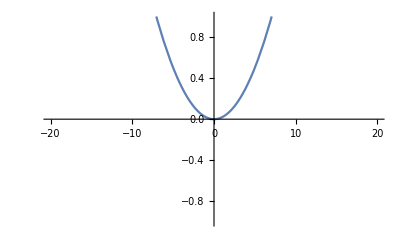

```mathematica
Plot[(ϵ(ϵ+4))/2 ξϕ^2/.ϵ->0.01,{ξϕ,-20,20},PlotRange->{-1,1}]
```

### GW potential integral reduction

```mathematica
Print["Try to reduce integral analytically to relax 0 backreaction limit"]
Integrate[Leff/E^(-2ϵ η/l),η]
Clear[ηp]
E^(-4 η/l)==D[ηp[η],η]
DSolve[%,ηp[η],η] //FullSimplify
Integrate[E^((2κ)/3 ψ^(ϵ/2)),ψ]//Simplify//PowerExpand
D[%,κ]//Simplify//PowerExpand
Series[%,{κ,0,1}]//Simplify//PowerExpand
```

Try to reduce integral analytically to relax 0 backreaction limit

-(ϵ (4+3 ϵ) C[0]^2 ∫ⅇ^(1/2 (-(8 η)/l-(ⅇ^(-(2 ϵ η)/l) C[0]^2)/(6 M^3)))ⅆη)/(2 l^2)

ⅇ^(-(4 η)/l)==ηp'[η]

{{ηp[η]→-1/4 ⅇ^(-(4 η)/l) l+C[1]}}

-((-1)^(-2/ϵ) 2^((-2+ϵ)/ϵ) 9^(1/ϵ) κ^(-2/ϵ) Gamma[2/ϵ,-2/3 κ ψ^(ϵ/2)])/ϵ

((-1)^(-2/ϵ) κ^(-(2+ϵ)/ϵ) (2 (-1)^(2/ϵ) ⅇ^(2/3 κ ψ^(ϵ/2)) ϵ κ^(2/ϵ) ψ+4^((-1+ϵ)/ϵ) 9^(1/ϵ) Gamma[2/ϵ,-2/3 κ ψ^(ϵ/2)]))/ϵ^2

1/ϵ^2(4^((-1+ϵ)/ϵ) 9^(1/ϵ) ⅇ^(-(2 ⅈ π)/ϵ) κ^(-(2+ϵ)/ϵ) Gamma[2/ϵ]+((2 ϵ ψ)/κ+4/3 ϵ ψ^(1+ϵ/2)+O[κ]^1)+ⅇ^((2 ⅈ π (-1+2 Floor[-(-π+Arg[κ]+Arg[-ψ^(ϵ/2)])/(2 π)]))/ϵ) (-(2 ((-1)^(2/ϵ) ϵ ψ))/κ+(8 (-1)^(-1+2/ϵ) ϵ ψ^(ϵ+1/2 (-1+2/ϵ) ϵ))/(3 (2+ϵ))+O[κ]^1))